# Dynamics of Radiation, Pressureless Dark Matter and Dark Energy with a Non-Linear Quadratic EoS

## Fixed Points of the Full System

## Find the Fixed Points of the System

### Non-Compact Variables

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z, and  radiation, r*)
de1:=x'=-3*y*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z+2*r-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*y*z
de4:=r'=-4*y*r
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,y,z,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,r→1/2 (-x+3 x^2-z+3 ℛ-3 x ℛ)},{x→1,y→-1/(√3),z→0,r→0},{x→1,y→1/(√3),z→0,r→0},{x→ℛ,y→-(√ℛ)/(√3),z→0,r→0},{x→ℛ,y→(√ℛ)/(√3),z→0,r→0}}

```mathematica
(*Remove arrows from fixed points*)
fp[1]={x,y/.FPs[[1,1]],z,r/.FPs[[1,2]]};
fp[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]],r/.FPs[[2,4]]};
fp[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]],r/.FPs[[3,4]]};
fp[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]],r/.FPs[[4,4]]};
fp[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]],r/.FPs[[5,4]]};
```

```mathematica
(*Put fixed points into a table*)
fps=Table[fp[i],{i,1,5}];
```

```mathematica
(*Put fixed points into a table in LaTeX format*)
FixedPoints=Table[fp[i],{i,1,5}]//TeXForm;
```

```mathematica
(*Export LaTeX formatted table*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\FPTable",FixedPoints,"Table"]*)
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z],D[de1,r]}, {D[de2,x],D[de2,y],D[de2,z],D[de2,r]},{D[de3,x],D[de3,y],D[de3,z],D[de3,r]},{D[de4,x],D[de4,y],D[de4,z],D[de4,r]}}];
J//MatrixForm
```

(3 y (-1+2 x-ℛ) | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | -2 y | -1/6 | -1/3
0 | -3 z | -3 y | 0
0 | -4 r | 0 | -4 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
fpTable=TableForm[Table[{fps[[i]]//MatrixForm,Simplify[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]]//MatrixForm},{i,1,5}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
z
1/2 (-x+3 x^2-z+3 ℛ-3 x ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 | -1/3
0 | -3 z | 0 | 0
0 | 2 (x-3 x^2+z-3 ℛ+3 x ℛ) | 0 | 0) | (0
0
-(√(18 x^3-z-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6)
(√(18 x^3-z-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6))
(1
-1/(√3)
0
0) | (√3 (-1+ℛ) | 0 | 0 | 0
1/6 (5-3 ℛ) | 2/(√3) | -1/6 | -1/3
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+ℛ))
(1
1/(√3)
0
0) | (-√3 (-1+ℛ) | 0 | 0 | 0
1/6 (5-3 ℛ) | -2/(√3) | -1/6 | -1/3
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√3)
0
0) | (-√3 (-1+ℛ) √ℛ | 0 | 0 | 0
1/6 (-1+3 ℛ) | (2 √ℛ)/(√3) | -1/6 | -1/3
0 | 0 | √3 √ℛ | 0
0 | 0 | 0 | (4 √ℛ)/(√3)) | ((2 √ℛ)/(√3)
√3 √ℛ
(4 √ℛ)/(√3)
-√3 (-1+ℛ) √ℛ)
(ℛ
(√ℛ)/(√3)
0
0) | (√3 (-1+ℛ) √ℛ | 0 | 0 | 0
1/6 (-1+3 ℛ) | -(2 √ℛ)/(√3) | -1/6 | -1/3
0 | 0 | -√3 √ℛ | 0
0 | 0 | 0 | -(4 √ℛ)/(√3)) | (-(4 √ℛ)/(√3)
-√3 √ℛ
-(2 √ℛ)/(√3)
√3 (-1+ℛ) √ℛ)

```mathematica
(*Put the eigenvalues into a separate table in LaTeX form to export*)
EigenvalTable=TableForm[Table[{Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]][[1]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]][[2]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]][[3]],Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]][[4]]},{i,1,5}],TableHeadings->{None,{"λ1","λ2","λ3","λ4"}}]//TeXForm;
```

```mathematica
(*Export table of eigenvalues*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\EigenvalTable",EigenvalTable,"Table"]*)
```

### Compact Variables

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, compact Hubble expansion, Y, compact dark matter, Z, and compact radiation, R*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-ℛ)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+2*R/(1-R)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de4:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,Z,R}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,R→(x-3 x^2+Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)/(-2+x-3 x^2+3 Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)},{x→1,Y→0,R→(-2+3 Z)/(-4+5 Z)},{Y→0,Z→0,R→(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ)},{x→ℛ,Y→0,R→(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ)},{Y→0,Z→(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ),R→0},{x→1,Y→-1/2,Z→0,R→0},{x→1,Y→1/2,Z→0,R→0},{x→ℛ,Y→-(√ℛ)/(√(3+ℛ)),Z→0,R→0},{x→ℛ,Y→(√ℛ)/(√(3+ℛ)),Z→0,R→0},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),Y→0,Z→0,R→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),Y→0,Z→0,R→0},{x→1,Y→0,Z→0,R→1/2},{x→ℛ,Y→0,Z→0,R→ℛ/(1+ℛ)},{x→1,Y→0,Z→2/3,R→0},{x→ℛ,Y→0,Z→(2 ℛ)/(1+2 ℛ),R→0}}

```mathematica
(*Remove arrows from fixed points*)
FP[1]={x,Y/.FPs[[1,1]],Z,R/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],Y/.FPs[[2,2]],Z,R/.FPs[[2,3]]};
FP[3]={x,Y/.FPs[[3,1]],Z/.FPs[[3,2]],R/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],Y/.FPs[[4,2]],Z,R/.FPs[[4,3]]};
FP[5]={x,Y/.FPs[[5,1]],Z/.FPs[[5,2]],R/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]],R/.FPs[[6,4]]};
FP[7]={x/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]],R/.FPs[[7,4]]};
FP[8]={x/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]],R/.FPs[[8,4]]};
FP[9]={x/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]],R/.FPs[[9,4]]};
FP[10]={x/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]],R/.FPs[[10,4]]};
FP[11]={x/.FPs[[11,1]],Y/.FPs[[11,2]],Z/.FPs[[11,3]],R/.FPs[[11,4]]};
FP[12]={x/.FPs[[12,1]],Y/.FPs[[12,2]],Z/.FPs[[12,3]],R/.FPs[[12,4]]};
FP[13]={x/.FPs[[13,1]],Y/.FPs[[13,2]],Z/.FPs[[13,3]],R/.FPs[[13,4]]};
FP[14]={x/.FPs[[14,1]],Y/.FPs[[14,2]],Z/.FPs[[14,3]],R/.FPs[[14,4]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,18}];
```

```mathematica
(*Put fixed points into a table in LaTeX format*)
CompactFPs=Table[FP[i],{i,1,18}]//TeXForm;
```

```mathematica
(*Export LaTeX formatted table*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\CompactFPTable",CompactFPs,"Table"]*)
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,Y],D[de1,Z],D[de1,R]}, {D[de2,x],D[de2,Y],D[de2,Z],D[de2,R]},{D[de3,x],D[de3,Y],D[de3,Z],D[de3,R]},{D[de4,x],D[de4,Y],D[de4,Z],D[de4,R]}}];
J//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2)) | 0 | 0
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 R)/(-1+R)+x-3 x^2+Z/(1-Z)-3 ℛ+3 x ℛ)))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+R)^2)
0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 Z))/(√(1-Y^2)) | 0
0 | (4 (-1+R) R)/((1-Y^2)^(3/2)) | 0 | (4 (-1+2 R) Y)/(√(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]]//MatrixForm},{i,1,14}];
```

```mathematica
(*Define fixed points not found using Solve*)
(*These are the fixed points at Y = +/- 1*)
FPInf[1]={ℛ,1,0,0};
FPInf[2]={ℛ,-1,0,0};
FPInf[3]={1,1,1,1};
FPInf[4]={1,-1,1,1};
```

```mathematica
(*Put fixed points into a table*)
FPInf=Table[FPInf[i],{i,1,4}];
```

```mathematica
(*Define the Jacobian's for the Y = +/- 1 fixed points*)
(*∞ -> k so Mathematica can solve for the eigenvalues*)
JInf=Table[{{-k,0,0,0},{0,k,0,0},{0,0,-k,0},{0,0,0,-k}},{{k,0,0,0},{0,-k,0,0},{0,0,k,0},{0,0,0,k}},{{k,0,0,0},{0,k,0,0},{0,0,k,0},{0,0,0,k}},{{-k,0,0,0},{0,-k,0,0},{0,0,-k,0},{0,0,0,-k}}];
```

Divide::indet: Indeterminate expression 0/0 encountered.

Power::infy: Infinite expression 1/0 encountered.

Table::iterb: Iterator {{k,0,0,0},{0,-k,0,0},{0,0,k,0},{0,0,0,k}} does not have appropriate bounds.

```mathematica
(*Calculate the eigenvalues of the Y = +/- fixed points*)
(*Substitute k = ∞ back in*)
FPTableInf=Table[{FPInf[[i]]//MatrixForm,JInf[[i]]//MatrixForm,Simplify[Eigenvalues[JInf[[i]]]]//MatrixForm},{i,1,4}]/.k->∞;
```

```mathematica
(*Join the two tables together*)
FPTable=TableForm[Join[FPTable,FPTableInf],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
Z
(x-3 x^2+Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)/(-2+x-3 x^2+3 Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/(6 (-1+Z)^2) | -((2-3 x^2 (-1+Z)+3 ℛ-3 Z (1+ℛ)+x (-1+Z) (1+3 ℛ))^2)/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (3 x^2 (-1+Z)+Z-3 ℛ+3 Z ℛ-x (-1+Z) (1+3 ℛ)))/((2-3 x^2 (-1+Z)+3 ℛ-3 Z (1+ℛ)+x (-1+Z) (1+3 ℛ))^2) | 0 | 0) | (0
0
-(√(18 x^3 (-1+Z)+9 (-1+ℛ) ℛ-9 x^2 (-1+Z) (1+3 ℛ)+Z (1+9 ℛ-9 ℛ^2)+x (-1+Z) (-1+18 ℛ+9 ℛ^2)))/(√6 √(-1+Z))
(√(18 x^3 (-1+Z)+9 (-1+ℛ) ℛ-9 x^2 (-1+Z) (1+3 ℛ)+Z (1+9 ℛ-9 ℛ^2)+x (-1+Z) (-1+18 ℛ+9 ℛ^2)))/(√6 √(-1+Z)))
(1
0
Z
(-2+3 Z)/(-4+5 Z)) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -1/(6 (-1+Z)^2) | -(4-5 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (-2+3 Z))/(4-5 Z)^2 | 0 | 0) | (0
0
-(√(-8+9 Z))/(√6 √(-1+Z))
(√(-8+9 Z))/(√6 √(-1+Z)))
(x
0
0
(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 | -1/12 (2+3 x^2+3 ℛ-x (1+3 ℛ))^2
0 | 0 | 0 | 0
0 | -(8 (3 x^2+3 ℛ-x (1+3 ℛ)))/((2+3 x^2+3 ℛ-x (1+3 ℛ))^2) | 0 | 0) | (0
0
-(√(18 x^3-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6)
(√(18 x^3-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6))
(ℛ
0
Z
(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ)) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/(6 (-1+Z)^2) | -(-2 (1+ℛ)+Z (3+2 ℛ))^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (Z-2 ℛ+2 Z ℛ))/(-2 (1+ℛ)+Z (3+2 ℛ))^2 | 0 | 0) | (0
0
-(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z))
(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z)))
(x
0
(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ)
0) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 (1+3 x^2+3 ℛ-x (1+3 ℛ))^2 | -1/3
0 | (-9 x^2-9 ℛ+x (3+9 ℛ))/((1+3 x^2+3 ℛ-x (1+3 ℛ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(6 x^3+(2-3 ℛ) ℛ+x ℛ (7+3 ℛ)-x^2 (4+9 ℛ)))/(√2)
(√(6 x^3+(2-3 ℛ) ℛ+x ℛ (7+3 ℛ)-x^2 (4+9 ℛ)))/(√2))
(1
-1/2
0
0) | (√3 (-1+ℛ) | 0 | 0 | 0
1/16 √3 (5-3 ℛ) | 2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+ℛ))
(1
1/2
0
0) | (-√3 (-1+ℛ) | 0 | 0 | 0
1/16 √3 (5-3 ℛ) | -2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√(3+ℛ))
0
0) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0 | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | -1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2)
0 | 0 | √3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
0 | 0 | 0 | (4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
(√ℛ)/(√(3+ℛ))
0
0) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0 | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | -1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2)
0 | 0 | -√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
0 | 0 | 0 | -(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2))
0
0
0) | (0 | 1/3 (-1-3 ℛ+√(1-30 ℛ+9 ℛ^2)) | 0 | 0
-1/6 √(1-30 ℛ+9 ℛ^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ (10+√(1-30 ℛ+9 ℛ^2))))/(3 √2)
(√(-1-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ (10+√(1-30 ℛ+9 ℛ^2))))/(3 √2))
(1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2))
0
0
0) | (0 | 1/3 (-1-3 ℛ-√(1-30 ℛ+9 ℛ^2)) | 0 | 0
1/6 √(1-30 ℛ+9 ℛ^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ (-10+√(1-30 ℛ+9 ℛ^2))))/(3 √2)
(√(-1-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ (-10+√(1-30 ℛ+9 ℛ^2))))/(3 √2))
(1
0
0
1/2) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -1/6 | -4/3
0 | 0 | 0 | 0
0 | -1 | 0 | 0) | (-2/(√3)
2/(√3)
0
0)
(ℛ
0
0
ℛ/(1+ℛ)) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/6 | -1/3 (1+ℛ)^2
0 | 0 | 0 | 0
0 | -(4 ℛ)/(1+ℛ)^2 | 0 | 0) | (0
0
-(2 √ℛ)/(√3)
(2 √ℛ)/(√3))
(1
0
2/3
0) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -3/2 | -1/3
0 | -2/3 | 0 | 0
0 | 0 | 0 | 0) | (-1
1
0
0)
(ℛ
1
0
0) | (-∞ | 0 | 0 | 0
0 | ∞ | 0 | 0
0 | 0 | -∞ | 0
0 | 0 | 0 | -∞) | (-∞
-∞
-∞
∞)
(ℛ
-1
0
0) | (∞ | 0 | 0 | 0
0 | -∞ | 0 | 0
0 | 0 | ∞ | 0
0 | 0 | 0 | ∞) | (-∞
∞
∞
∞)
(1
1
1
1) | (∞ | 0 | 0 | 0
0 | ∞ | 0 | 0
0 | 0 | ∞ | 0
0 | 0 | 0 | ∞) | (∞
∞
∞
∞)
(1
-1
1
1) | (-∞ | 0 | 0 | 0
0 | -∞ | 0 | 0
0 | 0 | -∞ | 0
0 | 0 | 0 | -∞) | (-∞
-∞
-∞
-∞)

```mathematica
(*Export the table in LaTeX form*)
FPTableLaTeX=FPTable//TeXForm;
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\FPTableLaTeX",FPTableLaTeX,"Table"]*)
```

```mathematica
(*Put the eigenvalues into a separate table in LaTeX form to export*)
Eigenvals=Table[{Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]][[1]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]][[2]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]][[3]],Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]][[4]]},{i,1,14}];

EigenvalsInf=Table[{Simplify[Eigenvalues[JInf[[i]]]]},{i,1,4}]/.k->∞;

CompactEigenvalTable=TableForm[Join[Eigenvals,EigenvalsInf],TableHeadings->{None,{"λ1","λ2","λ3","λ4"}}]//TeXForm;
```

```mathematica
(*Export table of eigenvalues*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\CompactEigenvalTable",CompactEigenvalTable,"Table"]*)
```

## Calculate Fixed Points in 2D

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (r) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-ℛ)/(1-x))^(1/(1-ℛ));

r[x_,cr_]=cr*((x-ℛ)/(1-x))^(4/(3*(1-ℛ)));
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, compact Hubble expansion, Y, compact dark matter, Z, and compact radiation, R*)
de5:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-ℛ)*(1-x)
de6:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(z[x,c]+2*r[x,cr]-3*ℛ+x*(1+3*ℛ)-3*x^2)
```

```mathematica
de5
de6
```

-(3 (1-x) Y (x-ℛ))/(√(1-Y^2))

-Y^2 √(1-Y^2)-1/6 (1-Y^2)^(3/2) (-3 x^2+c ((x-ℛ)/(1-x))^(1/(1-ℛ))+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ))

```mathematica
(*Find the fixed points of the system*)
FPs2D=Solve[{de5==0,de6==0},{x,Y},Assumptions->{c>0,cr>0,0<ℛ<1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ℛ,Y→0},{x→ℛ,Y→Indeterminate},{x→ℛ,Y→Indeterminate}}

```mathematica
(*Remove arrows from fixed points*)
FP2D[1]={x/.FPs2D[[1,1]],Y/.FPs2D[[1,2]]};
FP2D[2]={x/.FPs2D[[2,1]],Y/.FPs2D[[2,2]]};
FP2D[3]={x/.FPs2D[[3,1]],Y/.FPs2D[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs2D=Table[FP2D[i],{i,1,3}];
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J2D=Simplify[{{D[de5,x],D[de5,Y]}, {D[de6,x],D[de6,Y]}}];
J2D//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2))
((1-Y^2)^(3/2) (18 x^3-3 ℛ-9 ℛ^2-3 x^2 (7+9 ℛ)+x (3+30 ℛ+9 ℛ^2)+((-x+ℛ)/(-1+x))^(1/(1-ℛ)) (3 c+8 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ)))))/(18 (-1+x) (x-ℛ)) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (x-3 x^2-3 ℛ+3 x ℛ+((-x+ℛ)/(-1+x))^(1/(1-ℛ)) (c+2 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ))))))/(2 √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable2D=TableForm[Table[{FPs2D[[i]]//MatrixForm,Simplify[J/.{x->FPs2D[[i,1]],Y->FPs2D[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[J2D/.{x->FPs2D[[i,1]],Y->FPs2D[[i,2]]}]]//MatrixForm},{i,1,3}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Power::infy: Infinite expression 1/0 encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0 encountered.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Fixed Point | Jacobian | Eigenvalues
(ℛ
0) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/(6 (-1+Z)^2) | -1/(3 (-1+R)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | 4 (-1+R) R | 0 | 0) | Eigenvalues[{{0,0},{ComplexInfinity,0^(1+1/(1-ℛ)) (c+2 0^(1/(3-3 ℛ)) cr)}}]
(ℛ
Indeterminate) | (Indeterminate | Indeterminate | 0 | 0
Indeterminate | Indeterminate | Indeterminate | Indeterminate
0 | Indeterminate | Indeterminate | 0
0 | Indeterminate | 0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]
(ℛ
Indeterminate) | (Indeterminate | Indeterminate | 0 | 0
Indeterminate | Indeterminate | Indeterminate | Indeterminate
0 | Indeterminate | Indeterminate | 0
0 | Indeterminate | 0 | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]

## Find c for the Limiting Cases with 2 Einstein Points

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (r) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-ℛ)/(1-x))^(1/(1-ℛ));

r[x_,cr_]=cr*((x-ℛ)/(1-x))^(4/(3*(1-ℛ)));
```

```mathematica
(*Define compact Z and V variables to range between 0 and 1*)
Z[x_,c_]=Simplify[z[x,c]/(1+z[x,c])]
```

(c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))/(1+c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))

```mathematica
R[x_,cr_]=Simplify[r[x,cr]/(1+r[x,cr])]
```

(cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))/(1+cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))

```mathematica
(*Define w, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
w[x_,c_,cr_]=z[x,c]+2*r[x,cr]-3*ℛ+x*(1+3*ℛ)-3*x^2
```

-3 x^2+c ((x-ℛ)/(1-x))^(1/(1-ℛ))+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ)

```mathematica
(*Define compact W*)
W[x_,c_,cr_]=w[x,c,cr]/Sqrt[1+w[x,c,cr]^2]
```

(-3 x^2+c ((x-ℛ)/(1-x))^(1/(1-ℛ))+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ))/(√(1+(-3 x^2+c ((x-ℛ)/(1-x))^(1/(1-ℛ))+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ))^2))

```mathematica
(*Find the limit of w when x -> 1*)
Limit[w[x,c,cr],x->1, Assumptions->{c>0,cr>0,0<ℛ<1}]
```

∞

```mathematica
(*Find the limit of w when x -> 0*)
(*Here, R -> 0 too as R < x < 1*)
Limit[w[x,c,cr],x->0, Assumptions->{c>0,cr>0,0<ℛ<1}]
```

ConditionalExpression[c (-ℛ)^(1/(1-ℛ))+2 cr (-ℛ)^(4/(3 (1-ℛ)))-3 ℛ, 1/(1-ℛ)∈ℤ&&4/(3 (1-ℛ))∈ℤ]

```mathematica
(*Find the limit of w when x -> R*)
(*The limit is negative when x -> R and positive when x -> 1, meaning there is always at least 1 Einstein point as w must cross the x-axis at least once for R < x < 1*)
Limit[w[x,c,cr],x->ℛ,Assumptions->{c>0,cr>0,0<ℛ<1}]
```

-2 ℛ

```mathematica
(*First derivative of w with respect to x*)
wDeriv[x_,c_,cr_]=Simplify[D[w[x,c,cr],x]]
```

(-18 x^3+3 ℛ+9 ℛ^2+3 x^2 (7+9 ℛ)-3 x (1+10 ℛ+3 ℛ^2)-((-x+ℛ)/(-1+x))^(1/(1-ℛ)) (3 c+8 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ))))/(3 (-1+x) (x-ℛ))

```mathematica
(*Rearrange dw/dx = 0 for c*)
xsol[c_]=Solve[wDeriv[x,c,cr]==0,c];
```

```mathematica
(*Remove arrow from solution above*)
c=c/.xsol[c]
```

{-((-1+x) (x-ℛ) ((-x+ℛ)/(-1+x))^(-1/(1-ℛ)) ((6 x^3)/((-1+x) (x-ℛ))-ℛ/((-1+x) (x-ℛ))-(3 ℛ^2)/((-1+x) (x-ℛ))+(8 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ)+1/(1-ℛ)))/(3 (-1+x) (x-ℛ))-(x^2 (7+9 ℛ))/((-1+x) (x-ℛ))+(x (1+10 ℛ+3 ℛ^2))/((-1+x) (x-ℛ))))}

```mathematica
(*w with cr found above substituted in*)
w[x,c,cr]
```

{-3 x^2+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ)-(-1+x) (x-ℛ) ((x-ℛ)/(1-x))^(1/(1-ℛ)) ((-x+ℛ)/(-1+x))^(-1/(1-ℛ)) ((6 x^3)/((-1+x) (x-ℛ))-ℛ/((-1+x) (x-ℛ))-(3 ℛ^2)/((-1+x) (x-ℛ))+(8 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ)+1/(1-ℛ)))/(3 (-1+x) (x-ℛ))-(x^2 (7+9 ℛ))/((-1+x) (x-ℛ))+(x (1+10 ℛ+3 ℛ^2))/((-1+x) (x-ℛ)))}

```mathematica
(*Define R*)
(*The value for R was chosen as it shows all possible dynamical behaviour*)
ℛ=0.05;
```

```mathematica
(*Calculate cr*)
```

```mathematica
(*Define data from Planck 2018*)
H0=67.66;
Ωm=0.3111;
ΩΛ=0.6889;
zEq=3387;
```

```mathematica
(*Rearrange r for cr*)
cr=cr/.Simplify[Solve[r0==r[x0,cr],cr]]
```

{(1. r0)/((-0.05+x0)/(1.-1. x0))^1.40351}

```mathematica
(*Define r0*)
r0=ρr0/ρc;
```

```mathematica
(*Calculate Ωr0*)
(*At matter-radiation equality: Ωm0/aEq^3==Ωr0/aEq^4*)
(*First removes {} from the solution*)
aEq=1/(1+zEq);
Ωr=Ωr/.First[Solve[Ωm/aEq^3==Ωr/aEq^4,Ωr]]
```

0.0000918241

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Calculate ρx0*)
ρx0=3*H0^2*ΩΛ
```

9461.1

```mathematica
(*Calculate ρc*)
(*In this model, the dark energy density has already reached its asymptotic limit, therefore ρΛ is the same order of magnitude as ρx0*)
(*By definition, R = ρΛ/ρc*)

α=0.5;
ρΛ=α*ρx0;
ρc=ρΛ/ℛ
```

94611.

```mathematica
(*Calculate x0*)
x0=N[ρx0/ρc,12]
```

0.1

```mathematica
(*Value of cr using parameters above*)
(*First removes {} wrapping the solution*)
cr=First[cr]
```

0.00077017

```mathematica
(*Clear x0 and r0*)
Clear[x0,r0];
```

```mathematica
(*w with R, c and cr found above substituted in*)
w[x,c,cr]
```

{-0.15+0.00154034 ((-0.05+x)/(1-x))^1.40351+1.15 x-3 x^2-((-1+x) (-0.05+x) ((-0.05+x)/(1-x))^1.05263 (-0.0575/((-1+x) (-0.05+x))+(0.00205379 ((0.05-x)/(-1+x))^1.40351)/((-1+x) (-0.05+x))+(1.5075 x)/((-1+x) (-0.05+x))-(7.45 x^2)/((-1+x) (-0.05+x))+(6 x^3)/((-1+x) (-0.05+x))))/((0.05-x)/(-1+x))^1.05263}

```mathematica
(*Numerically solve w with c found above for x*)
(*FindRoot is a Newtonian approximation*)
x1=FindRoot[w[x,c,cr]==0,{x,0.1}];
x2=FindRoot[w[x,c,cr]==0,{x,0.6}];
```

```mathematica
(*Remove arrows from solutions above*)
x1=x/.x1
x2=x/.x2
```

0.246739

0.598794

```mathematica
(*Clear the value of c*)
Clear[c];
```

```mathematica
(*Find the values of c for x values found above*)
(*These values of c are the limiting cases where the system admits two Einstein points*)
(*Flatten removes the extra {} from the output*)
cLimitingCase1=Flatten[Solve[w[x1,c,cr]==0,c]]
```

{c→0.199932}

```mathematica
cLimitingCase2=Flatten[Solve[w[x2,c,cr]==0,c]]
```

{c→0.384481}

```mathematica
(*Remove arrows from solutions above*)
cLimitingCase1=c/.cLimitingCase1
cLimitingCase2=c/.cLimitingCase2
```

0.199932

0.384481

## Find c for the Limiting Case when there are 3 Einstein Points

```mathematica
(*To find the value of c in the limiting case where there are 3 Einstein points*)
```

```mathematica
(*Give an estimate of c in this case*)
cThreeEinsteinPointsLim=0.3180623543015309;
```

```mathematica
(*Find the Einstein points*)
ThreeEinsteinPointsc4i=FindRoot[w[x,cThreeEinsteinPointsLim,cr]==0,{x,0.1}]
ThreeEinsteinPointsc4ii=FindRoot[w[x,cThreeEinsteinPointsLim,cr]==0,{x,0.4}]
ThreeEinsteinPointsc4iii=FindRoot[w[x,cThreeEinsteinPointsLim,cr]==0,{x,0.9}]
```

{x→0.169206}

{x→0.426181}

{x→0.762176}

```mathematica
(*Remove arrows from solutions above*)
ThreeEinsteinPointsc4={x/.ThreeEinsteinPointsc4i,x/.ThreeEinsteinPointsc4ii,x/.ThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*In this limiting case, the two Closed Friedmann Separatrix (CFS) curves are the same*)
(*Calculate c by equating the two CFS curves and check if the value returned is the same as the guess*)
(*This is an iterative process*)
cLimIter=Flatten[Solve[(ThreeEinsteinPointsc4[[1]]+z[ThreeEinsteinPointsc4[[1]],c]+r[ThreeEinsteinPointsc4[[1]],cr])*((1-ThreeEinsteinPointsc4[[1]])/(ThreeEinsteinPointsc4[[1]]-ℛ))^(2/(3*(1-ℛ)))==(ThreeEinsteinPointsc4[[3]]+z[ThreeEinsteinPointsc4[[3]],c]+r[ThreeEinsteinPointsc4[[3]],cr])*((1-ThreeEinsteinPointsc4[[3]])/(ThreeEinsteinPointsc4[[3]]-ℛ))^(2/(3*(1-ℛ))),c]]
```

{c→0.318062}

```mathematica
(*Remove arrow from solution above*)
cLimIter=c/.cLimIter
```

0.318062

```mathematica
(*The difference of the guess of c and the calculation of c from the CFS curve for the limiting case when*)
cLimIter-cThreeEinsteinPointsLim
```

1.97085×10^-11

## Plots to Show the Number of Einstein Points in Each Case

```mathematica
(*Defining values of c to show the full range of dynamical behaviour*)
(*There are 7 cases in total to consider*)
c={0.05,cLimitingCase1,0.25,cThreeEinsteinPointsLim,0.35,cLimitingCase2,0.5}
```

{0.05,0.199932,0.25,0.318062,0.35,0.384481,0.5}

```mathematica
(*Export the values of c found here to use in other notebooks*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv",c]*)
```

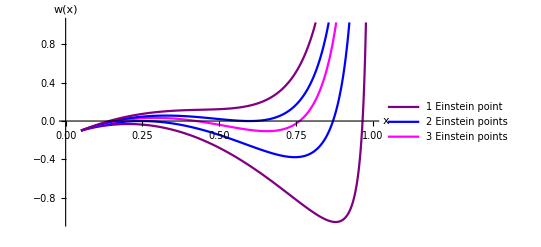

```mathematica
(*Plot w vs x for certain c values*)
(*Where w = 0 is where Einstein points exist*)
wplot=Plot[{w[x,c[[1]],cr],w[x,c[[2]],cr],w[x,c[[4]],cr],w[x,c[[6]],cr],w[x,c[[7]],cr]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","w(x)"}]
```

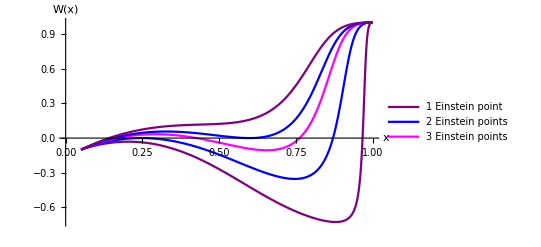

```mathematica
(*Plot compact W for certain c values*)
Wplot=Plot[{W[x,c[[1]],cr],W[x,c[[2]],cr],W[x,c[[4]],cr],W[x,c[[6]],cr],W[x,c[[7]],cr]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","W(x)"},ImageSize->{400,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\Wplot.pdf",Wplot]*)
```

```mathematica
(*Define zEinstein as w = 0 rearranged for z*)
zEinstein[x_]=3*ℛ-(1+3*ℛ)*x+3*x^2-2*r[x,cr];
```

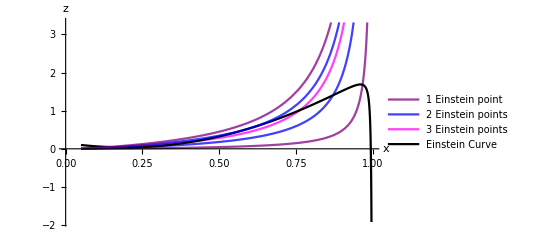

```mathematica
(*Plot of z(x) against the curves that show the number of Einstein points*)
zvsx=Plot[{z[x,c][[1]],z[x,c][[2]],z[x,c][[4]],zEinstein[x],z[x,c][[6]],z[x,c][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","Einstein Curve"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","z"}]
```

```mathematica
(*Define ZEinstein as c omapct zEinstein*)
ZEinstein[x_]=zEinstein[x]/(1+zEinstein[x]);
```

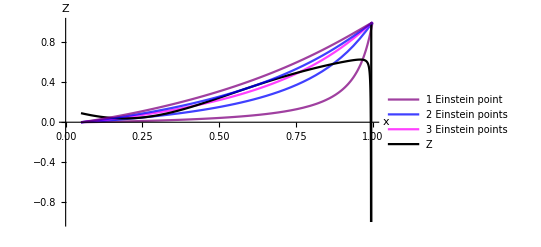

```mathematica
(*Plot of v(x) against the curves that show the number of Einstein points*)
Zvsx=Plot[{Z[x,c][[1]],Z[x,c][[2]],Z[x,c][[4]],ZEinstein[x],Z[x,c][[6]],Z[x,c][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","Z"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","Z"}, PlotRange->{-1,1}]
```

## Calculate the Einstein Points

```mathematica
(*Numerically solve w(x) = 0 to find the x values of the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
xOneEinsteinPointc1=FindRoot[w[x,c[[1]],cr]==0,{x,0.9}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc1=x/.xOneEinsteinPointc1
```

0.967421

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc1=Z[xOneEinsteinPointc1,c[[1]]]
```

0.62664

```mathematica
(*Calculate the V value of the Einstein point*)
ROneEinsteinPointc1=R[xOneEinsteinPointc1,cr]
```

0.0769768

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[1]={xOneEinsteinPointc1,0,ZOneEinsteinPointc1,ROneEinsteinPointc1}
```

{0.967421,0,0.62664,0.0769768}

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
xTwoEinsteinPointsc2i=FindRoot[w[x,c[[2]],cr]==0,{x,0.1}];
xTwoEinsteinPointsc2ii=FindRoot[w[x,c[[2]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc2={x/.xTwoEinsteinPointsc2i,x/.xTwoEinsteinPointsc2ii}
```

{0.246738,0.871103}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc2=Z[xTwoEinsteinPointsc2,c[[2]]]
```

{0.0463988,0.584023}

```mathematica
(*Calculate the V values of the Einstein points*)
RTwoEinsteinPointsc2=R[xTwoEinsteinPointsc2,cr]
```

{0.000117007,0.0102506}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[2]={xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]],RTwoEinsteinPointsc2[[1]]}
EinsteinFP[3]={xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]],RTwoEinsteinPointsc2[[2]]}
```

{0.246738,0,0.0463988,0.000117007}

{0.871103,0,0.584023,0.0102506}

### Three Einstein Points: c3

```mathematica
xThreeEinsteinPointsc3i=FindRoot[w[x,c[[3]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc3ii=FindRoot[w[x,c[[3]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc3iii=FindRoot[w[x,c[[3]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc3={x/.xThreeEinsteinPointsc3i,x/.xThreeEinsteinPointsc3ii,x/.xThreeEinsteinPointsc3iii}
```

{0.190763,0.339647,0.8311}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc3=Z[xThreeEinsteinPointsc3,c[[3]]]
```

{0.0381488,0.0950237,0.556187}

```mathematica
(*Calculate the V values of the Einstein points*)
RThreeEinsteinPointsc3=R[xThreeEinsteinPointsc3,cr]
```

{0.0000661406,0.000242189,0.00656399}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[4]={xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]],RThreeEinsteinPointsc3[[1]]}
EinsteinFP[5]={xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]],RThreeEinsteinPointsc3[[2]]}
EinsteinFP[6]={xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]],RThreeEinsteinPointsc3[[3]]}
```

{0.190763,0,0.0381488,0.0000661406}

{0.339647,0,0.0950237,0.000242189}

{0.8311,0,0.556187,0.00656399}

### Three Einstein Points: c4

```mathematica
xThreeEinsteinPointsc4i=FindRoot[w[x,c[[4]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc4ii=FindRoot[w[x,c[[4]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc4iii=FindRoot[w[x,c[[4]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc4={x/.xThreeEinsteinPointsc4i,x/.xThreeEinsteinPointsc4ii,x/.xThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc4=Z[xThreeEinsteinPointsc4,c[[4]]]
```

{0.0395735,0.169387,0.502254}

```mathematica
(*Calculate the V values of the Einstein points*)
RThreeEinsteinPointsc4=R[xThreeEinsteinPointsc4,cr]
```

{0.0000504818,0.000425625,0.00357739}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[7]={xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]],RThreeEinsteinPointsc4[[1]]}
EinsteinFP[8]={xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]],RThreeEinsteinPointsc4[[2]]}
EinsteinFP[9]={xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]],RThreeEinsteinPointsc4[[3]]}
```

{0.169206,0,0.0395735,0.0000504818}

{0.426181,0,0.169387,0.000425625}

{0.762176,0,0.502254,0.00357739}

### Three Einstein Points: c5

```mathematica
xThreeEinsteinPointsc5i=FindRoot[w[x,c[[5]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc5ii=FindRoot[w[x,c[[5]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc5iii=FindRoot[w[x,c[[5]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc5={x/.xThreeEinsteinPointsc5i,x/.xThreeEinsteinPointsc5ii,x/.xThreeEinsteinPointsc5iii}
```

{0.162421,0.476643,0.716724}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc5=Z[xThreeEinsteinPointsc5,c[[5]]]
```

{0.0405517,0.220133,0.462864}

```mathematica
(*Calculate the V values of the Einstein points*)
RThreeEinsteinPointsc5=R[xThreeEinsteinPointsc5,cr]
```

{0.0000459683,0.000577826,0.00255394}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[10]={xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]],RThreeEinsteinPointsc5[[1]]}
EinsteinFP[11]={xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]],RThreeEinsteinPointsc5[[2]]}
EinsteinFP[12]={xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]],RThreeEinsteinPointsc5[[3]]}
```

{0.162421,0,0.0405517,0.0000459683}

{0.476643,0,0.220133,0.000577826}

{0.716724,0,0.462864,0.00255394}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
xTwoEinsteinPointsc6i=FindRoot[w[x,c[[6]],cr]==0,{x,0.1}];
xTwoEinsteinPointsc6ii=FindRoot[w[x,c[[6]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc6={x/.xTwoEinsteinPointsc6i,x/.xTwoEinsteinPointsc6ii}
```

{0.156331,0.598794}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc6=Z[xTwoEinsteinPointsc6,c[[6]]]
```

{0.0416437,0.348389}

```mathematica
(*Calculate the V values of the Einstein points*)
RTwoEinsteinPointsc6=R[xTwoEinsteinPointsc6,cr]
```

{0.0000420821,0.001194}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[13]={xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]],RTwoEinsteinPointsc6[[1]]}
EinsteinFP[14]={xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]],RTwoEinsteinPointsc6[[2]]}
```

{0.156331,0,0.0416437,0.0000420821}

{0.598794,0,0.348389,0.001194}

### One Einstein Point: c7

```mathematica
xOneEinsteinPointc7=FindRoot[w[x,c[[7]],cr]==0,{x,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc7=x/.xOneEinsteinPointc7
```

0.141399

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc7=Z[xOneEinsteinPointc7,c[[7]]]
```

0.0451691

```mathematica
(*Calculate the V value of the Einstein point*)
ROneEinsteinPointc7=R[xOneEinsteinPointc7,cr]
```

0.0000332021

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[15]={xOneEinsteinPointc7,0,ZOneEinsteinPointc7,ROneEinsteinPointc7}
```

{0.141399,0,0.0451691,0.0000332021}

```mathematica
(*Find the eigenvalues of the Einstein fixed points*)
```

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPs=Table[EinsteinFP[i],{i,1,15}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each Einstein fixed point*)
TableForm[Table[{EinsteinFPs[[i]]//MatrixForm,Simplify[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],R->EinsteinFPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],R->EinsteinFPs[[i,4]]}]]//MatrixForm},{i,1,15}],TableHeadings->{{"c1","c2","","c3","","","c4","","","c5","","","c6","","c7"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues
c1 | (0.967421
0
0.62664
0.0769768) | (0. | -0.0896672 | 0 | 0
0.775754 | 0. | -1.19562 | -0.391249
0 | -0.701887 | 0. | 0
0 | -0.284205 | 0 | 0.) | (0.938523
-0.938523
7.96254×10^-17
0.)
c2 | (0.246738
0
0.0463988
0.000117007) | (0. | -0.444587 | 0 | 0
0.0550718 | 0. | -0.18328 | -0.333411
0 | -0.132738 | 0. | 0
0 | -0.000467972 | 0 | 0.) | (-0.00005637
0.0000563699
1.33882×10^-10
0.)
 | (0.871103
0
0.584023
0.0102506) | (0. | -0.317514 | 0 | 0
0.679436 | 0. | -0.963185 | -0.340274
0 | -0.728821 | 0. | 0
0 | -0.040582 | 0 | 0.) | (0.707154
-0.707154
5.36455×10^-17
0.)
c3 | (0.190763
0
0.0381488
0.0000661406) | (0. | -0.341731 | 0 | 0
-0.000904133 | 0. | -0.180149 | -0.333377
0 | -0.11008 | 0. | 0
0 | -0.000264545 | 0 | 0.) | (-0.142225
0.142225
8.12045×10^-18
0.)
 | (0.339647
0
0.0950237
0.000242189) | (0. | -0.573807 | 0 | 0
0.14798 | 0. | -0.203505 | -0.333495
0 | -0.257982 | 0. | 0
0 | -0.00096852 | 0 | 0.) | (-6.01468×10^-17+0.179132 ⅈ
-6.01468×10^-17-0.179132 ⅈ
1.03856×10^-16+0. ⅈ
0.+0. ⅈ)
 | (0.8311
0
0.556187
0.00656399) | (0. | -0.395783 | 0 | 0
0.639433 | 0. | -0.846153 | -0.337753
0 | -0.740529 | 0. | 0
0 | -0.0260836 | 0 | 0.) | (0.618331
-0.618331
-6.67169×10^-17
0.)
c4 | (0.169206
0
0.0395735
0.0000504818) | (0. | -0.297108 | 0 | 0
-0.0224602 | 0. | -0.180684 | -0.333367
0 | -0.114022 | 0. | 0
0 | -0.000201917 | 0 | 0.) | (-0.165356
0.165356
-8.58732×10^-20
0.)
 | (0.426181
0
0.169387
0.000425625) | (0. | -0.647579 | 0 | 0
0.234514 | 0. | -0.241575 | -0.333617
0 | -0.422085 | 0. | 0
0 | -0.00170178 | 0 | 0.) | (5.5299×10^-17+0.222111 ⅈ
5.5299×10^-17-0.222111 ⅈ
-8.82802×10^-18+0. ⅈ
0.+0. ⅈ)
 | (0.762176
0
0.502254
0.00357739) | (0. | -0.508117 | 0 | 0
0.57051 | 0. | -0.672717 | -0.335731
0 | -0.749985 | 0. | 0
0 | -0.0142584 | 0 | 0.) | (0.468432
-0.468432
1.05611×10^-17
0.)
c5 | (0.162421
0
0.0405517
0.0000459683) | (0. | -0.282485 | 0 | 0
-0.0292454 | 0. | -0.181053 | -0.333364
0 | -0.116722 | 0. | 0
0 | -0.000183865 | 0 | 0.) | (-0.171626
0.171626
4.86975×10^-18
0.)
 | (0.476643
0
0.220133
0.000577826) | (0. | -0.66986 | 0 | 0
0.284976 | 0. | -0.274036 | -0.333719
0 | -0.515023 | 0. | 0
0 | -0.00230997 | 0 | 0.) | (1.25475×10^-16+0.221333 ⅈ
1.25475×10^-16-0.221333 ⅈ
4.86337×10^-17+0. ⅈ
0.+0. ⅈ)
 | (0.716724
0
0.462864
0.00255394) | (0. | -0.566601 | 0 | 0
0.525057 | 0. | -0.577671 | -0.335043
0 | -0.745863 | 0. | 0
0 | -0.0101897 | 0 | 0.) | (0.369837
-0.369837
-2.60869×10^-16
0.)
c6 | (0.156331
0
0.0416437
0.0000420821) | (0. | -0.269126 | 0 | 0
-0.0353352 | 0. | -0.181466 | -0.333361
0 | -0.119728 | 0. | 0
0 | -0.000168322 | 0 | 0.) | (-0.176896
0.176896
1.37016×10^-17
0.)
 | (0.598794
0
0.348389
0.001194) | (0. | -0.660538 | 0 | 0
0.407127 | 0. | -0.392529 | -0.334131
0 | -0.681043 | 0. | 0
0 | -0.00477029 | 0 | 0.) | (0.000103877
-0.000103876
-5.09519×10^-10
0.)
c7 | (0.141399
0
0.0451691
0.0000332021) | (0. | -0.235425 | 0 | 0
-0.0502681 | 0. | -0.182808 | -0.333355
0 | -0.129387 | 0. | 0
0 | -0.000132804 | 0 | 0.) | (-0.188498
0.188498
9.76266×10^-18
0.)

## Submanifolds

## Set-up

### Submanifolds

```mathematica
(*Define the scale factor (a) in terms of x*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-ℛ);
a[x_,x0_]=(ca[x0]*((x-ℛ)/(1-x)))^((-1)/(3*(1-ℛ)));
```

```mathematica
(*Define compact radiation (R) and the scale factor (a) in terms of compact dark matter (Z)*)
rz[z_,cz_]=cz*z^(4/3);
RZ[Z_,cz_]=rz[Z/(1-Z),cz]/(1+rz[Z/(1-Z),cz]);

aZ[Z_,Z0_]=(((1-Z)/Z)(Z0/(1-Z0)))^(1/3);
```

```mathematica
(*Define compact dark matter (Z) and the scale factor (a) in terms of compact radiation (R)*)
zr[r_,cz_]=(r/cz)^(3/4);
ZR[R_,cz_]=zr[R/(1-R),cz]/(1+zr[R/(1-R),cz]);

aR[R_,R0_]=(((1-R)/R)(R0/(1-R0)))^(1/4);
```

```mathematica
(*Calculate cz*)
(*Rearrange z for cz*)
cz=cz/.Simplify[Solve[z0==zr[r0,cz],cz][[1]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

r0/z0^(4/3)

```mathematica
(*Define z0*)
z0=ρ0/ρc;
```

```mathematica
(*Calculate ρ0*)
ρ0=3*H0^2*Ωm
```

4272.53

```mathematica
(*Define v0*)
r0=ρr0/ρc
```

0.0000133291

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Value of cz*)
cz =cz
```

0.000828849

```mathematica
(*Clear z0 and r0*)
Clear[z0,r0]
```

```mathematica
(*Define w, the the RHS of y', for the submanifolds*)
wSubMan[x_,z_,r_]=-(1/6)*(z+2r-3*ℛ+x*(1+3*ℛ)-3*x^2);
```

```mathematica
(*Define the Flat Friedmann Separatrix for the submanifolds*)
(*Define ffs = Y^2/(1-Y^2)*)
ffsSubMan[x_,Z_,R_]=x/3+Z/(3*(1-Z))+R/(3*(1-R));
```

```mathematica
(*Rearrange the above for Y*)
FFSSubMan[x_,Z_,R_]=Sqrt[ffsSubMan[x,Z,R]/(1+ffsSubMan[x,Z,R])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) for the submanifolds in terms of x*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManx[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/a[x,x0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManx[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManx[x,x0,Z,Z0,R,R0]/(1+cfsSubManx[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of Z*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManZ[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/aZ[Z,Z0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManZ[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManZ[x,x0,Z,Z0,R,R0]/(1+cfsSubManZ[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of R*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManR[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/aR[R,R0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManR[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManR[x,x0,Z,Z0,R,R0]/(1+cfsSubManR[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
Sepx=ContourPlot[{x==ℛ,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{Black},PlotRange->Full];
```

```mathematica
(*Set up plot of the cr surface in terms of x and the cz surface in terms of Z*)
Surfacecr=ParametricPlot3D[{x,Y,R[x,cr]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
Surfacecz=ParametricPlot3D[{Z,Y,RZ[Z,cz]},{Z,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

### Potentials

```mathematica
(*Define the potential in terms of a, x, Z and R*)
USubMan[a_,x_,Z_,R_]=-a^2*(x/6+Z/(6*(1-Z))+R/(6*(1-R)));
```

## Qualitative ΛCDM Dynamics

```mathematica
(*These cases have the same qualitiative dynamics as ΛCDM, except here the Λs are asymptotic values*)
```

### x = ℛ, R = 0

#### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajxℛR0[Y0_,Z0_]:=Y^2/(1-Y^2)==ℛ/3+Z/(3*(1-Z))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
xℛR0traj[1]=ContourPlot[Evaluate[trajxℛR0[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[2]=ContourPlot[Evaluate[trajxℛR0[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[3]=ContourPlot[Evaluate[trajxℛR0[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[4]=ContourPlot[Evaluate[trajxℛR0[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[5]=ContourPlot[Evaluate[trajxℛR0[0.4,0.45]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[6]=ContourPlot[Evaluate[trajxℛR0[0.4,0.45]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[7]=ContourPlot[Evaluate[trajxℛR0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[8]=ContourPlot[Evaluate[trajxℛR0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[9]=ContourPlot[Evaluate[trajxℛR0[0.75,0.5]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[10]=ContourPlot[Evaluate[trajxℛR0[0.75,0.5]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxℛR0=Table[xℛR0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxℛR0=Plot[{FFSSubMan[ℛ,Z,0],-FFSSubMan[ℛ,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxℛR0=Plot[{{CFSSubManZ[ℛ,ℛ,Z,2*ℛ/(1+2*ℛ),0,0]},{-CFSSubManZ[ℛ,ℛ,Z,2*ℛ/(1+2*ℛ),0,0]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛR0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{2*ℛ/(1+2*ℛ),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

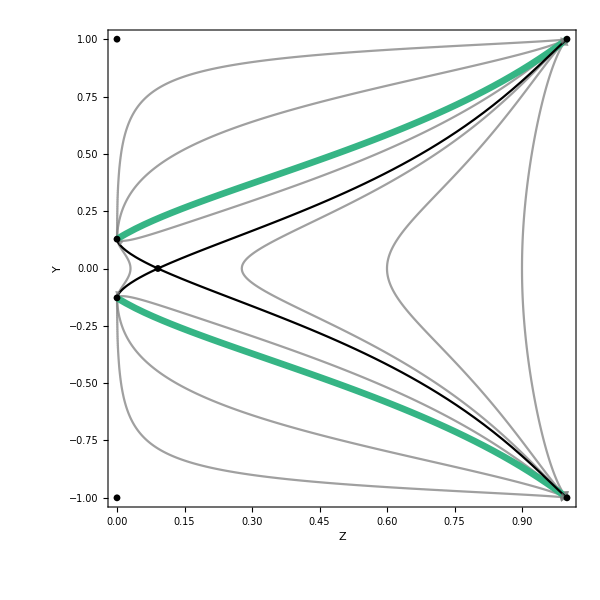

```mathematica
xℛR0SubMan=Show[TrajxℛR0,FFSxℛR0,CFSxℛR0,FPShowxℛR0,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

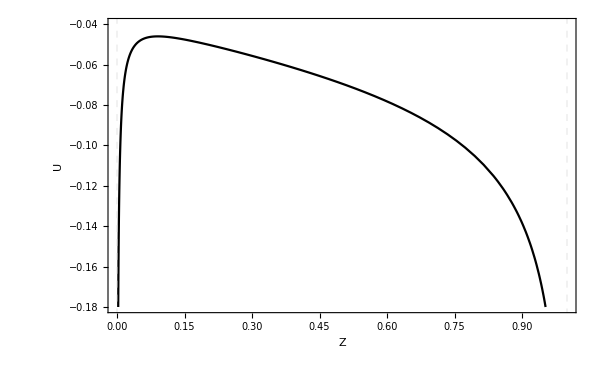

```mathematica
(*Plot the potential for this case*)
UxℛR0=Plot[{USubMan[aZ[Z,0.2],ℛ,Z,0]},{Z,0,1},Frame->True,FrameLabel->{"Z",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRangePadding->{0.04,0.001},PlotRange->{{0,1},{-0.18,-0.04}},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

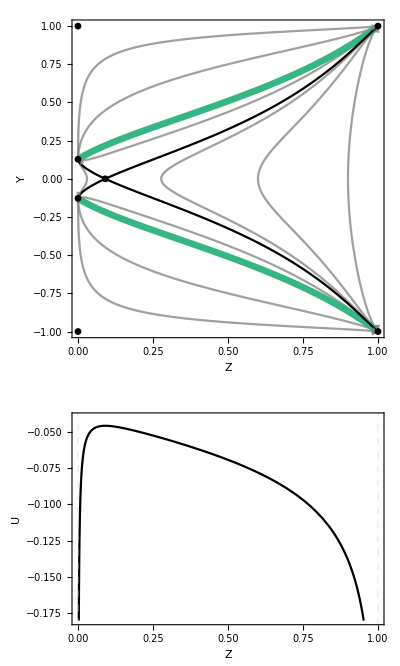

```mathematica
(*Plot the phase space and potential together*)
xℛR0=GraphicsColumn[{xℛR0SubMan,UxℛR0},Spacings->{0,0}]
```

### x = ℛ, Z = 0

#### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajxℛZ0[Y0_,R0_]:=Y^2/(1-Y^2)==ℛ/3+R/(3*(1-R))-(1/(aR[R,R0]^2))*(ℛ/3+R0/(3*(1-R0))-Y0^2/(1-Y0^2));
```

```mathematica
xℛZ0traj[1]=ContourPlot[Evaluate[trajxℛZ0[0,0.01]],{R,0,0.1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[2]=ContourPlot[Evaluate[trajxℛZ0[0,0.01]],{R,0.1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[3]=ContourPlot[Evaluate[trajxℛZ0[0,0.6]],{R,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[4]=ContourPlot[Evaluate[trajxℛZ0[0,0.9]],{R,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[5]=ContourPlot[Evaluate[trajxℛZ0[0.4,0.45]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[6]=ContourPlot[Evaluate[trajxℛZ0[0.4,0.45]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[7]=ContourPlot[Evaluate[trajxℛZ0[0.9,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[8]=ContourPlot[Evaluate[trajxℛZ0[0.9,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[9]=ContourPlot[Evaluate[trajxℛZ0[0.75,0.5]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[10]=ContourPlot[Evaluate[trajxℛZ0[0.75,0.5]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxℛZ0=Table[xℛZ0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxℛZ0=Plot[{FFSSubMan[ℛ,0,R],-FFSSubMan[ℛ,0,R]},{R,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxℛZ0=Plot[{{CFSSubManR[ℛ,ℛ,0,0,R,ℛ/(1+ℛ)]},{-CFSSubManR[ℛ,ℛ,0,0,R,ℛ/(1+ℛ)]}},{R,0,1},PlotStyle->Black,PlotPoints->500];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛZ0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{ℛ/(1+ℛ),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

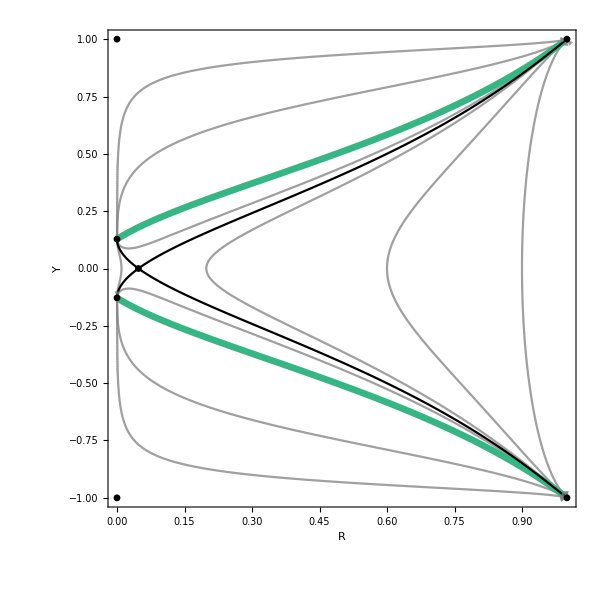

```mathematica
xℛZ0SubMan=Show[TrajxℛZ0,FFSxℛZ0,CFSxℛZ0,FPShowxℛZ0,FrameLabel->{"R",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

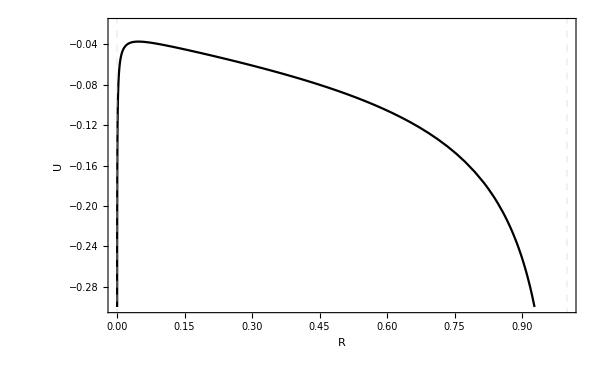

```mathematica
(*Plot the potential for this case*)
UxℛZ0=Plot[{USubMan[aR[R,0.2],ℛ,0,R]},{R,0,1},Frame->True,FrameLabel->{"R",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRange->{-0.3,-0.02},PlotRangePadding->{0.04,0},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

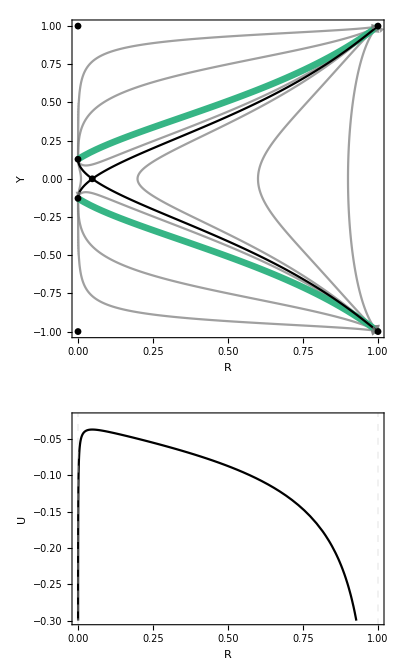

```mathematica
(*Plot the phase space and potential together*)
xℛZ0=GraphicsColumn[{xℛZ0SubMan,UxℛZ0},Spacings->{0,0}]
```

### x = ℛ

### Y = 0 fixed points

```mathematica
(*Solve for Z when Y = 0*)
xℛY0=Solve[wSubMan[ℛ,Z/(1-Z),RZ[Z,cz]/(1-RZ[Z,cz])]==0,Z]
```

{{Z→0.0908456}}

```mathematica
(*Remove arrow and de-nest solution*)
xℛY0=Z/.xℛY0[[1]]
```

0.0908456

### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Define Y^2/(1-Y^2) = traj3Dxℛ*)
traj3Dxℛ[Y0_,Z0_]=ℛ/3+Z/(3*(1-Z))+RZ[Z,cz]/(3*(1-RZ[Z,cz]))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))+RZ[Z0,cz]/(3*(1-RZ[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dxℛ[Y0_,Z0_]=Sqrt[traj3Dxℛ[Y0,Z0]/(1+traj3Dxℛ[Y0,Z0])];
```

```mathematica
xℛtraj3D[1]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.03],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[2]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.03],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[3]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.03],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[4]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.03],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->200,PlotRange->All,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[5]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.6],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[6]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.6],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[7]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.6],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[8]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.6],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[9]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.9],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[10]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.9],RZ[Z,cz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[11]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.9],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[12]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.9],RZ[Z,cz]},{Z,xℛY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[13]=ParametricPlot3D[{Z,traj3Dxℛ[0.4,0.45],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[14]=ParametricPlot3D[{Z,-traj3Dxℛ[0.4,0.45],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[15]=ParametricPlot3D[{Z,traj3Dxℛ[0.9,0.3],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[16]=ParametricPlot3D[{Z,-traj3Dxℛ[0.9,0.3],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[17]=ParametricPlot3D[{Z,traj3Dxℛ[0.75,0.5],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[18]=ParametricPlot3D[{Z,-traj3Dxℛ[0.75,0.5],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dxℛ=Table[xℛtraj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFS3Dxℛ=ParametricPlot3D[{{Z,FFSSubMan[ℛ,Z,RZ[Z,cz]],RZ[Z,cz]},{Z,-FFSSubMan[R,Z,RZ[Z,cz]],RZ[Z,cz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dxℛ=ParametricPlot3D[{{Z,CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,cz],RZ[xℛY0,cz]],RZ[Z,cz]},{Z,-CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,cz],RZ[xℛY0,cz]],RZ[Z,cz]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dxℛ=ListPointPlot3D[{{0,1,0},{0,-1,0},{1,1,1},{1,-1,1},{0,Sqrt[ℛ/(3+ℛ)],0},{0,-Sqrt[ℛ/(3+ℛ)],0},{xℛY0,0,RZ[xℛY0,cz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
xℛSubMan3D=Show[Traj3Dxℛ,FFS3Dxℛ,CFS3Dxℛ,FPShow3Dxℛ,Surfacecz,AxesLabel->{"Z","Y","R"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xℛSubMan3D.pdf",xℛSubMan3D]*)
```

### Plot the projection of the 3D submanifold

```mathematica
(*Trajectories for the phase space*)
trajxℛ[Y0_,Z0_]:=Y^2/(1-Y^2)==ℛ/3+Z/(3*(1-Z))+RZ[Z,cz]/(3*(1-RZ[Z,cz]))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))+RZ[Z0,cz]/(3*(1-RZ[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
xℛtraj[1]=ContourPlot[Evaluate[trajxℛ[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[2]=ContourPlot[Evaluate[trajxℛ[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[3]=ContourPlot[Evaluate[trajxℛ[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[4]=ContourPlot[Evaluate[trajxℛ[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[5]=ContourPlot[Evaluate[trajxℛ[0.4,0.45]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[6]=ContourPlot[Evaluate[trajxℛ[0.4,0.45]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[7]=ContourPlot[Evaluate[trajxℛ[0.9,0.3]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[8]=ContourPlot[Evaluate[trajxℛ[0.9,0.3]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[9]=ContourPlot[Evaluate[trajxℛ[0.75,0.5]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[10]=ContourPlot[Evaluate[trajxℛ[0.75,0.5]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajxℛ=Table[xℛtraj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxℛ=Plot[{FFSSubMan[ℛ,Z,RZ[Z,cz]],-FFSSubMan[ℛ,Z,RZ[Z,cz]]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxℛ=Plot[{{CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,cz],RZ[xℛY0,cz]]},{-CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,cz],RZ[xℛY0,cz]]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛ=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{xℛY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

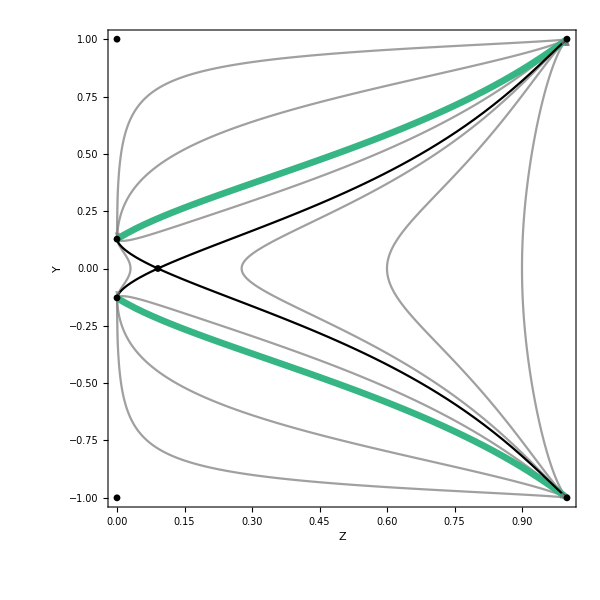

```mathematica
xℛSubMan=Show[Trajxℛ,FFSxℛ,CFSxℛ,FPShowxℛ,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xRSubMan.pdf",xRSubMan]*)
```

#### Potential

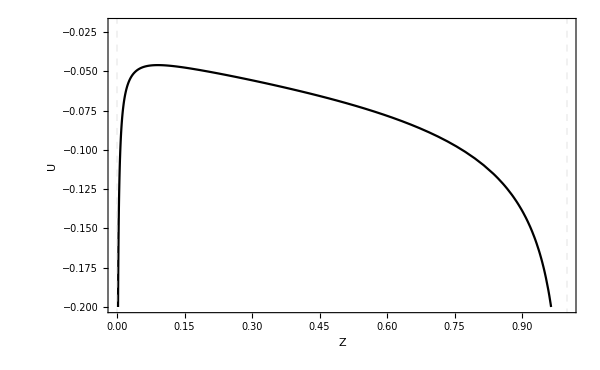

```mathematica
(*Plot the potential for this case*)
Uxℛ=Plot[{USubMan[aZ[Z,0.2],ℛ,Z,RZ[Z,cz]]},{Z,0,1},Frame->True,FrameLabel->{"Z",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRangePadding->{0.04,0},PlotRange->{-0.2,-0.02},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

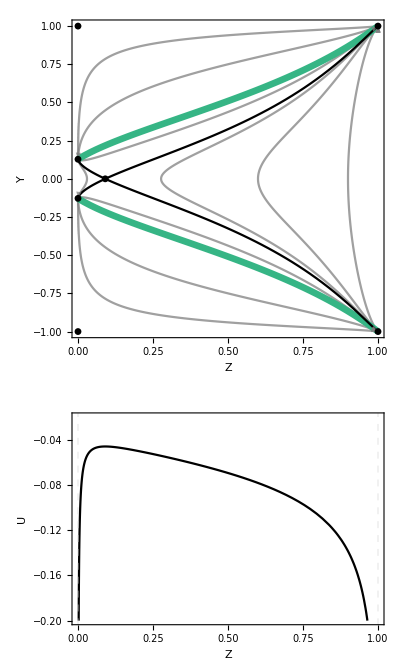

```mathematica
(*Plot the phase space and potential together*)
xℛProjection=GraphicsColumn[{xℛSubMan,Uxℛ},Spacings->{0,0}]
```

### x = 1, R = 0

#### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajx1R0[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
x1R0traj[1]=ContourPlot[Evaluate[trajx1R0[0,0.1]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[2]=ContourPlot[Evaluate[trajx1R0[0,0.1]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[3]=ContourPlot[Evaluate[trajx1R0[0,0.25]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[4]=ContourPlot[Evaluate[trajx1R0[0,0.25]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[5]=ContourPlot[Evaluate[trajx1R0[0,0.4]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[6]=ContourPlot[Evaluate[trajx1R0[0,0.4]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[7]=ContourPlot[Evaluate[trajx1R0[0.25,0.55]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[8]=ContourPlot[Evaluate[trajx1R0[0.25,0.55]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[9]=ContourPlot[Evaluate[trajx1R0[0.5,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[10]=ContourPlot[Evaluate[trajx1R0[0.5,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[11]=ContourPlot[Evaluate[trajx1R0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[12]=ContourPlot[Evaluate[trajx1R0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1R0=Table[x1R0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1R0=Plot[{FFSSubMan[1,Z,0],-FFSSubMan[1,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1R0=Plot[{CFSSubManZ[1,1,Z,2/3,0,0],-CFSSubManZ[1,1,Z,2/3,0,0]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1R0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {2/3,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

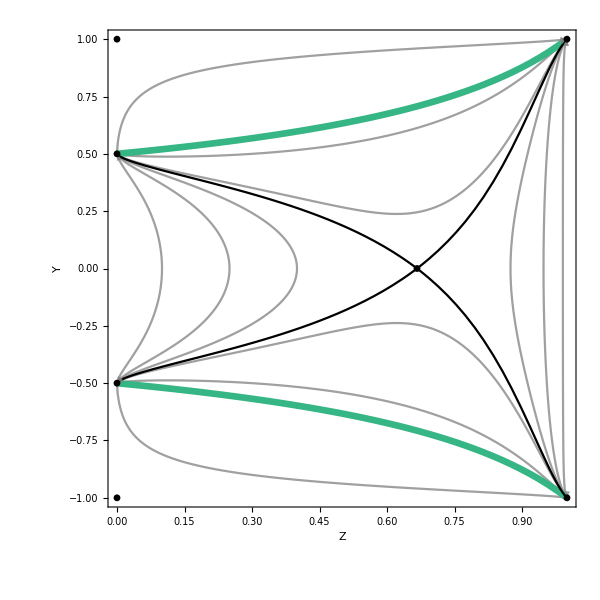

```mathematica
x1R0SubMan=Show[Trajx1R0,FFSx1R0,CFSx1R0,FPShowx1R0,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

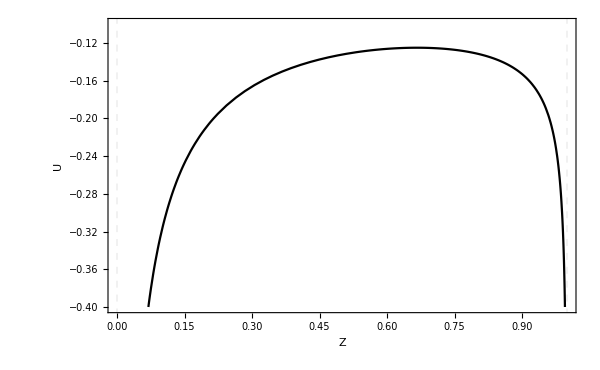

```mathematica
(*Plot the potential for this case*)
Ux1R0=Plot[{USubMan[aZ[Z,0.2],1,Z,0]},{Z,0,1},Frame->True,FrameLabel->{"Z",Rotate["U",270Degree]},ImageSize->{600,400},PlotRangePadding->{0.04,0},PlotRange->{-0.4,-0.1},PlotStyle->{Black},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

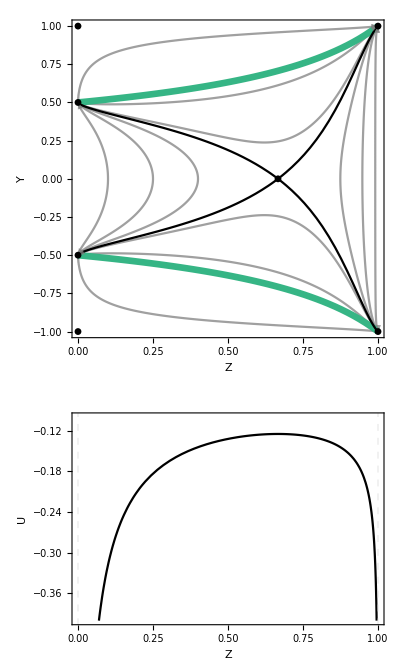

```mathematica
(*Plot the phase space and potential together*)
x1R0=GraphicsColumn[{x1R0SubMan,Ux1R0},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### x = 1, Z = 0

#### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajx1Z0[Y0_,R0_]:=Y^2/(1-Y^2)==1/3+R/(3*(1-R))-(1/aR[R,R0]^2)*(1/3+R0/(3*(1-R0))-Y0^2/(1-Y0^2));
```

```mathematica
x1Z0traj[1]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[2]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[3]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[4]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[5]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[6]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[7]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[8]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[9]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[10]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[11]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[12]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1Z0=Table[x1Z0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1Z0=Plot[{FFSSubMan[1,0,R],-FFSSubMan[1,0,R]},{R,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1Z0=Plot[{CFSSubManR[1,1,0,0,R,1/2],-CFSSubManR[1,1,0,0,R,1/2]},{R,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1Z0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {1/2,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

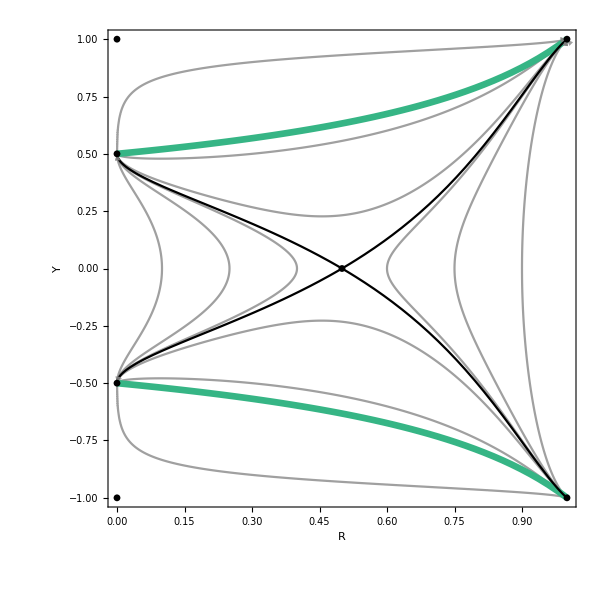

```mathematica
x1Z0SubMan=Show[Trajx1Z0,FFSx1Z0,CFSx1Z0,FPShowx1Z0,FrameLabel->{"R",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

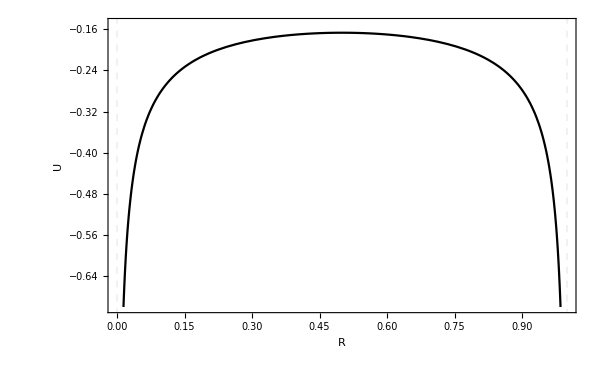

```mathematica
(*Plot the potential for this case*)
Ux1Z0=Plot[{USubMan[aR[R,0.2],1,0,R]},{R,0,1},Frame->True,FrameLabel->{"R",Rotate["U",270Degree]},ImageSize->{600,400},PlotRangePadding->{0.04,0},PlotRange->{-0.7,-0.15},PlotStyle->{Black},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

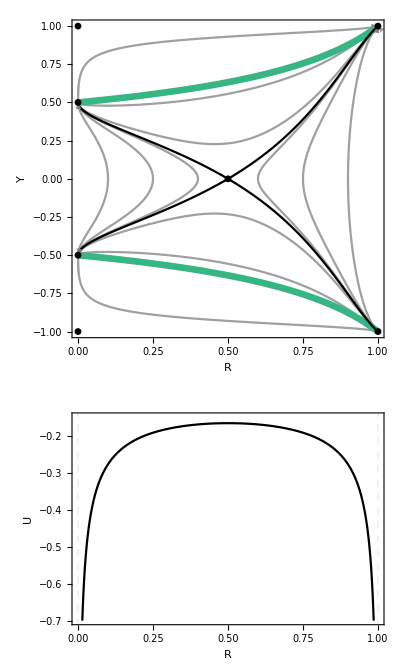

```mathematica
(*Plot the phase space and potential together*)
x1Z0=GraphicsColumn[{x1Z0SubMan,Ux1Z0},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### x = 1

#### Y = 0 fixed points

```mathematica
(*Solve for Z when Y = 0*)
x1Y0=Solve[wSubMan[1,Z/(1-Z),RZ[Z,cz]/(1-RZ[Z,cz])]==0,Z];
```

```mathematica
(*Remove arrow and de-nest solution*)
x1Y0=Z/.x1Y0[[1]]
```

0.666203

#### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Define Y^2/(1-Y^2) = traj3Dx1*)
traj3Dx1[Y0_,Z0_]=1/3+Z/(3*(1-Z))+RZ[Z,cz]/(3*(1-RZ[Z,cz]))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+RZ[Z0,cr]/(3*(1-RZ[Z0,cr]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dx1[Y0_,Z0_]=Sqrt[traj3Dx1[Y0,Z0]/(1+traj3Dx1[Y0,Z0])];
```

```mathematica
x1traj3D[1]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[2]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[3]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[4]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[5]=ParametricPlot3D[{Z,traj3Dx1[0.38,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[6]=ParametricPlot3D[{Z,-traj3Dx1[0.38,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[7]=ParametricPlot3D[{Z,traj3Dx1[0.38,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[8]=ParametricPlot3D[{Z,-traj3Dx1[0.38,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[9]=ParametricPlot3D[{Z,traj3Dx1[0.41,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[10]=ParametricPlot3D[{Z,-traj3Dx1[0.41,0.1],RZ[Z,cz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[11]=ParametricPlot3D[{Z,traj3Dx1[0.41,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[12]=ParametricPlot3D[{Z,-traj3Dx1[0.41,0.1],RZ[Z,cz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[13]=ParametricPlot3D[{Z,traj3Dx1[0.44,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[14]=ParametricPlot3D[{Z,-traj3Dx1[0.44,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[15]=ParametricPlot3D[{Z,traj3Dx1[0.48,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[16]=ParametricPlot3D[{Z,-traj3Dx1[0.48,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[17]=ParametricPlot3D[{Z,traj3Dx1[0.8,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[18]=ParametricPlot3D[{Z,-traj3Dx1[0.8,0.1],RZ[Z,cz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dx1=Table[x1traj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFS3Dx1=ParametricPlot3D[{{Z,FFSSubMan[1,Z,RZ[Z,cz]],RZ[Z,cz]},{Z,-FFSSubMan[1,Z,RZ[Z,cz]],RZ[Z,cz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dx1=ParametricPlot3D[{{Z,CFSSubManZ[1,1,Z,x1Y0,RZ[Z,cz],RZ[x1Y0,cz]],RZ[Z,cz]},{Z,-CFSSubManZ[1,1,Z,x1Y0,RZ[Z,cz],RZ[x1Y0,cz]],RZ[Z,cz]}},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dx1=ListPointPlot3D[{{0,1/2,0},{0,-1/2,0},{0,1,0},{0,-1,0},{1,1,1},{1,-1,1}, {x1Y0,0,RZ[x1Y0,cz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
x1SubMan3D=Show[Traj3Dx1,FFS3Dx1,CFS3Dx1,FPShow3Dx1,Surfacecz,AxesLabel->{"Z","Y","R"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan3D.pdf",x1SubMan3D]*)
```

### Plot the projection of the 3D submanifold

```mathematica
(*Trajectories for the phase space*)
trajx1[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))+RZ[Z,cz]/(3*(1-RZ[Z,cz]))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+RZ[Z0,cz]/(3*(1-RZ[Z0,cz]))-Y0^2/(1-Y0^2));
```

```mathematica
x1traj[1]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[2]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[3]=ContourPlot[Evaluate[trajx1[0.38,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[4]=ContourPlot[Evaluate[trajx1[0.38,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[5]=ContourPlot[Evaluate[trajx1[0.41,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[6]=ContourPlot[Evaluate[trajx1[0.41,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[7]=ContourPlot[Evaluate[trajx1[0.44,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[8]=ContourPlot[Evaluate[trajx1[0.44,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[9]=ContourPlot[Evaluate[trajx1[0.48,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[10]=ContourPlot[Evaluate[trajx1[0.48,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[11]=ContourPlot[Evaluate[trajx1[0.8,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[12]=ContourPlot[Evaluate[trajx1[0.8,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajx1=Table[x1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSx1=Plot[{FFSSubMan[1,Z,RZ[Z,cz]/(1-RZ[Z,cz])],-FFSSubMan[1,Z,RZ[Z,cz]/(1-RZ[Z,cz])]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSx1=Plot[{CFSSubManZ[1,1,Z,x1Y0,RZ[Z,cz],RZ[x1Y0,cz]],-CFSSubManZ[1,1,Z,x1Y0,RZ[Z,cz],RZ[x1Y0,cz]]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1=ListPlot[{{0,1},{0,-1},{0,1/2},{0,-1/2},{1,1},{1,-1}, {x1Y0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

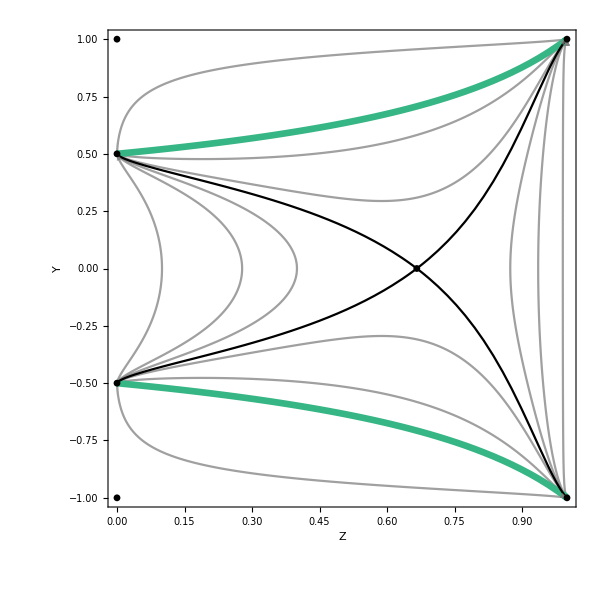

```mathematica
x1SubMan=Show[Trajx1,FFSx1,CFSx1,FPShowx1,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

### Potential

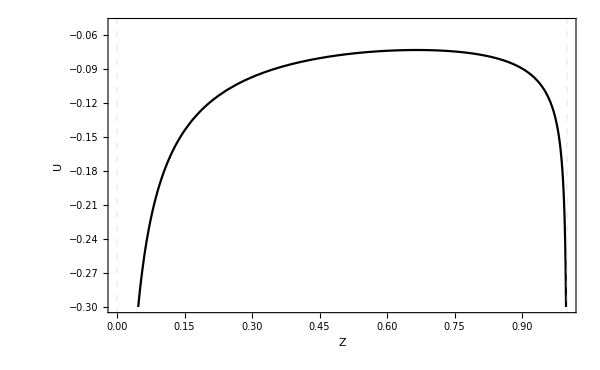

```mathematica
(*Plot the potential for this case*)
Ux1=Plot[{USubMan[aZ[Z,0.1],1,Z,RZ[Z,cz]]},{Z,0,1},Frame->True,FrameLabel->{"Z",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRange->{-0.3,-.05},PlotRangePadding->{0.04,0},GridLines->{{0,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

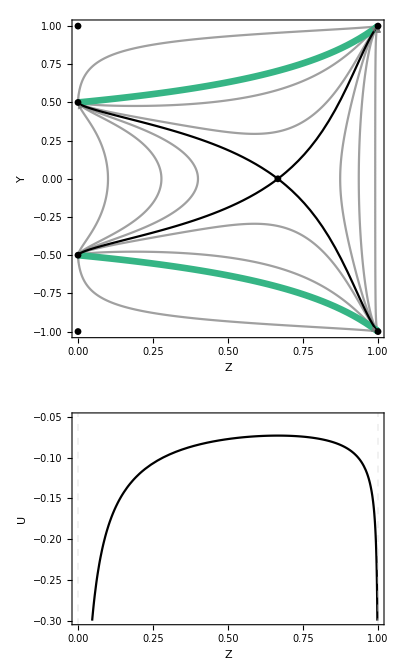

```mathematica
(*Plot the phase space and potential together*)
x1Projection=GraphicsColumn[{x1SubMan,Ux1},Spacings->{0,0}]
```

## Dynamic Dark Energy

```mathematica
(*These cases have a dynamical dark energy component*)
```

### Z = 0, V = 0

#### No Einstein Point Case

#### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajZ0R0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/a[x,x0]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
Z0R0traj[1]=ContourPlot[Evaluate[trajZ0R0[0,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[2]=ContourPlot[Evaluate[trajZ0R0[0.08,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[3]=ContourPlot[Evaluate[trajZ0R0[0.12,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[4]=ContourPlot[Evaluate[trajZ0R0[0.17,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[5]=ContourPlot[Evaluate[trajZ0R0[0.3,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[6]=ContourPlot[Evaluate[trajZ0R0[0.3,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[7]=ContourPlot[Evaluate[trajZ0R0[0.75,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[8]=ContourPlot[Evaluate[trajZ0R0[0.75,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajZ0R0=Table[Z0R0traj[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSZ0R0=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R0=ListPlot[{{ℛ,1},{ℛ,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

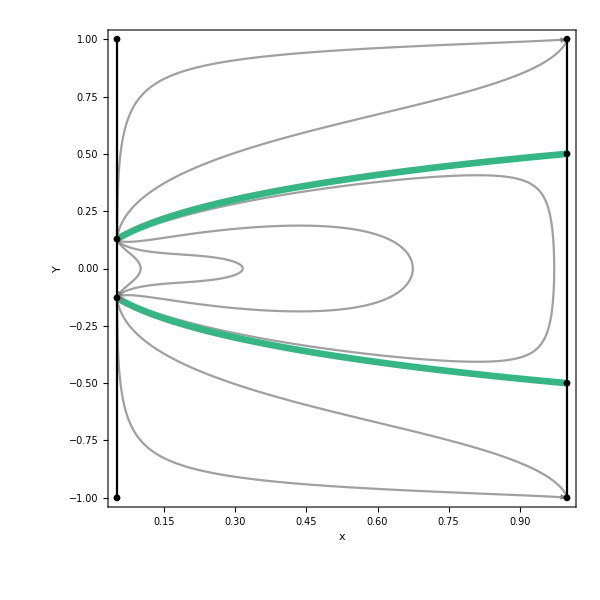

```mathematica
Z0R0SubMan=Show[TrajZ0R0,FFSZ0R0,FPShowZ0R0,Sepx,FrameLabel->{"x",Rotate["Y",300]},PlotRange->{{ℛ,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

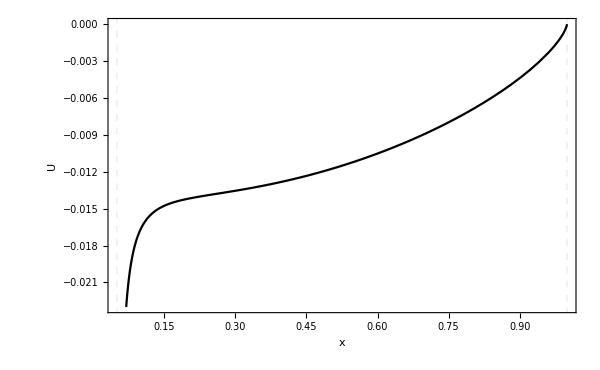

```mathematica
(*Plot the potential for this case*)
UZ0R0=Plot[{USubMan[a[x,0.1],x,0,0]},{x,ℛ,1},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRange->{{ℛ,1},{-0.023,0}},PlotRangePadding->{0.04,0},GridLines->{{0.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

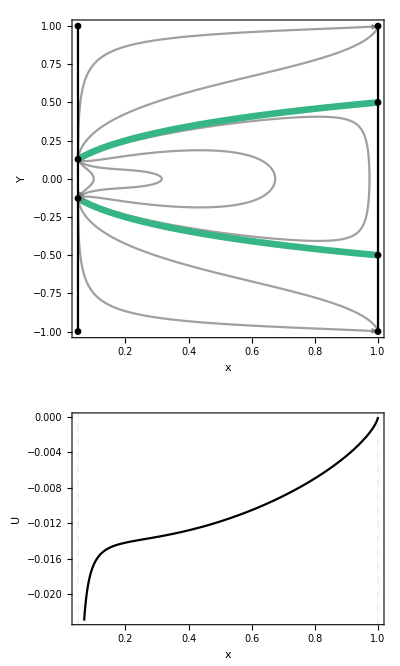

```mathematica
(*Plot the phase space and potential together*)
Z0R0=GraphicsColumn[{Z0R0SubMan,UZ0R0},Spacings->{0,0}]
```

#### Limiting 1 Einstein Point Case

```mathematica
(*Redefine a for these two cases*)
caZ0R0[x0_,ℛ2_]=(1-x0)/(x0-ℛ2);
aZ0R0[x_,x0_,ℛ2_]=(caZ0R0[x0,ℛ2]*((x-ℛ2)/(1-x)))^((-1)/(3*(1-ℛ2)));
```

```mathematica
(*Redefine the Closed Friedmann Separatrix (CFS) for the submanifolds in terms of x for these two cases*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsSubManZ0R0[x_,x0_,ℛ2_]= x/3-(1/aZ0R0[x,x0,ℛ2]^2)*(x0/3);
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManZ0R0[x_,x0_,ℛ2_]=Sqrt[cfsSubManZ0R0[x,x0,ℛ2]/(1+cfsSubManZ0R0[x,x0,ℛ2])];
```

```mathematica
(*Define value of ℛ for limiting case*)
ℛ1=5/3-2*Sqrt[6]/3;
```

#### Find the Y = 0 fixed points

```mathematica
Z0R0Y0Lim=FindRoot[-(1/6)*(-3*ℛ1+x*(1+3*ℛ1)-3*x^2)==0,{x,0.2}];
```

```mathematica
Z0R0Y0Lim=x/.Z0R0Y0Lim[[1]]
```

0.183503

#### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
trajZ0R01E[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/aZ0R0[x,x0,ℛ1]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
Z0R0traj1E[1]=ContourPlot[Evaluate[trajZ0R01E[0,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[2]=ContourPlot[Evaluate[trajZ0R01E[0.05,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[3]=ContourPlot[Evaluate[trajZ0R01E[0.1,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[4]=ContourPlot[Evaluate[trajZ0R01E[0.16,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[5]=ContourPlot[Evaluate[trajZ0R01E[0.3,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[6]=ContourPlot[Evaluate[trajZ0R01E[0.3,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[7]=ContourPlot[Evaluate[trajZ0R01E[0.75,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[8]=ContourPlot[Evaluate[trajZ0R01E[0.75,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajZ0R01E=Table[Z0R0traj1E[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSZ0R01E=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ1,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSZ0R01E=Plot[{{CFSSubManZ0R0[x,Z0R0Y0Lim,ℛ1]},{-CFSSubManZ0R0[x,Z0R0Y0Lim,ℛ1]}},{x,ℛ1,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R01E=ListPlot[{{ℛ1,1},{ℛ1,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ1,Sqrt[ℛ1/(3+ℛ1)]},{ℛ1,-Sqrt[ℛ1/(3+ℛ1)]},{Z0R0Y0Lim,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
SepxZ0R01E=ContourPlot[{x==ℛ1,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{Black},PlotRange->Full];
```

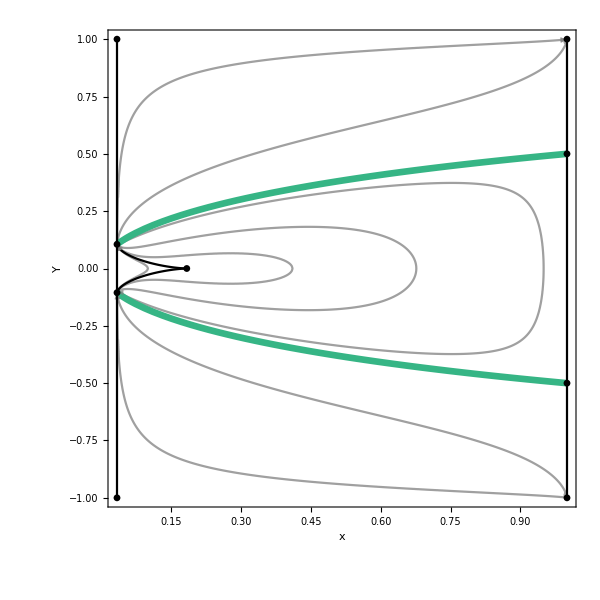

```mathematica
Z0R0SubMan1E=Show[TrajZ0R01E,FFSZ0R01E,CFSZ0R01E,FPShowZ0R01E,SepxZ0R01E,FrameLabel->{"x",Rotate["Y",300]},PlotRange->{{ℛ1,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04}]
```

#### Potential

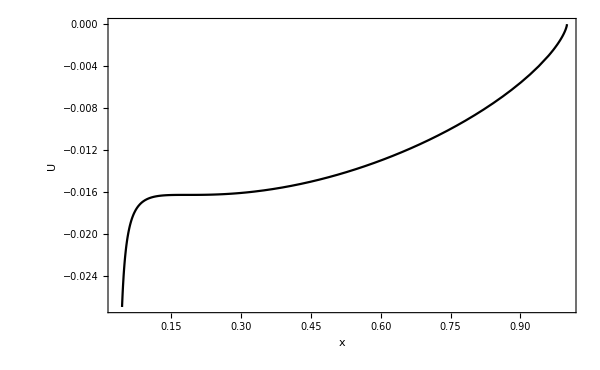

```mathematica
(*Plot the potential for this case*)
UZ0R01E=Plot[{USubMan[aZ0R0[x,0.1,ℛ1],x,0,0]},{x,ℛ1,1},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRange->{{ℛ1,1},{-0.027,0}},PlotRangePadding->{0.04,0},GridLines->{{ℛ1,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

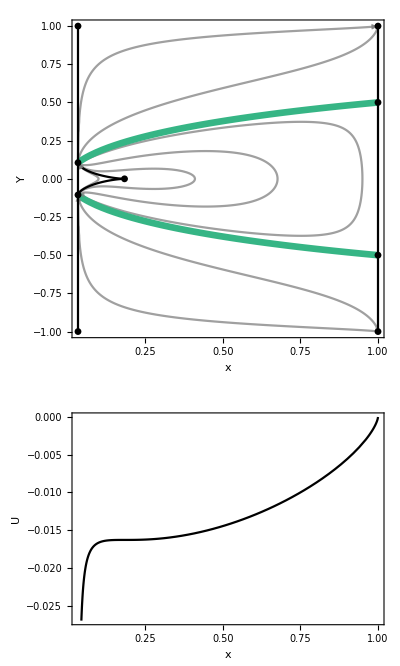

```mathematica
(*Plot the phase space and potential together*)
Z0R01E=GraphicsColumn[{Z0R0SubMan1E,UZ0R01E},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

#### 2 Einstein Point Case

```mathematica
(*Define value of ℛ for below the limiting case*)
ℛ2=0.02;
```

#### Find the Y = 0 fixed points

```mathematica
Z0R0Y02E1=FindRoot[-(1/6)*(-3*ℛ2+x*(1+3*ℛ2)-3*x^2)==0,{x,0.1}];
```

```mathematica
Z0R0Y02E1=x/.Z0R0Y02E1[[1]]
```

0.0707841

```mathematica
Z0R0Y02E2=FindRoot[-(1/6)*(-3*ℛ2+x*(1+3*ℛ2)-3*x^2)==0,{x,0.2}];
```

```mathematica
Z0R0Y02E2=x/.Z0R0Y02E2[[1]]
```

0.282549

#### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
trajZ0R02E[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/aZ0R0[x,x0,ℛ2]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
Z0R0traj2E[1]=ContourPlot[Evaluate[trajZ0R02E[0,0.05]],{x,0,0.1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[2]=ContourPlot[Evaluate[trajZ0R02E[0,0.05]],{x,0.1,0.55},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[3]=ContourPlot[Evaluate[trajZ0R02E[0.07,0.05]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[4]=ContourPlot[Evaluate[trajZ0R02E[0.11,0.05]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[5]=ContourPlot[Evaluate[trajZ0R02E[0.2,0.05]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[6]=ContourPlot[Evaluate[trajZ0R02E[0.2,0.05]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[7]=ContourPlot[Evaluate[trajZ0R02E[0.55,0.05]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[8]=ContourPlot[Evaluate[trajZ0R02E[0.55,0.05]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajZ0R02E=Table[Z0R0traj2E[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSZ0R02E=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ2,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSZ0R02E=Plot[{{CFSSubManZ0R0[x,Z0R0Y02E1,ℛ2]},{-CFSSubManZ0R0[x,Z0R0Y02E1,ℛ2]},{CFSSubManZ0R0[x,Z0R0Y02E2,ℛ2]},{-CFSSubManZ0R0[x,Z0R0Y02E2,ℛ2]}},{x,ℛ2,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R02E=ListPlot[{{ℛ2,1},{ℛ2,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ2,Sqrt[ℛ2/(3+ℛ2)]},{ℛ2,-Sqrt[ℛ2/(3+ℛ2)]},{Z0R0Y02E1,0},{Z0R0Y02E2,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
SepxZ0R02E=ContourPlot[{x==ℛ2,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{Black},PlotRange->Full];
```

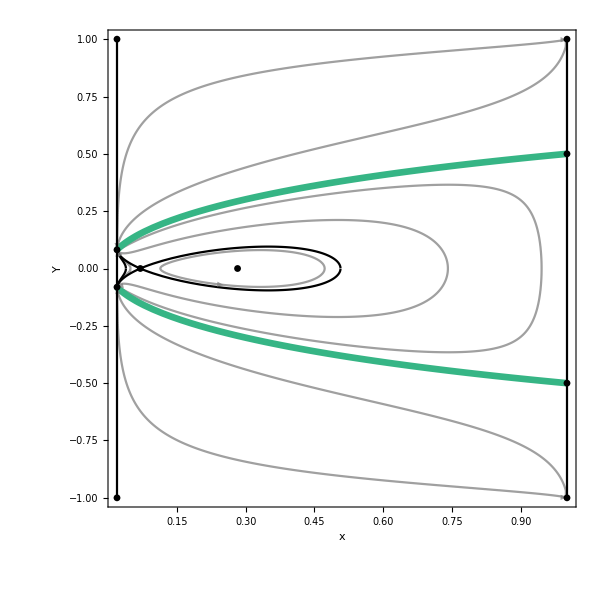

```mathematica
Z0R0SubMan2E=Show[TrajZ0R02E,FFSZ0R02E,CFSZ0R02E,FPShowZ0R02E,SepxZ0R02E,FrameLabel->{"x",Rotate["Y",300]},PlotRange->{{ℛ2,1},{-1,1}},ImageSize->{600,600},PlotRange->{{ℛ2,1},{-1,1}},PlotRangePadding->{0.04,0.04}]
```

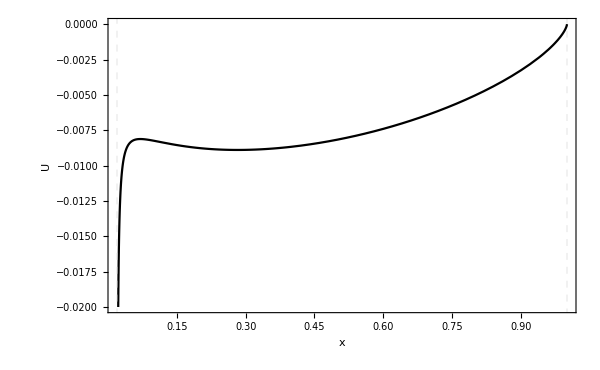

```mathematica
(*Plot the potential for this case*)
UZ0R02E=Plot[{USubMan[aZ0R0[x,0.05,ℛ2],x,0,0]},{x,ℛ2,1},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},PlotStyle->{Black},ImageSize->{600,400},PlotRange->{{ℛ2,1},{-0.02,0}},PlotRangePadding->{0.04,0},GridLines->{{ℛ2,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

#### Final Plot

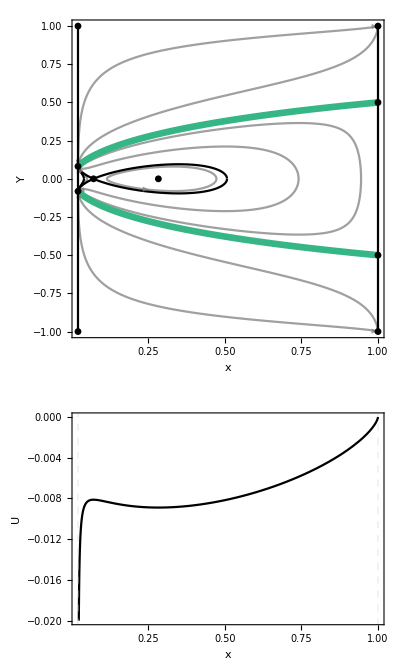

```mathematica
(*Plot the phase space and potential together*)
Z0R02E=GraphicsColumn[{Z0R0SubMan2E,UZ0R02E},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\x1SubMan.pdf",x1SubMan]*)
```

### R = 0

#### Find the Y = 0 fixed points

```mathematica
(*Plot the c1, c4 and c7 surfaces for the R = 0 submanifold*)
```

```mathematica
R0Y0c1=FindRoot[wSubMan[x,z[x,c[[1]]],0]==0,{x,0.9}];
```

```mathematica
R0Y0c1=x/.R0Y0c1[[1]]
```

0.970338

```mathematica
R0Y0c7=FindRoot[wSubMan[x,z[x,c[[7]]],0]==0,{x,0.9}];
```

```mathematica
R0Y0c7=x/.R0Y0c7[[1]]
```

0.141472

#### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Define Y^2/(1-Y^2) = traj3DR0*)
traj3DR0[Y0_,x0_]:=x/3+z[x,c]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3DR0[Y0_,x0_]=Sqrt[traj3DR0[Y0,x0]/(1+traj3DR0[Y0,x0])];
```

```mathematica
R0traj3D[1]=ParametricPlot3D[{x,traj3DR0[0,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[2]=ParametricPlot3D[{x,-traj3DR0[0,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[3]=ParametricPlot3D[{x,traj3DR0[0,0.5][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[4]=ParametricPlot3D[{x,-traj3DR0[0,0.5][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[5]=ParametricPlot3D[{x,traj3DR0[0,0.7][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[6]=ParametricPlot3D[{x,-traj3DR0[0,0.7][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[7]=ParametricPlot3D[{x,traj3DR0[0,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[8]=ParametricPlot3D[{x,-traj3DR0[0,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[9]=ParametricPlot3D[{x,traj3DR0[0.4,0.2][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[10]=ParametricPlot3D[{x,-traj3DR0[0.4,0.2][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[11]=ParametricPlot3D[{x,traj3DR0[0.9,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[12]=ParametricPlot3D[{x,-traj3DR0[0.9,0.3][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[13]=ParametricPlot3D[{x,traj3DR0[0.4,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[14]=ParametricPlot3D[{x,-traj3DR0[0.4,0.9][[1]],Z[x,c][[1]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[15]=ParametricPlot3D[{x,traj3DR0[0,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[16]=ParametricPlot3D[{x,-traj3DR0[0,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[17]=ParametricPlot3D[{x,traj3DR0[0,0.5][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[18]=ParametricPlot3D[{x,-traj3DR0[0,0.5][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[19]=ParametricPlot3D[{x,traj3DR0[0,0.7][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[20]=ParametricPlot3D[{x,-traj3DR0[0,0.7][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[21]=ParametricPlot3D[{x,traj3DR0[0,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[22]=ParametricPlot3D[{x,-traj3DR0[0,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[23]=ParametricPlot3D[{x,traj3DR0[0.4,0.2][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[24]=ParametricPlot3D[{x,-traj3DR0[0.4,0.2][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[25]=ParametricPlot3D[{x,traj3DR0[0.9,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[26]=ParametricPlot3D[{x,-traj3DR0[0.9,0.3][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[27]=ParametricPlot3D[{x,traj3DR0[0.4,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj3D[28]=ParametricPlot3D[{x,-traj3DR0[0.4,0.9][[7]],Z[x,c][[7]]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
traj3DR0=Table[R0traj3D[i],{i,1,28}];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFS3DR0=ParametricPlot3D[{{x,FFSSubMan[x,Z[x,c][[1]],0],Z[x,c][[1]]},{x,-FFSSubMan[x,Z[x,c][[1]],0],Z[x,c][[1]]},{x,FFSSubMan[x,Z[x,c][[1]],0],Z[x,c][[7]]},{x,-FFSSubMan[x,Z[x,c][[7]],0],Z[x,c][[7]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3DR0=ParametricPlot3D[{{x,CFSSubManx[x,R0Y0c1,Z[x,c[[1]]],Z[R0Y0c1,c[[1]]],0,0],Z[x,c[[1]]]},{x,-CFSSubManx[x,R0Y0c1,Z[x,c[[1]]],Z[R0Y0c1,c[[1]]],0,0],Z[x,c[[1]]]},{x,CFSSubManx[x,R0Y0c7,Z[x,c[[7]]],Z[R0Y0c7,c[[7]]],0,0],Z[x,c[[7]]]},{x,-CFSSubManx[x,R0Y0c7,Z[x,c[[7]]],Z[R0Y0c7,c[[7]]],0,0],Z[x,c[[7]]]}},{x,0,1},PlotStyle->Black,PlotRange->All];
```

```mathematica
(*Plot the fixed points*)
FPShow3DR0 = ListPointPlot3D[{{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{ℛ,1,0},{ℛ,-1,0},{1,1,1},{1,-1,1},{R0Y0c1,0,Z[R0Y0c1,c[[1]]]},{R0Y0c7,0,Z[R0Y0c7,c[[7]]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Set up plot of the cr surface*)
SurfaceR=ParametricPlot3D[{{x,Y,Z[x,c[[1]]]},{x,Y,Z[x,c[[7]]]}},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]},{Red, Opacity[0.25]}},Mesh->None];
```

```mathematica
R0SubMan3D=Show[traj3DR0,FFS3DR0,CFS3DR0,FPShow3DR0,SurfaceR,AxesLabel->{"x","Y","Z"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\R0SubMan3D.pdf",R0SubMan3D]*)
```

#### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the c1 surface of the phase space*)
trajR0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c[[1]]]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c[[1]]]/3-Y0^2/(1-Y0^2));
```

```mathematica
R0traj[1]=ContourPlot[Evaluate[trajR0[0,0.3]],{x,0,R0Y0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[2]=ContourPlot[Evaluate[trajR0[0,0.3]],{x,R0Y0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[3]=ContourPlot[Evaluate[trajR0[0,0.5]],{x,0,R0Y0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[4]=ContourPlot[Evaluate[trajR0[0,0.5]],{x,R0Y0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[5]=ContourPlot[Evaluate[trajR0[0,0.7]],{x,0,R0Y0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[6]=ContourPlot[Evaluate[trajR0[0,0.7]],{x,R0Y0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[7]=ContourPlot[Evaluate[trajR0[0,0.9]],{x,0,R0Y0c1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[8]=ContourPlot[Evaluate[trajR0[0,0.9]],{x,R0Y0c1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[9]=ContourPlot[Evaluate[trajR0[0.4,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[10]=ContourPlot[Evaluate[trajR0[0.4,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[11]=ContourPlot[Evaluate[trajR0[0.9,0.3]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[12]=ContourPlot[Evaluate[trajR0[0.9,0.3]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[13]=ContourPlot[Evaluate[trajR0[0.4,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
R0traj[14]=ContourPlot[Evaluate[trajR0[0.4,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajR0=Table[R0traj[i],{i,1,14}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSR0=Plot[{FFSSubMan[x,Z[x,c[[1]]],0],-FFSSubMan[x,Z[x,c[[1]]],0]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSR0=Plot[{{CFSSubManx[x,R0Y0c1,0,0,Z[x,c[[1]]],Z[R0Y0c1,c[[1]]]]},{-CFSSubManx[x,R0Y0c1,0,0,Z[x,c[[1]]],Z[R0Y0c1,c[[1]]]]}},{x,ℛ,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowR0 = ListPlot[{{1,1},{1,-1},{ℛ,1},{ℛ,-1}, {ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{R0Y0c1,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

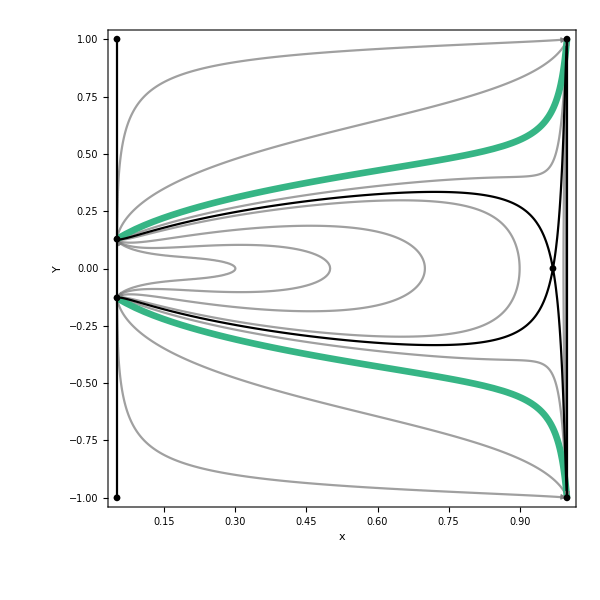

```mathematica
R0SubMan=Show[trajR0,FFSR0,CFSR0,FPShowR0,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600},PlotRange->All]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\R0SubMan.pdf",R0SubMan]*)
```

#### Potential

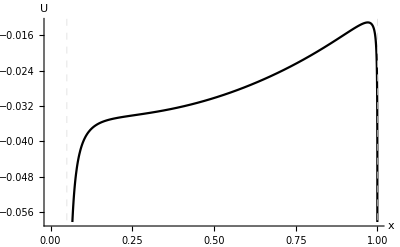

```mathematica
(*Plot the potential for this case*)
UR0=Plot[{USubMan[a[x,0.2],x,Z[x,c[[1]]],0]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

### Z = 0

#### Find the Y = 0 fixed points

```mathematica
Z0Y0=FindRoot[wSubMan[x,0,r[x,cr]]==0,{x,0.99}];
```

```mathematica
Z0Y0=x/.Z0Y0
```

0.994231

#### Plot the Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Define Y^2/(1-Y^2) = traj3DZ0*)
traj3DZ0[Y0_,x0_]:=x/3+R[x,cr]/(3*(1-R[x,cr]))-(1/a[x,x0]^2)*(x0/3+R[x0,cr]/(3*(1-R[x0,cr]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
traj3DZ0[Y0_,x0_]=Sqrt[traj3DZ0[Y0,x0]/(1+traj3DZ0[Y0,x0])];
```

```mathematica
Z0traj3D[1]=ParametricPlot3D[{x,traj3DZ0[0,0.3],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[2]=ParametricPlot3D[{x,-traj3DZ0[0,0.3],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[3]=ParametricPlot3D[{x,traj3DZ0[0,0.5],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[4]=ParametricPlot3D[{x,-traj3DZ0[0,0.5],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[5]=ParametricPlot3D[{x,traj3DZ0[0,0.7],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[6]=ParametricPlot3D[{x,-traj3DZ0[0,0.7],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[7]=ParametricPlot3D[{x,traj3DZ0[0,0.99],R[x,cr]},{x,0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[8]=ParametricPlot3D[{x,-traj3DZ0[0,0.99],R[x,cr]},{x,0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[9]=ParametricPlot3D[{x,traj3DZ0[0.4,0.2],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[10]=ParametricPlot3D[{x,-traj3DZ0[0.4,0.2],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[11]=ParametricPlot3D[{x,traj3DZ0[0.9,0.3],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[12]=ParametricPlot3D[{x,-traj3DZ0[0.9,0.3],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[13]=ParametricPlot3D[{x,traj3DZ0[0.4,0.99],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj3D[14]=ParametricPlot3D[{x,-traj3DZ0[0.4,0.99],R[x,cr]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3DZ0=Table[Z0traj3D[i],{i,1,14}];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFS3DZ0=ParametricPlot3D[{{x,FFSSubMan[x,0,R[x,cr]],R[x,cr]},{x,-FFSSubMan[x,0,R[x,cr]],R[x,cr]}},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3DZ0=ParametricPlot3D[{{x,CFSSubManx[x,Z0Y0,0,0,R[x,cr],R[Z0Y0,cr]],R[x,cr]},{x,-CFSSubManx[x,Z0Y0,0,0,R[x,cr],R[Z0Y0,cr]],R[x,cr]}},{x,0,1},PlotStyle->{{Black}},PlotRange->All];
```

```mathematica
(*Plot the fixed points*)
FPShow3DZ0 = ListPointPlot3D[{{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{1,1,1},{1,-1,1},{ℛ,1,0},{ℛ,-1,0},{Z0Y0,0,R[Z0Y0,cr]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
Z0SubMan3D=Show[Traj3DZ0,FFS3DZ0,CFS3DZ0,FPShow3DZ0,Surfacecz,AxesLabel->{"x","Y","R"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\Z0SubMan3D.pdf",Z0SubMan3D]*)
```

#### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajZ0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+R[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
Z0traj[1]=ContourPlot[Evaluate[trajZ0[0,0.1]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[2]=ContourPlot[Evaluate[trajZ0[0,0.3]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[3]=ContourPlot[Evaluate[trajZ0[0,0.5]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[4]=ContourPlot[Evaluate[trajZ0[0,0.7]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[5]=ContourPlot[Evaluate[trajZ0[0,0.9]],{x,0,0.95},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[6]=ContourPlot[Evaluate[trajZ0[0.4,0.2]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[7]=ContourPlot[Evaluate[trajZ0[0.4,0.2]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[8]=ContourPlot[Evaluate[trajZ0[0.9,0.3]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[9]=ContourPlot[Evaluate[trajZ0[0.9,0.3]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[10]=ContourPlot[Evaluate[trajZ0[0.4,0.99]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0traj[11]=ContourPlot[Evaluate[trajZ0[0.4,0.99]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajZ0=Table[Z0traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSZ0=Plot[{FFSSubMan[x,0,R[x,cr]],-FFSSubMan[x,0,R[x,cr]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotPoints->200];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSZ0=Plot[{{CFSSubManx[x,Z0Y0,0,0,R[x,cr],R[Z0Y0,cr]]},{-CFSSubManx[x,Z0Y0,0,0,R[x,cr],R[Z0Y0,cr]]}},{x,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0 = ListPlot[{{1,1},{1,-1},{ℛ,1},{ℛ,-1}, {ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{Z0Y0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

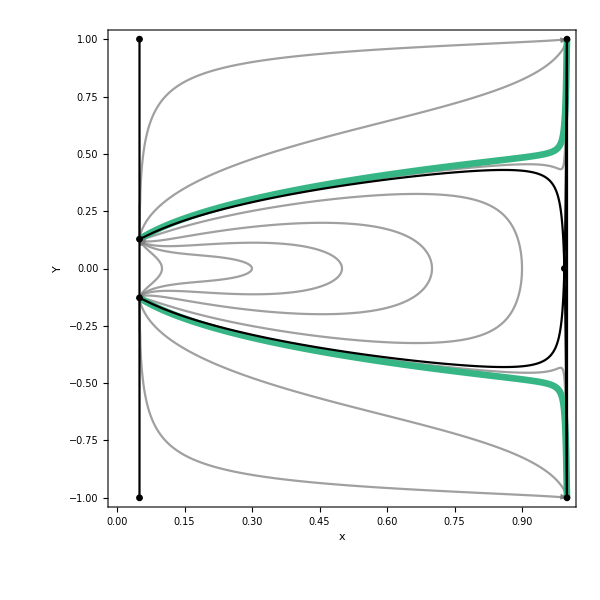

```mathematica
Z0SubMan=Show[trajZ0,FFSZ0,CFSZ0,FPShowZ0,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600},PlotRange->{{0,1},{-1,1}}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\Z0SubMan.pdf",Z0SubMan]*)
```

#### Potential

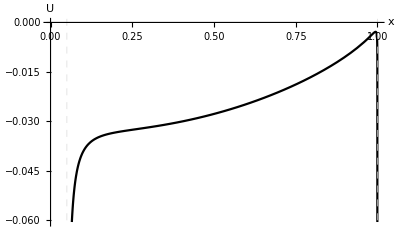

```mathematica
(*Plot the potential for this case*)
UZ0=Plot[{USubMan[a[x,0.2],x,0,R[x,cr]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]]
```

## Y = 0 Submanifold

### Plot the 3D Submanifold

```mathematica
(*Trajectories for the phase space*)
(*Written in terms of z*)
Y0z[x_,x0_,Z0_,R_,R0_]=(1/(a[x,x0]^2))*(x0+Z0/(1-Z0)+R0/(1-R0))-x-R/(1-R);
```

```mathematica
(*Write in terms of compact Z*)
(*x' = Z' = V' = 0, so x = x0, Z = Z0 and V = r0*)
Y0Z=Simplify[Y0z[x0,x0,Z0,R0,R0]/(1+Y0z[x0,x0,Z0,R0,R0])]
```

1. Z0

```mathematica
(*Z is always a constant for any value of x and V, which are also always constants independent of each other*)
traj3DY0Z[Z0_]:=Z0
```

```mathematica
(*Similarly, we can write the above equation in terms of V*)
Y0r[x_,x0_,Z_,Z0_,R0_]=(1/(a[x0,x0]^2))*(x0+Z0/(1-Z0)+R0/(1-R0))-x-Z/(1-Z);
Y0R=Simplify[Y0r[x0,x0,Z0,Z0,R0]/(1+Y0r[x0,x0,Z0,Z0,R0])]
```

1. R0

```mathematica
(*V is always a constant for any value of x and Z, which are also always constants independent of each other*)
traj3DY0R[R0_]:=R0
```

```mathematica
Y0traj3D[1]=ParametricPlot3D[{x,traj3DY0Z[0.1],traj3DY0R[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[2]=ParametricPlot3D[{x,traj3DY0Z[0.1],traj3DY0R[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[3]=ParametricPlot3D[{x,traj3DY0Z[0.1],traj3DY0R[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[4]=ParametricPlot3D[{x,traj3DY0Z[0.1],traj3DY0R[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[5]=ParametricPlot3D[{x,traj3DY0Z[0.1],traj3DY0R[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[6]=ParametricPlot3D[{x,traj3DY0Z[0.3],traj3DY0R[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[7]=ParametricPlot3D[{x,traj3DY0Z[0.3],traj3DY0R[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[8]=ParametricPlot3D[{x,traj3DY0Z[0.3],traj3DY0R[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[9]=ParametricPlot3D[{x,traj3DY0Z[0.3],traj3DY0R[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[10]=ParametricPlot3D[{x,traj3DY0Z[0.3],traj3DY0R[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[11]=ParametricPlot3D[{x,traj3DY0Z[0.5],traj3DY0R[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[12]=ParametricPlot3D[{x,traj3DY0Z[0.5],traj3DY0R[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,0,0,-.02},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[13]=ParametricPlot3D[{x,traj3DY0Z[0.5],traj3DY0R[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[14]=ParametricPlot3D[{x,traj3DY0Z[0.5],traj3DY0R[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[15]=ParametricPlot3D[{x,traj3DY0Z[0.5],traj3DY0R[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[16]=ParametricPlot3D[{x,traj3DY0Z[0.7],traj3DY0R[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[17]=ParametricPlot3D[{x,traj3DY0Z[0.7],traj3DY0R[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0,-.02},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[18]=ParametricPlot3D[{x,traj3DY0Z[0.7],traj3DY0R[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[19]=ParametricPlot3D[{x,traj3DY0Z[0.7],traj3DY0R[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[20]=ParametricPlot3D[{x,traj3DY0Z[0.7],traj3DY0R[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[21]=ParametricPlot3D[{x,traj3DY0Z[0.9],traj3DY0R[0.1]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[22]=ParametricPlot3D[{x,traj3DY0Z[0.9],traj3DY0R[0.3]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[23]=ParametricPlot3D[{x,traj3DY0Z[0.9],traj3DY0R[0.5]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[24]=ParametricPlot3D[{x,traj3DY0Z[0.9],traj3DY0R[0.7]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0traj3D[25]=ParametricPlot3D[{x,traj3DY0Z[0.9],traj3DY0R[0.9]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3DY0=Table[Y0traj3D[i],{i,1,25}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
wSubMan[x,z,v]
```

1/6 (0.15-2 v-1.15 x+3 x^2-z)

```mathematica
(*Define wSubMan = 0 in terms of Z*)
zSepY0=z/.Simplify[Solve[wSubMan[x,z,R/(1-R)]==0,z]][[1]];

ZSepY0[x_,R_]=zSepY0/(1+zSepY0);
```

```mathematica
Sep3DY0=ParametricPlot3D[{x,ZSepY0[x,R],R},{x,0,1},{R,0,1},PlotStyle->{Cyan}];
```

```mathematica
(*Show all components of plot*)
Y0SubMan3D=Show[Traj3DY0,Sep3DY0,AxesLabel->{"x","Z","R"},ImageSize->{600,600},PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\Y0SubMan3D.pdf",Y0SubMan3D]*)
```

### Plot the V = 0 Sub-submanifold

```mathematica
(*Define trajectories for the sub-submanifold*)
(*Z = Z0 *)
trajY0R0[Z0_]:=Z0
```

```mathematica
Y0R0traj[1]=Plot[Evaluate[trajY0R0[0]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[2]=Plot[Evaluate[trajY0R0[0.2]],{x,0,0.5},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[3]=Plot[Evaluate[trajY0R0[0.4]],{x,0,0.65},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[4]=Plot[Evaluate[trajY0R0[0.6]],{x,0,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[5]=Plot[Evaluate[trajY0R0[0.8]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[6]=Plot[Evaluate[trajY0R0[1]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[7]=Plot[Evaluate[trajY0R0[0.2]],{x,0.5,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[8]=Plot[Evaluate[trajY0R0[0.4]],{x,0.65,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0R0traj[9]=Plot[Evaluate[trajY0R0[0.6]],{x,0.9,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajY0R0=Table[Y0R0traj[i],{i,1,9}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
SepY0R0=ContourPlot[{Z/(1-Z)==3*ℛ-(1+3*ℛ)*x+3*x^2},{x,0,1},{Z,0,1},ContourStyle->{Black},Frame->True,PlotRange->{{0,1},{-0.05,1.05}},PlotPoints->200];
```

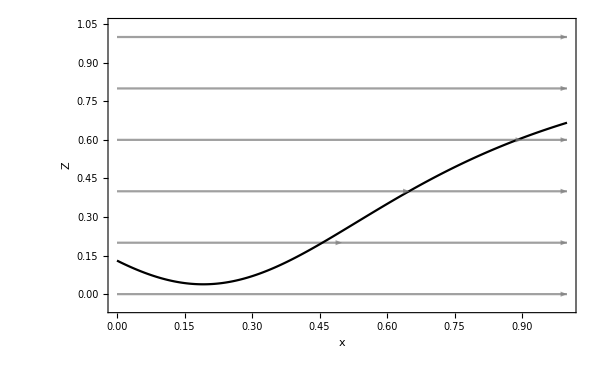

```mathematica
(*Show all components of plot*)
Y0SubManR0=Show[TrajY0R0,SepY0R0,FrameLabel->{"x","Z"},ImageSize->{600,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\Y0SubManR0.pdf",Y0SubManR0]*)
```

### Potential

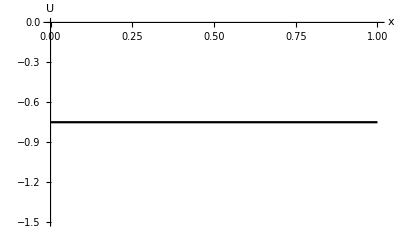

```mathematica
(*Plot the potential for this case*)
(*Y^2/(1-Y^2) + U = E --> U = E*)
UY0R0=Plot[{USubMan[a[x0,x0],0.5,0.8,0]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

### Plot the Z = 0 Sub-submanifold

```mathematica
(*R = R0 *)
trajY0Z0[R0_]:=R0
```

```mathematica
Y0Z0traj[1]=Plot[Evaluate[trajY0Z0[0]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[2]=Plot[Evaluate[trajY0Z0[0.2]],{x,0,0.5},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[3]=Plot[Evaluate[trajY0Z0[0.4]],{x,0,0.65},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[4]=Plot[Evaluate[trajY0Z0[0.6]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[5]=Plot[Evaluate[trajY0Z0[0.8]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[6]=Plot[Evaluate[trajY0Z0[1]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[7]=Plot[Evaluate[trajY0Z0[0.2]],{x,0.5,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Y0Z0traj[8]=Plot[Evaluate[trajY0Z0[0.4]],{x,0.65,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajY0Z0=Table[Y0Z0traj[i],{i,1,8}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
SepY0Z0=ContourPlot[{2*R/(1-R)==3*ℛ-(1+3*ℛ)*x+3*x^2},{x,0,1},{R,0,1},ContourStyle->{Black},Frame->True,PlotRange->{{0,1},{-0.05,1.05}},PlotPoints->200];
```

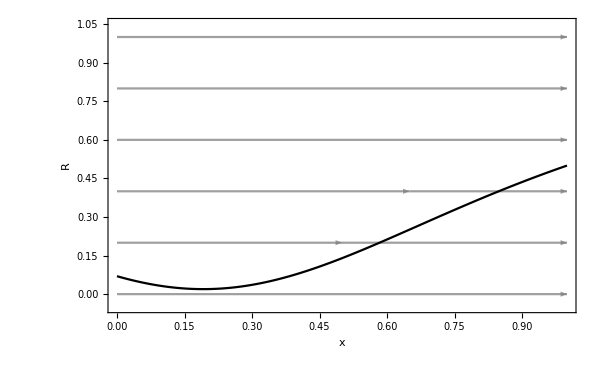

```mathematica
(*Show all components of plot*)
Y0SubManZ0=Show[TrajY0Z0,SepY0Z0,FrameLabel->{"x","R"},ImageSize->{600,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubManZ0.pdf",YSubManZ0]*)
```

### Potential

```mathematica
(*Plot the potential for this case*)
(*Y^2/(1-Y^2) + U = E --> U = E*)
UY0Z0=Plot[{USubMan[a[x0,x0],0.5,0,0.8]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

-Graphics-

## k = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
(*z in the flat case*)
zk0[Y_,x_]=3*Y^2/(1-Y^2)-x-r[x,cr];
```

```mathematica
(*Compact Z in the flat case*)
Zk0[Y_,x_]=zk0[Y,x]/Sqrt[1+zk0[Y,x]^2];
```

```mathematica
k0Y0=FindRoot[wSubMan[x,zk0[0,x],r[x,cr]]==0,{x,0.99}];
```

```mathematica
k0Y0=x/.k0Y0
```

0.997371

### Plot the 3D Submanifold

```mathematica
(*Defining ck, the first integral of z(x), for this case*)
ck[Y0_,x0_]=zk0[Y0,x0]*((1-x0)/(x0-ℛ))^(1/(1-ℛ));
```

```mathematica
(*Trajectories for the phase space*)
(*Define Y^2/(1-Y^2) = traj3Dk0*)
traj3Dk0[Y0_,x0_]=x/3+z[x,ck[Y0,x0]]/3+r[x,cr]/3;
```

```mathematica
(*Rearrange above equation for Y*)
traj3Dk0[Y0_,x0_]=Sqrt[traj3Dk0[Y0,x0]/(1+traj3Dk0[Y0,x0])];
```

```mathematica
k0traj3D[1]=ParametricPlot3D[{x,traj3Dk0[0,0.2],Zk0[traj3Dk0[0,0.2],x]},{x,0,k0Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[2]=ParametricPlot3D[{x,-traj3Dk0[0,0.2],Zk0[-traj3Dk0[0,0.2],x]},{x,0,k0Y0},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[3]=ParametricPlot3D[{x,traj3Dk0[0,0.2],Zk0[traj3Dk0[0,0.2],x]},{x,k0Y0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[4]=ParametricPlot3D[{x,-traj3Dk0[0,0.2],Zk0[-traj3Dk0[0,0.2],x]},{x,k0Y0,1},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[5]=ParametricPlot3D[{x,traj3Dk0[0,0.6],Zk0[traj3Dk0[0,0.6],x]},{x,0,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[6]=ParametricPlot3D[{x,-traj3Dk0[0,0.6],Zk0[-traj3Dk0[0,0.6],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[7]=ParametricPlot3D[{x,traj3Dk0[0,0.9],Zk0[traj3Dk0[0,0.9],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[8]=ParametricPlot3D[{x,-traj3Dk0[0,0.9],Zk0[-traj3Dk0[0,0.9],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[9]=ParametricPlot3D[{x,traj3Dk0[0.4,0.45],Zk0[traj3Dk0[0.4,0.45],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[10]=ParametricPlot3D[{x,-traj3Dk0[0.4,0.45],Zk0[-traj3Dk0[0.4,0.45],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[11]=ParametricPlot3D[{x,traj3Dk0[0.9,0.3],Zk0[traj3Dk0[0.9,0.3],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[12]=ParametricPlot3D[{x,-traj3Dk0[0.9,0.3],Zk0[-traj3Dk0[0.9,0.3],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[13]=ParametricPlot3D[{x,traj3Dk0[0.75,0.5],Zk0[traj3Dk0[0.75,0.5],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[14]=ParametricPlot3D[{x,-traj3Dk0[0.75,0.5],Zk0[-traj3Dk0[0.75,0.5],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[15]=ParametricPlot3D[{x,traj3Dk0[0.48,0.95],Zk0[traj3Dk0[0.48,0.95],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[16]=ParametricPlot3D[{x,-traj3Dk0[0.48,0.95],Zk0[-traj3Dk0[0.48,0.95],x]},{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Traj3Dk0=Table[k0traj3D[i],{i,1,16}];
```

```mathematica
(*Separatrix where Z = 0*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
Sep3Dk0=ParametricPlot3D[{{x,Sqrt[(x+r[x,cr])/(3+x+r[x,cr])],r[x,cr]},{x,-Sqrt[(x+r[x,cr])/(3+x+r[x,cr])],r[x,cr]}},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the separatrix for the fixed point where Y = 0*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFS3Dk0=ParametricPlot3D[{{x,traj3Dk0[0,k0Y0],Zk0[traj3Dk0[0,k0Y0],x]},{x,-traj3Dk0[0,k0Y0],Zk0[traj3Dk0[0,k0Y0],x]}},{x,0,1},PlotStyle->{Black},PlotRange->{{0,1},{-1,1},{-2,1}}];
```

```mathematica
(*Fixed points of the system*)
FPShow3Dk0=ListPointPlot3D[{{1,1,1},{1,-1,1},{1,1,-1},{1,-1,-1},{ℛ,1,0},{ℛ,-1,0},{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{k0Y0,0,Zk0[0,k0Y0]}},PlotStyle->{Black},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Show all components of plot*)
k0SubMan3D=Show[Traj3Dk0,Sep3Dk0,CFS3Dk0,FPShow3Dk0,AxesLabel->{"x","Y","Z"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\k0SubMan3D.pdf",k0SubMan3D]*)
```

### Plot the Projected x-Y Submanifold

```mathematica
(*Trajectories for the phase space*)
trajk0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,ck[Y0,x0]]/3+r[x,cr]/3;
```

```mathematica
k0traj[1]=ContourPlot[Evaluate[trajk0[0,0.2]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[2]=ContourPlot[Evaluate[trajk0[0,0.6]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[3]=ContourPlot[Evaluate[trajk0[0,0.9]],{x,0,k0Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[4]=ContourPlot[Evaluate[trajk0[0,0.9]],{x,k0Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[5]=ContourPlot[Evaluate[trajk0[0.4,0.45]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[6]=ContourPlot[Evaluate[trajk0[0.4,0.45]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[7]=ContourPlot[Evaluate[trajk0[0.9,0.3]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[8]=ContourPlot[Evaluate[trajk0[0.9,0.3]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[9]=ContourPlot[Evaluate[trajk0[0.75,0.5]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[10]=ContourPlot[Evaluate[trajk0[0.75,0.5]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[11]=ContourPlot[Evaluate[trajk0[0.48,0.95]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[12]=ContourPlot[Evaluate[trajk0[0.48,0.95]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajk0=Table[k0traj[i],{i,1,12}];
```

```mathematica
(*Separatrix where z = 0*)
Sepk0=ContourPlot[{3*Y^2/(1-Y^2)-x-r[x,cr]==0},{x,0,1},{Y,-1,1},ContourStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]},PlotPoints->100];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSk0=Plot[{traj3Dk0[0,k0Y0],-traj3Dk0[0,k0Y0]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Fixed points of the system*)
FPShowk0=ListPlot[{{1,1},{1,-1},{ℛ,1},{ℛ,-1},{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{k0Y0,0}},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}, PlotStyle->{Black}];
```

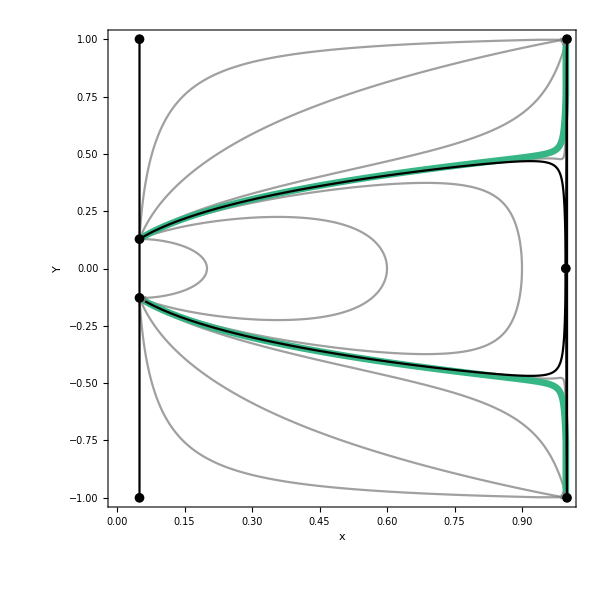

```mathematica
(*Show all components of plot*)
k0SubMan=Show[trajk0,Sepk0,CFSk0,FPShowk0,Sepx,FrameLabel->{"x",Rotate["Y",300]},ImageSize->{600,600}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\k0SubMan.pdf",k0SubMan]*)
```

### Potential

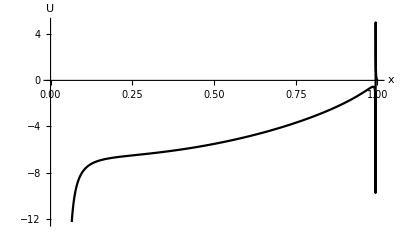

```mathematica
(*Plot the potential for this case*)
Uk0=Plot[{USubMan[a[x,k0Y0],x,z[x,ck[0,k0Y0]]/Sqrt[1+z[x,ck[0,k0Y0]]^2],r[x,cr]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black}]
```

## x-Y Phase Spaces and Potentials

## Set-up

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = Y^2/(1-Y^2)*)
ffs=(1/3)*(x+z[x,c]+r[x,cr]);
```

```mathematica
(*Rearrange for Y*)
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Set up the plot for the x = ℛ and x = 1 separatrices*)
Sep=ContourPlot[{x==ℛ,x==1},{x,0,1},{Y,-1,1},ContourStyle->{Black}];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = Y^2/(1-Y^2)*)
cfs[x0_]= x/3+z[x,c]/3+r[x,cr]/3-(x0/3+z[x0,c]/3+r[x0,cr]/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange above equation for Y*)
CFS[x0_]=Sqrt[cfs[x0]/(1+cfs[x0])];
```

```mathematica
(*Set up plot for the common fixed points*)
FPShow=ListPlot[{{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{ℛ,1},{ℛ,-1},{1,1},{1,-1}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration*)
Accn=z[x,c]+2*r[x,cr]-3*ℛ+(1+3*ℛ)*x-3*x^2;
```

### Potentials

```mathematica
(*Define the potential*)
U[x_,x0_]=-a[x,x0]^2*(x/6+z[x,c]/6+r[x,cr]/6);
```

```mathematica
(*Find the first derivative of U with respect to x*)
dUdx=Simplify[D[U[x,x0],x]];
```

```mathematica
(*Find the second derivative of U with respect to x*)
d2Udx2[x_,x0_]=Simplify[D[U[x,x0],{x,2}]];
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,Y0_]=-(x0/6+z[x0,c]/6+r[x0,cr]/6-Y0^2/(2*(1-Y0^2)));
```

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc1[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[1]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[1]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75],Dashing[{Small,Small,Small,Small}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75],Dashing[{Small,Small,Small,Small}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75],Dashing[{Medium,Medium,Medium,Medium}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75],Dashing[{Medium,Medium,Medium,Medium}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0,0.9},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75],Dashing[{Large,Large,Large,Large}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75],Dashing[{Large,Large,Large,Large}]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75],DotDashed}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75],DotDashed}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75],PlotMarkers->"Circle"}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75],PlotMarkers->"Graphics`PlotMarkers[][[6]]"}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1=Plot[{FFS[[1]],-FFS[[1]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1=Plot[{CFS[xOneEinsteinPointc1][[1]],-CFS[xOneEinsteinPointc1][[1]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1=ListPlot[{{xOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

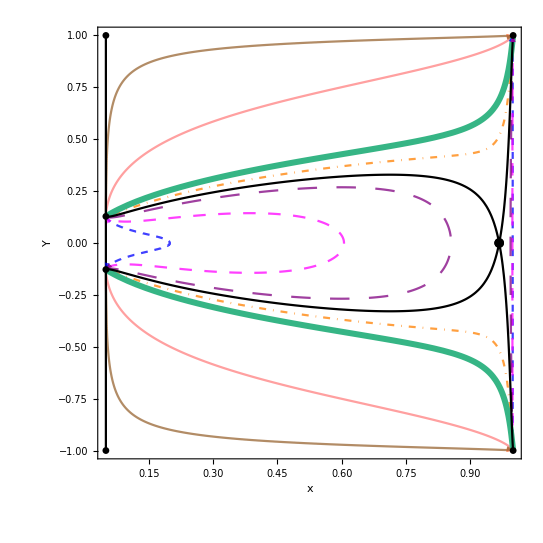

```mathematica
(*Show all components of plots*)
PhaseSpacec1=Show[Trajc1,FFSc1,CFSc1,Einsteinc1,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc1,0.2][[1]]
```

-3.25213

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[x,0.2][[1]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dotted]];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{x,0.05,0.2},PlotStyle->{Blue,Opacity[0.75],Dashing[{Small,Small,Small,Small}]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0.12][[1]]},{x,0.05,0.6},PlotStyle->{Magenta,Opacity[0.75],Dashing[{Medium,Medium,Medium,Medium}]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.18][[1]]},{x,0.05,0.85},PlotStyle->{Purple,Opacity[0.75],Dashing[{Large,Large,Large,Large}]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.225][[1]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0.5][[1]]},{x,0.05,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.9][[1]]},{x,0.05,1},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energy[7]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[8]=Plot[{Energy[0.2,0][[1]]},{x,0.2,1},PlotStyle->{Black,Dotted,Opacity[0.75]}];
```

```mathematica
c1Energy[9]=Plot[{Energy[0.2,0.12][[1]]},{x,0.6,1},PlotStyle->{Black,Dotted,Opacity[0.75]}];
```

```mathematica
c1Energy[10]=Plot[{Energy[0.2,0.18][[1]]},{x,0.85,1},PlotStyle->{Black,Dotted,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,10}];
```

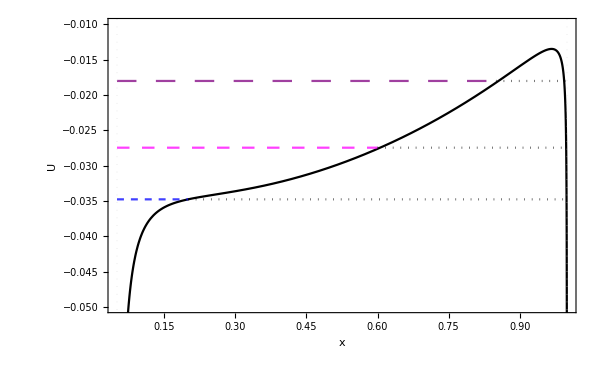

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,ImageSize->{600,400},PlotRangePadding->{0.04,0},BaseStyle->{FontSize->14},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},PlotRange->{{0.05,1},{-0.05,-0.01}}]
```

### Final Plot

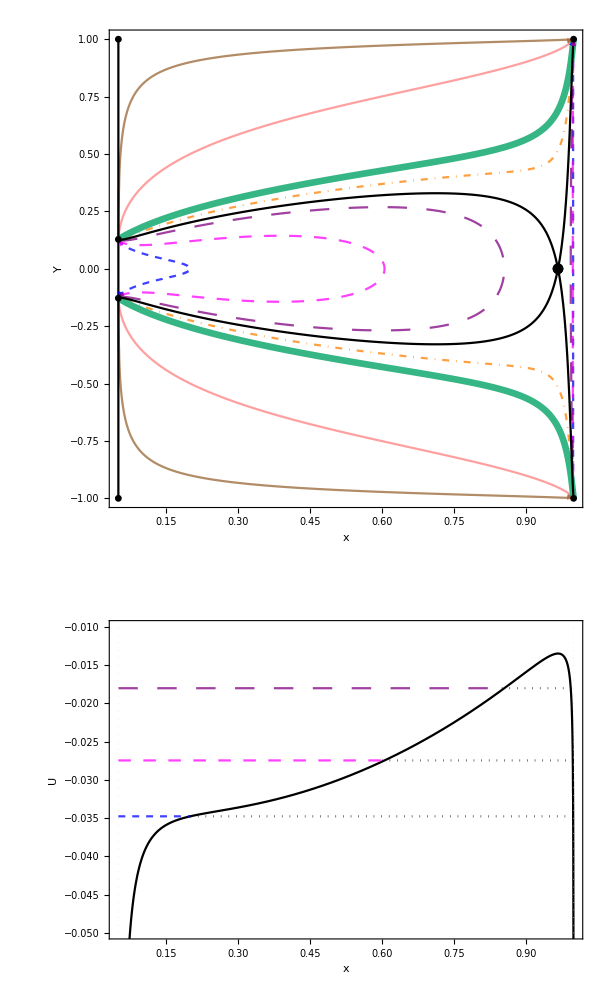

```mathematica
(*Plot the phase space and potential together*)
xYc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc1.pdf",xYc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc2[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[2]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[2]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0,0.6},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.13,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[9]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[10]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[11]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2=Plot[{FFS[[2]],-FFS[[2]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2=Plot[{CFS[xTwoEinsteinPointsc2][[2]],-CFS[xTwoEinsteinPointsc2][[2]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{xTwoEinsteinPointsc2[[1]],0},{xTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

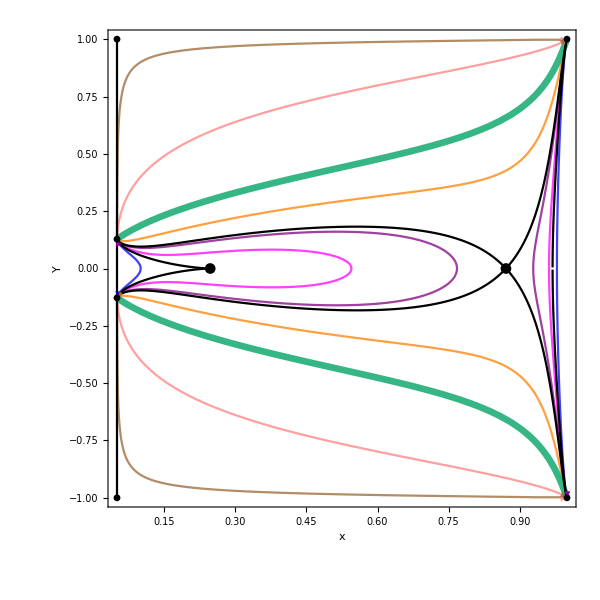

```mathematica
(*Show all components of plots*)
PhaseSpacec2=Show[Trajc2, FFSc2,CFSc2,Einsteinc2,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc2[[1]],0.1][[2]]
```

-5.42565×10^-9

```mathematica
d2Udx2[xTwoEinsteinPointsc2[[2]],0.1][[2]]
```

-0.177947

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[x,0.1][[2]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{x,0.05,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0][[2]]},{x,0.98,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.07][[2]]},{x,0.05,0.54},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.07][[2]]},{x,0.965,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0.09][[2]]},{x,0.05,0.765},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.09][[2]]},{x,0.93,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.13][[2]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.4][[2]]},{x,0.05,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energy[9]=Plot[{Energy[0.1,0.9][[2]]},{x,0.05,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energy[10]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[11]=Plot[{Energy[0.1,0][[2]]},{x,0.1,0.98},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[12]=Plot[{Energy[0.1,0.07][[2]]},{x,0.54,0.965},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[13]=Plot[{Energy[0.1,0.09][[2]]},{x,0.765,0.93},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,13}];
```

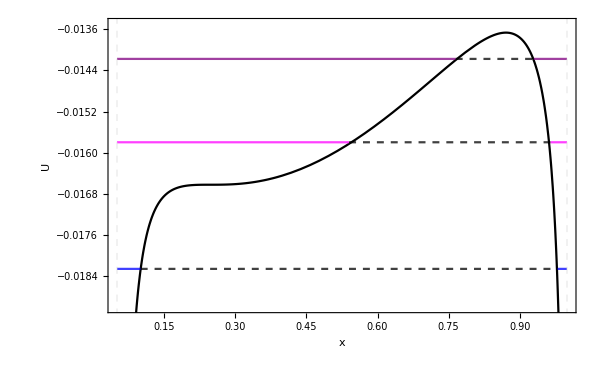

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-0.019,-0.0135}}]
```

### Final Plot

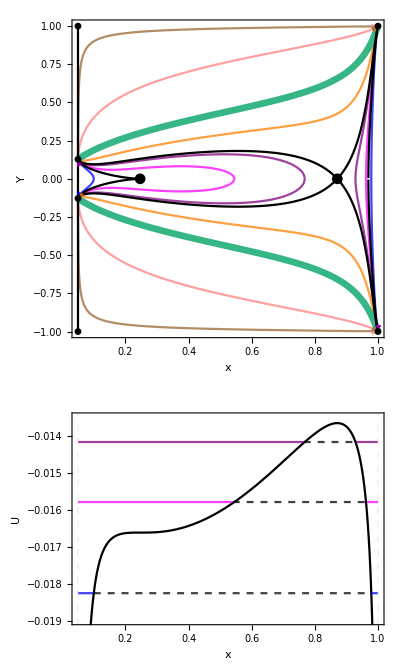

```mathematica
(*Plot the phase space and potential together*)
xYc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc2.pdf",xYc2]*)
```

## Three Einstein Points: c3

```mathematica
(*This is the case where there is an extra bouncing regime*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc3[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[3]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.2,0.5},{Y,-1,1},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[10]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[11]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[12]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[13]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3=Plot[{FFS[[3]],-FFS[[3]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3=Plot[{CFS[xThreeEinsteinPointsc3][[3]],-CFS[xThreeEinsteinPointsc3][[3]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->600];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{xThreeEinsteinPointsc3[[1]],0},{xThreeEinsteinPointsc3[[2]],0},{xThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

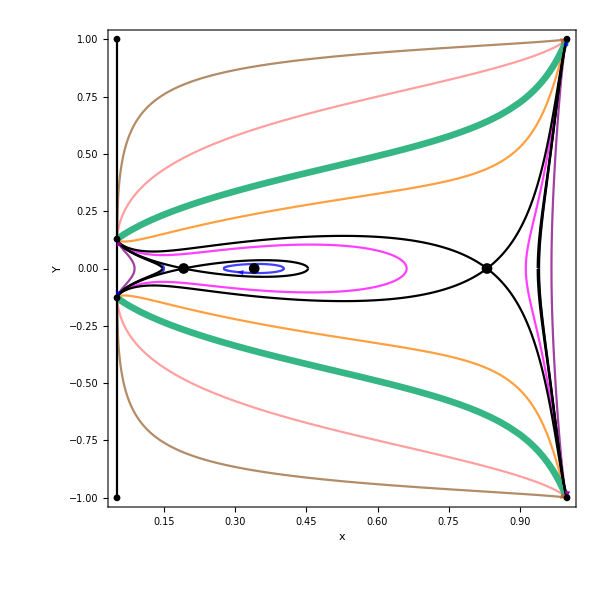

```mathematica
(*Show all components of plots*)
PhaseSpacec3=Show[Trajc3, FFSc3,CFSc3,Einsteinc3,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc3[[1]],0.155][[3]]
```

-0.136796

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[2]],0.155][[3]]
```

0.0402181

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[3]],0.155][[3]]
```

-0.192864

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[x,0.08][[3]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed],PlotRange->{-0.016,-0.0105}];
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0.071][[3]]},{x,0.05,0.15},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.071][[3]]},{x,0.275,0.4},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.071][[3]]},{x,0.94,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.08][[3]]},{x,0.05,0.655},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.08][[3]]},{x,0.92,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0.04][[3]]},{x,0.05,0.09},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.04][[3]]},{x,0.97,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.12][[3]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.3][[3]]},{x,0.05,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.6][[3]]},{x,0.05,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energy[11]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[12]=Plot[{Energy[0.08,0.071][[3]]},{x,0.15,0.275},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[13]=Plot[{Energy[0.08,0.071][[3]]},{x,0.4,0.94},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[14]=Plot[{Energy[0.08,0.08][[3]]},{x,0.655,0.92},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[15]=Plot[{Energy[0.08,0.04][[3]]},{x,0.09,0.97},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,15}];
```

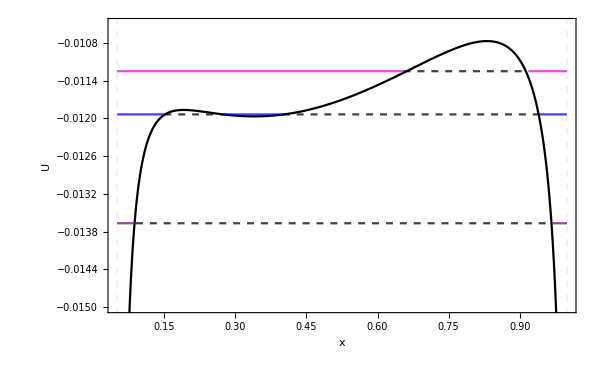

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-0.015,-0.0105}}]
```

### Final Plot

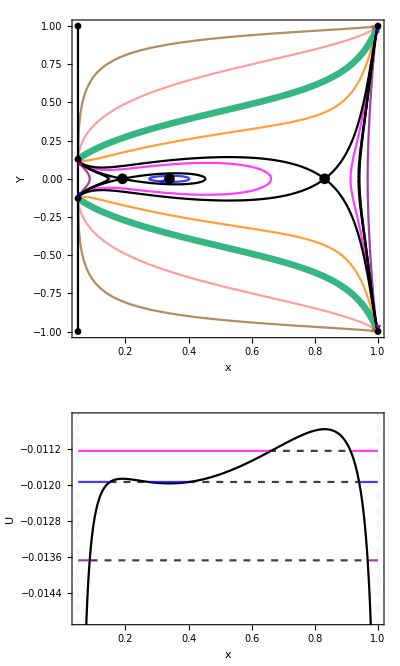

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc3.pdf",xYc3]*)
```

## Three Einstein Points: c4

```mathematica
(*This is the limiting 3 Einstein point case*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc4[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[4]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[4]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c4traj[1]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[2]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[3]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[4]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0,0.3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[5]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[6]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[7]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[8]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[9]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[10]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[11]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc4=Table[c4traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4=Plot[{FFS[[4]],-FFS[[4]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4=Plot[{CFS[xThreeEinsteinPointsc4][[4]],-CFS[xThreeEinsteinPointsc4][[4]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4=ListPlot[{{xThreeEinsteinPointsc4[[1]],0},{xThreeEinsteinPointsc4[[2]],0},{xThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc4=ContourPlot[Accn[[4]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

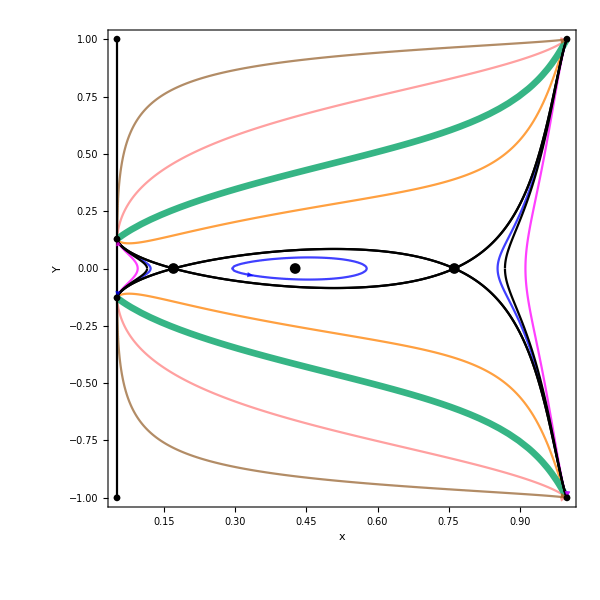

```mathematica
(*Show all components of plots*)
PhaseSpacec4=Show[Trajc4, FFSc4,CFSc4,Einsteinc4,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc4[[1]],0.08][[4]]
```

-0.109509

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[2]],0.08][[4]]
```

0.0143208

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[3]],0.08][[4]]
```

-0.0356306

```mathematica
(*Plot the potential for this case*)
Uc4=Plot[{U[x,0.08][[4]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c4Energy[1]=Plot[{Energy[0.08,0.065][[4]]},{x,0.05,0.12},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[2]=Plot[{Energy[0.08,0.065][[4]]},{x,0.3,0.57},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[3]=Plot[{Energy[0.08,0.065][[4]]},{x,0.855,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[4]=Plot[{Energy[0.08,0.05][[4]]},{x,0.05,0.095},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[5]=Plot[{Energy[0.08,0.05][[4]]},{x,0.91,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[6]=Plot[{Energy[0.08,0.11][[4]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energy[7]=Plot[{Energy[0.08,0.3][[4]]},{x,0.05,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energy[8]=Plot[{Energy[0.08,0.6][[4]]},{x,0.05,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energy[9]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energy[10]=Plot[{Energy[0.08,0.065][[4]]},{x,0.12,0.3},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[11]=Plot[{Energy[0.08,0.065][[4]]},{x,0.57,0.855},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[12]=Plot[{Energy[0.08,0.05][[4]]},{x,0.095,0.91},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4=Table[c4Energy[i],{i,1,12}];
```

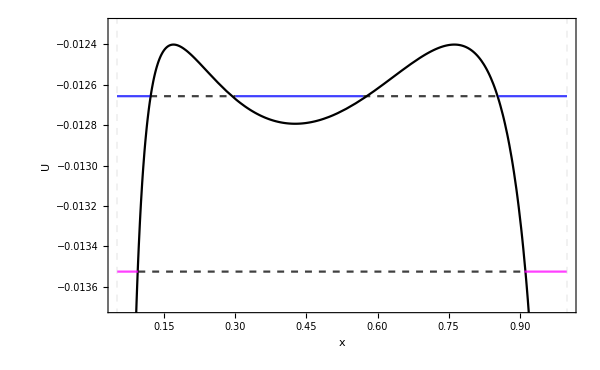

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4=Show[Uc4,Energyc4,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-0.0137,-0.0123}}]
```

### Final Plot

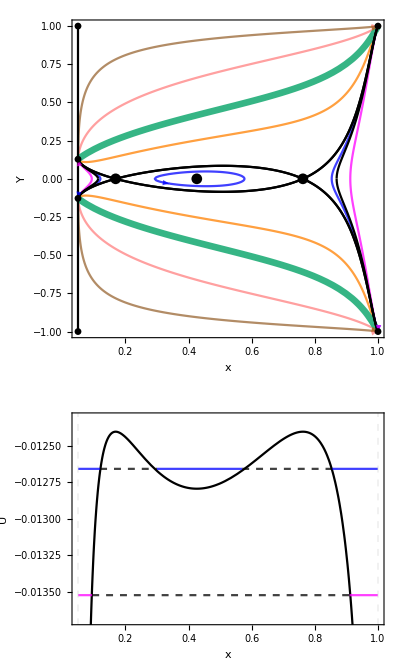

```mathematica
(*Plot the phase space and potential together*)
xYc4=GraphicsColumn[{PhaseSpacec4,Potentialc4},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc4.pdf",xYc4]*)
```

## Three Einstein Points: c5

```mathematica
(*The case with an extra turn-around region*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc5[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[5]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[5]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c5traj[1]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[2]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[3]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[4]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[5]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[6]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[7]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[8]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[9]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[10]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[11]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[12]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[13]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc5=Table[c5traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5=Plot[{FFS[[5]],-FFS[[5]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5=Plot[{CFS[xThreeEinsteinPointsc5][[5]],-CFS[xThreeEinsteinPointsc5][[5]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5=ListPlot[{{xThreeEinsteinPointsc5[[1]],0},{xThreeEinsteinPointsc5[[2]],0},{xThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc5=ContourPlot[Accn[[5]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

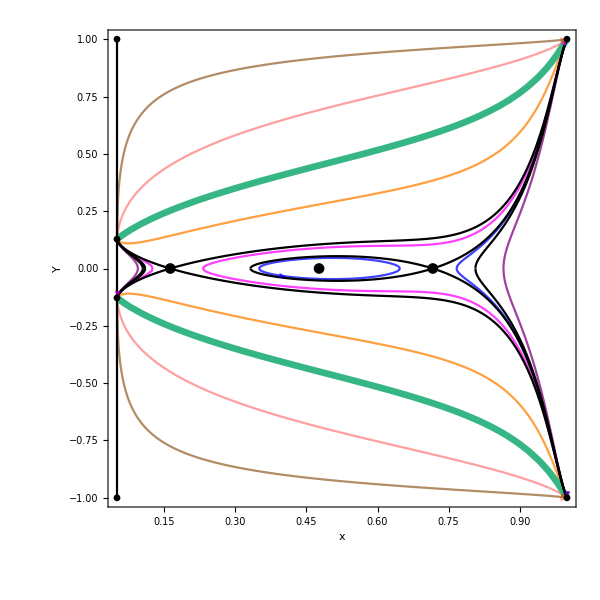

```mathematica
(*Show all components of plots*)
PhaseSpacec5=Show[Trajc5, FFSc5,CFSc5,Einsteinc5,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc5[[1]],0.08][[5]]
```

-0.136758

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[2]],0.08][[5]]
```

0.0114056

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[3]],0.08][[5]]
```

-0.0211506

```mathematica
(*Plot the potential for this case*)
Uc5=Plot[{U[x,0.08][[5]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c5Energy[1]=Plot[{Energy[0.08,0.06][[5]]},{x,0.05,0.11},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[2]=Plot[{Energy[0.08,0.06][[5]]},{x,0.355,0.63},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[3]=Plot[{Energy[0.08,0.06][[5]]},{x,0.775,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[4]=Plot[{Energy[0.08,0.065][[5]]},{x,0.235,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[5]=Plot[{Energy[0.08,0.065][[5]]},{x,0.05,0.125},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[6]=Plot[{Energy[0.08,0.05][[5]]},{x,0.87,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[7]=Plot[{Energy[0.08,0.05][[5]]},{x,0.05,0.095},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[8]=Plot[{Energy[0.08,0.11][[5]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energy[9]=Plot[{Energy[0.08,0.3][[5]]},{x,0.05,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energy[10]=Plot[{Energy[0.08,0.6][[5]]},{x,0.05,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energy[11]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energy[12]=Plot[{Energy[0.08,0.06][[5]]},{x,0.11,0.355},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[13]=Plot[{Energy[0.08,0.06][[5]]},{x,0.63,0.775},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[14]=Plot[{Energy[0.08,0.065][[5]]},{x,0.125,0.235},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[15]=Plot[{Energy[0.08,0.05][[5]]},{x,0.095,0.87},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5=Table[c5Energy[i],{i,1,15}];
```

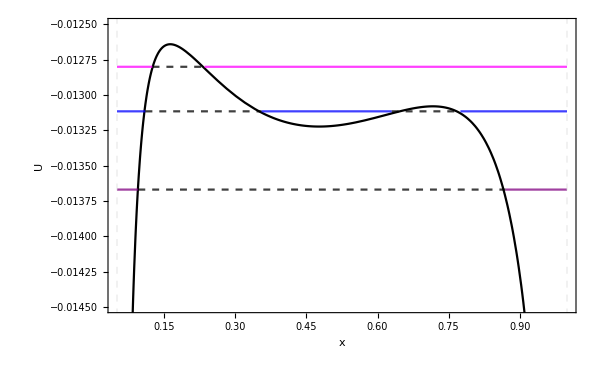

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5=Show[Uc5,Energyc5,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-0.0145,-0.0125}}]
```

### Final Plot

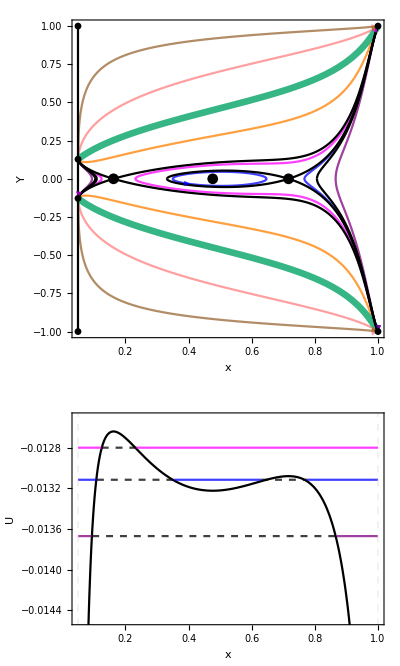

```mathematica
(*Plot the phase space and potential together*)
xYc5=GraphicsColumn[{PhaseSpacec5,Potentialc5},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc5.pdf",xYc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc6[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[6]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[6]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c6traj[1]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[2]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[3]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[4]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0.3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[5]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[6]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[7]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[8]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[9]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[10]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc6=Table[c6traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6=Plot[{FFS[[6]],-FFS[[6]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6=Plot[{CFS[xTwoEinsteinPointsc6][[6]],-CFS[xTwoEinsteinPointsc6][[6]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6=ListPlot[{{xTwoEinsteinPointsc6[[1]],0},{xTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc6=ContourPlot[Accn[[6]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

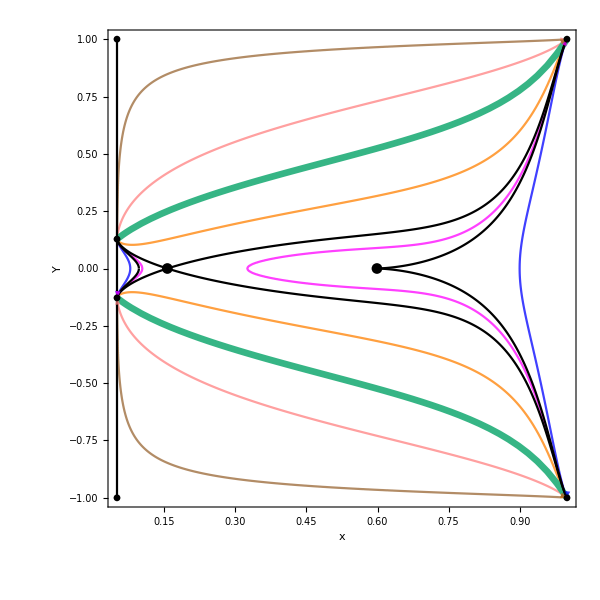

```mathematica
(*Show all components of plots*)
PhaseSpacec6=Show[Trajc6, FFSc6,CFSc6,Einsteinc6,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc6[[1]],0.9][[6]]
```

-8.29826

```mathematica
d2Udx2[xTwoEinsteinPointsc6[[2]],0.9][[6]]
```

-8.91239×10^-8

```mathematica
(*Plot the potential for this case*)
Uc6=Plot[{U[x,0.9][[6]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c6Energy[1]=Plot[{Energy[0.9,0][[6]]},{x,0.05,0.07},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[2]=Plot[{Energy[0.9,0][[6]]},{x,0.9,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[3]=Plot[{Energy[0.9,0.4][[6]]},{x,0.05,0.105},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[4]=Plot[{Energy[0.9,0.4][[6]]},{x,0.322,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[5]=Plot[{Energy[0.9,0.6][[6]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energy[6]=Plot[{Energy[0.9,0.9][[6]]},{x,0.05,1},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[7]=Plot[{Energy[0.9,0.99][[6]]},{x,0.05,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energy[8]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energy[9]=Plot[{Energy[0.9,0][[6]]},{x,0.07,0.9},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[10]=Plot[{Energy[0.9,0.4][[6]]},{x,0.105,0.322},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6=Table[c6Energy[i],{i,1,10}];
```

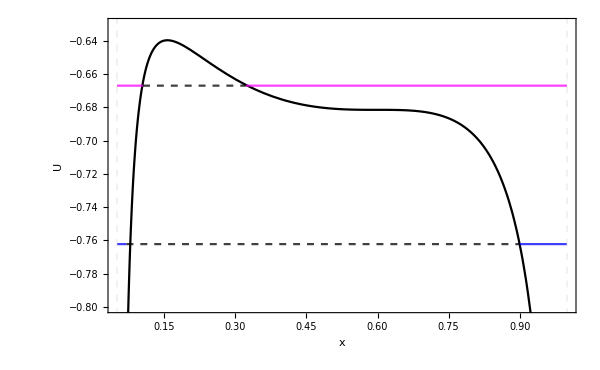

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6=Show[Uc6,Energyc6,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-0.8,-0.63}}]
```

### Final Plot

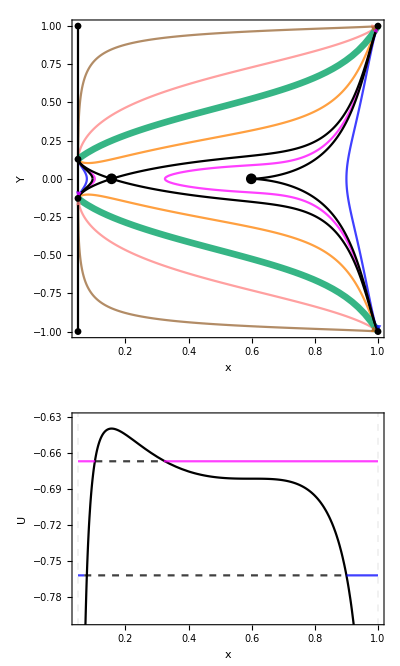

```mathematica
(*Plot the phase space and potential together*)
xYc6=GraphicsColumn[{PhaseSpacec6,Potentialc6},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc6.pdf",xYc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc7[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[7]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[7]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7=Plot[{FFS[[7]],-FFS[[7]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7=Plot[{CFS[xOneEinsteinPointc7][[7]],-CFS[xOneEinsteinPointc7][[7]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{xOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

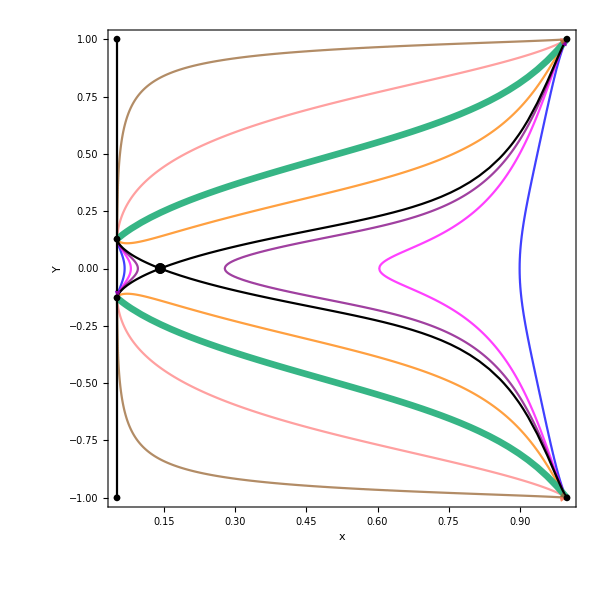

```mathematica
(*Show all components of plots*)
PhaseSpacec7=Show[Trajc7, FFSc7,CFSc7,Einsteinc7,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc7,0.9][[7]]
```

-13.8623

```mathematica
(*Plot the potential for this case*)
Uc7=Plot[{U[x,0.9][[7]]},{x,ℛ,1},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c7Energy[1]=Plot[{Energy[0.9,0][[7]]},{x,0.9,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[2]=Plot[{Energy[0.9,0][[7]]},{x,0.05,0.06},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[3]=Plot[{Energy[0.9,0.5][[7]]},{x,0.6,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[4]=Plot[{Energy[0.9,0.5][[7]]},{x,0.05,0.08},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[5]=Plot[{Energy[0.9,0.56][[7]]},{x,0.275,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[6]=Plot[{Energy[0.9,0.56][[7]]},{x,0.05,0.099},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[7]=Plot[{Energy[0.9,0.7][[7]]},{x,0.05,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energy[8]=Plot[{Energy[0.9,0.92][[7]]},{x,0.2,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energy[9]=Plot[{Energy[0.9,0.99][[7]]},{x,0.6,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energy[10]=Plot[{0},{x,0.05,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energy[11]=Plot[{Energy[0.9,0][[7]]},{x,0.06,0.9},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[12]=Plot[{Energy[0.9,0.5][[7]]},{x,0.08,0.6},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[13]=Plot[{Energy[0.9,0.56][[7]]},{x,0.099,0.275},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7=Table[c7Energy[i],{i,1,13}];
```

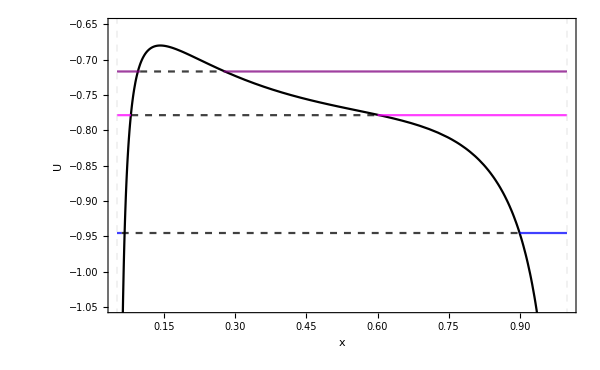

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7=Show[Uc7,Energyc7,ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{"x",Rotate["U",270Degree]},BaseStyle->{FontSize->14},PlotRange->{{0.05,1},{-1.05,-0.65}}]
```

### Final Plot

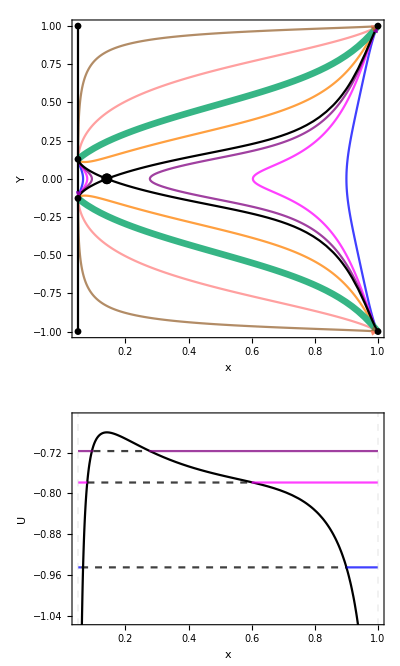

```mathematica
(*Plot the phase space and potential together*)
xYc7=GraphicsColumn[{PhaseSpacec7,Potentialc7},Spacings->{0,0}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc7.pdf",xYc7]*)
```

## 3D x-Y-Z Phase Spaces

## Set-up for x-Y-Z Phase Spaces

```mathematica
(*Use Friedmann equation (first integral) to plot the trajectories*)
(*First define Y^2/(1-Y^2) = trajxYZ*)
trajxYZ[Y0_,x0_]:=x/3+z[x,c]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
trajxYZ[Y0_,x0_]=Sqrt[trajxYZ[Y0,x0]/(1+trajxYZ[Y0,x0])];
```

```mathematica
(*Set up plot for the common fixed points*)
FPShowxYZ=ListPointPlot3D[{{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,1,0},{ℛ,-1,0},{1,1,1},{1,-1,1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the surface where accn = 0*)
AccnxYZ=ContourPlot3D[Z/(1-Z)+x+2*r[x,cr]-3*ℛ+3*ℛ*x-3*x^2==0,{x,0,1},{Y,-1,1},{Z,0,1}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

## One Einstein Point: c1

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c1trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc1=Table[c1trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc1=ListPointPlot3D[{{xOneEinsteinPointc1,0,ZOneEinsteinPointc1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc1=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]},{x,-CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc1=ParametricPlot3D[{{x,FFS[[1]],Z[x,c[[1]]]},{x,-FFS[[1]],Z[x,c[[1]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec1=ParametricPlot3D[{x,Y,Z[x,c[[1]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc1=Show[CFSc1,FFSc1, Einsteinc1,FPShowxYZ,Surfacec1,trajc1,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc1.pdf",xYZc1]*)
```

## Two Einstein Points: c2

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c2trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc2=Table[c2trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc2=ListPointPlot3D[{{xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]]},{xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc2=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc2=ParametricPlot3D[{{x,FFS[[2]],Z[x,c[[2]]]},{x,-FFS[[2]],Z[x,c[[2]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec2=ParametricPlot3D[{x,Y,Z[x,c[[2]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc2=Show[CFSc2,FFSc2, Einsteinc2,FPShowxYZ,Surfacec2,trajc2,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc2.pdf",xYZc2]*)
```

## Three Einstein Points: c3

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c3trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc3=Table[c3trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc3=ListPointPlot3D[{{xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]]},{xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]]},{xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc3=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc3=ParametricPlot3D[{{x,FFS[[3]],Z[x,c[[3]]]},{x,-FFS[[3]],Z[x,c[[3]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec3=ParametricPlot3D[{x,Y,Z[x,c[[3]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc3=Show[CFSc3,FFSc3, Einsteinc3,FPShowxYZ,Surfacec3,trajc3,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc3.pdf",xYZc3]*)
```

## Three Einstein Points: c4

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
(*Plotting trajectories with different values of k*)
c4trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[3]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[4]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[9]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[10]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[11]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[12]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[13]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[14]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajc4=Table[c4trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc4=ListPointPlot3D[{{xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]]},{xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]]},{xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc4=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc4=ParametricPlot3D[{{x,FFS[[4]],Z[x,c[[4]]]},{x,-FFS[[4]],Z[x,c[[4]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec4=ParametricPlot3D[{x,Y,Z[x,c[[4]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc4=Show[CFSc4,FFSc4, Einsteinc4,FPShowxYZ,Surfacec4,trajc4,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc4.pdf",xYZc4]*)
```

## Three Einstein Points: c5

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
(*Plotting trajectories with different values of k*)
c5trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc5=Table[c5trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc5=ListPointPlot3D[{{xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]]},{xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]]},{xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc5=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc5=ParametricPlot3D[{{x,FFS[[5]],Z[x,c[[5]]]},{x,-FFS[[5]],Z[x,c[[5]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec5=ParametricPlot3D[{x,Y,Z[x,c[[5]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc5=Show[CFSc5,FFSc5, Einsteinc5,FPShowxYZ,Surfacec5,trajc5,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc5.pdf",xYZc5]*)
```

## Two Einstein Points: c6

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c6trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc6=Table[c6trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc6=ListPointPlot3D[{{xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]]},{xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc6=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc6=ParametricPlot3D[{{x,FFS[[6]],Z[x,c[[6]]]},{x,-FFS[[6]],Z[x,c[[6]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec6=ParametricPlot3D[{x,Y,Z[x,c[[6]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc6=Show[CFSc6,FFSc6, Einsteinc6,FPShowxYZ,Surfacec6,trajc6,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc6.pdf",xYZc6]*)
```

## One Einstein Point: c7

```mathematica
(*Plot the trajectories*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
```

```mathematica
c7trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,0,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc7=Table[c7trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc7=ListPointPlot3D[{{xOneEinsteinPointc7,0,ZOneEinsteinPointc7}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
(*Need to plot + and - as square root taken for Y part, and Mathematica only takes + as default*)
CFSc7=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]},{x,-CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]}},{x,0,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Flat Friedmann Separatrix*)
(*Two plots needed as sqrt taken for Y part, so + and - parts need plotting separately*)
FFSc7=ParametricPlot3D[{{x,FFS[[7]],Z[x,c[[7]]]},{x,-FFS[[7]],Z[x,c[[7]]]}},{x,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the c surface*)
Surfacec7=ParametricPlot3D[{x,Y,Z[x,c[[7]]]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
xYZc7=Show[CFSc7,FFSc7, Einsteinc7,FPShowxYZ,Surfacec7,trajc7,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xYZ_Plots\\xYZc7.pdf",xYZc7]*)
```

## a-y Phase Spaces and Potentials

## Set-up

### Variables in terms of a

```mathematica
(*Dark matter (z), radiation (r) and dark energy x written in terms of the scale factor a*)
xa[a_,x0_]=(a^(-3*(1-ℛ))+ca[x0]*ℛ)/(a^(-3*(1-ℛ))+ca[x0]);

za[a_,x0_,c_]=c*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(1/(1-ℛ));

ra[a_,x0_,cr_]=cr*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(4/(3*(1-ℛ)));
```

```mathematica
(*Define w(a), the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
wa[a_,x0_,c_,cr_]=za[a,x0,c]+2*ra[a,x0,cr]-3*ℛ+xa[a,x0]*(1+3*ℛ)-3*xa[a,x0]^2;
```

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = y^2*)
ffsay[a_,x0_]=(1/3)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Rearrange for y*)
FFSay[a_,x0_]=Sqrt[ffsay[a,x0]];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = y^2*)
(*aE denotes the a value of the Einstein fixed point*)
cfsay[a_,aE_,x0_]= xa[a,x0]/3+za[a,x0,c]/3+ra[a,x0,cr]/3-((aE/a)^2)*(xa[aE,x0]/3+za[aE,x0,c]/3+ra[aE,x0,cr]/3);
```

```mathematica
(*Rearrange above equation for y*)
CFSay[a_,aE_,x0_]=Sqrt[cfsay[a,aE,x0]];
```

```mathematica
(*Define the acceleration*)
Accnay=za[a,x0,c]+x+2*ra[a,x0,cr]-3*ℛ+3*ℛ*xa[a,x0]-3*xa[a,x0]^2;
```

### Potentials

```mathematica
(*a0 = 1 today*)
a0=1;
```

```mathematica
(*Define the potential*)
Uay[a_,x0_]=-(a^2/6)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Define the energy of the trajectories from the phase space*)
Energyay[x0_,y0_]=-(xa[a0,x0]/6+za[a0,x0,c]/6+ra[a0,x0,cr]/6-y0^2/2);
```

## Find the Einstein Points in Each Case

```mathematica
(*Numerically solve w = 0 to find the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
aOneEinsteinPointc1=FindRoot[wa[a,0.2,c,cr][[1]]==0,{a,0.2}]
```

{a→0.172295}

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc1=a/.aOneEinsteinPointc1
```

0.172295

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
aTwoEinsteinPointsc2i=FindRoot[wa[a,0.1,c,cr][[2]]==0,{a,0.1}];
aTwoEinsteinPointsc2ii=FindRoot[wa[a,0.1,c,cr][[2]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc2={a/.aTwoEinsteinPointsc2i,a/.aTwoEinsteinPointsc2ii}
```

{0.189406,0.580945}

### Three Einstein Points: c3

```mathematica
aThreeEinsteinPointsc3i=FindRoot[wa[a,0.08,c,cr][[3]]==0,{a,0.1}];
aThreeEinsteinPointsc3ii=FindRoot[wa[a,0.08,c,cr][[3]]==0,{a,0.4}];
aThreeEinsteinPointsc3iii=FindRoot[wa[a,0.08,c,cr][[3]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc3={a/.aThreeEinsteinPointsc3i,a/.aThreeEinsteinPointsc3ii,a/.aThreeEinsteinPointsc3iii}
```

{0.175793,0.401739,0.555757}

### Three Einstein Points: c4

```mathematica
aThreeEinsteinPointsc4i=FindRoot[wa[a,0.08,c,cr][[4]]==0,{a,0.1}];
aThreeEinsteinPointsc4ii=FindRoot[wa[a,0.08,c,cr][[4]]==0,{a,0.4}];
aThreeEinsteinPointsc4iii=FindRoot[wa[a,0.08,c,cr][[4]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc4={a/.aThreeEinsteinPointsc4i,a/.aThreeEinsteinPointsc4ii,a/.aThreeEinsteinPointsc4iii}
```

{0.204752,0.348904,0.594593}

### Three Einstein Points: c5

```mathematica
aThreeEinsteinPointsc5i=FindRoot[wa[a,0.08,c,cr][[5]]==0,{a,0.1}];
aThreeEinsteinPointsc5ii=FindRoot[wa[a,0.08,c,cr][[5]]==0,{a,0.4}];
aThreeEinsteinPointsc5iii=FindRoot[wa[a,0.08,c,cr][[5]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc5={a/.aThreeEinsteinPointsc5i,a/.aThreeEinsteinPointsc5ii,a/.aThreeEinsteinPointsc5iii}
```

{0.222807,0.323219,0.608681}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
aTwoEinsteinPointsc6i=FindRoot[wa[a,0.9,c,cr][[6]]==0,{a,2}];
aTwoEinsteinPointsc6ii=FindRoot[wa[a,0.9,c,cr][[6]]==0,{a,6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc6={a/.aTwoEinsteinPointsc6i,a/.aTwoEinsteinPointsc6ii}
```

{1.89836,4.38258}

### One Einstein Point: c7

```mathematica
aOneEinsteinPointc7=FindRoot[wa[a,0.9,c,cr][[7]]==0,{a,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc7=a/.aOneEinsteinPointc7
```

4.65011

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)

trajc1ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[1]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[1]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c1trajay[1]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[2]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[3]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[4]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[5]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[6]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[7]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[8]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[9]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[10]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[11]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[12]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc1ay=Table[c1trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1ay=Plot[{FFSay[a,0.2][[1]],-FFSay[a,0.2][[1]]},{a,0,3},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1ay=Plot[{CFSay[a,aOneEinsteinPointc1,0.2][[1]],-CFSay[a,aOneEinsteinPointc1,0.2][[1]]},{a,0,3},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1ay=ListPlot[{{aOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc1ay=ContourPlot[Accnay[[1]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

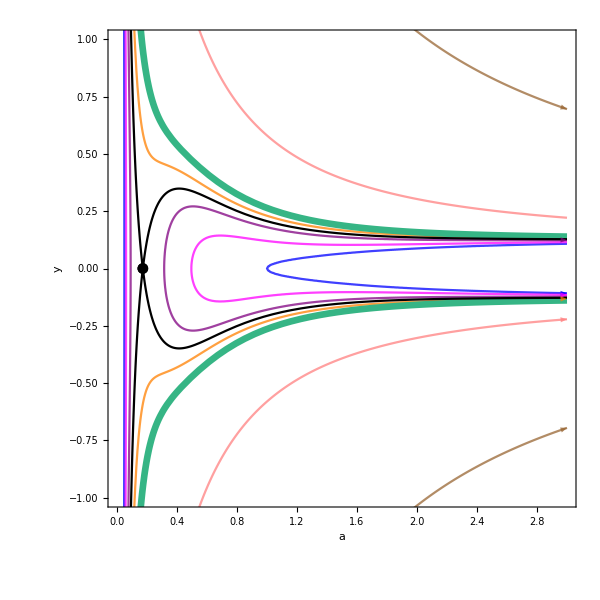

```mathematica
(*Show all components of plots*)
PhaseSpacec1ay=Show[trajc1ay,FFSc1ay,CFSc1ay,Einsteinc1ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc1ay=Plot[{Uay[a,0.2][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energyay[1]=Plot[{Energyay[0.2,0][[1]]},{a,0,0.04},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[2]=Plot[{Energyay[0.2,0][[1]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[3]=Plot[{Energyay[0.2,0.12][[1]]},{a,0,0.055},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[4]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.5,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[5]=Plot[{Energyay[0.2,0.18][[1]]},{a,0,0.08},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[6]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.32,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[7]=Plot[{Energyay[0.2,0.23][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energyay[8]=Plot[{Energyay[0.2,0.58][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energyay[9]=Plot[{Energyay[0.2,2.06][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energyay[10]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energyay[11]=Plot[{Energyay[0.2,0][[1]]},{a,0.04,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[12]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.055,0.5},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[13]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.08,0.32},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1ay=Table[c1Energyay[i],{i,1,13}];
```

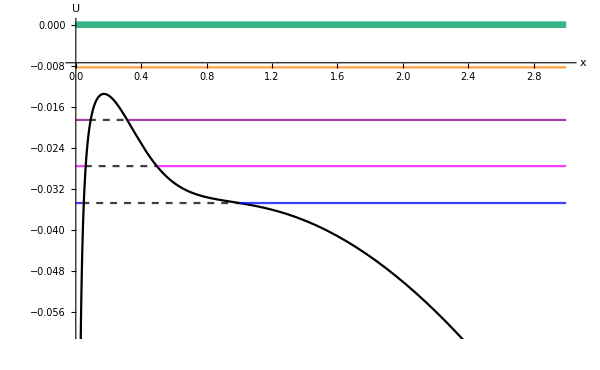

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1ay=Show[Uc1ay,Energyc1ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.06,0}]
```

### Final Plot

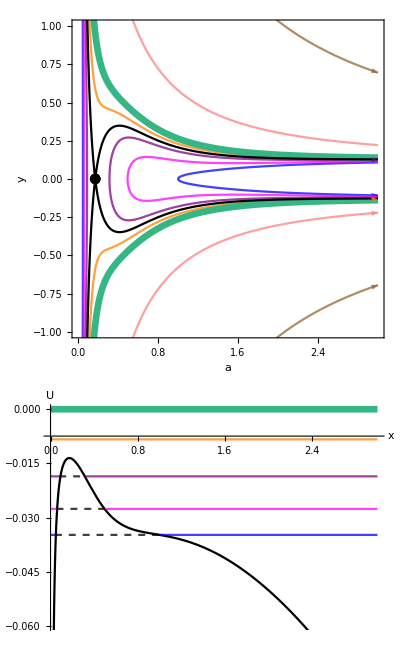

```mathematica
(*Plot the phase space and potential together*)
ayc1=GraphicsColumn[{PhaseSpacec1ay,Potentialc1ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc1.pdf",ayc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc2ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[2]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[2]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c2trajay[1]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[2]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,aTwoEinsteinPointsc2[[2]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[3]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[4]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[5]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[6]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[7]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[8]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[9]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[10]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[11]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[12]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc2ay=Table[c2trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2ay=Plot[{FFSay[a,0.2][[2]],-FFSay[a,0.1][[2]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2ay=Plot[{CFSay[a,aTwoEinsteinPointsc2,0.1][[2]],-CFSay[a,aTwoEinsteinPointsc2,0.1][[2]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2ay=ListPlot[{{aTwoEinsteinPointsc2[[1]],0},{aTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc2ay=ContourPlot[Accnay[[2]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

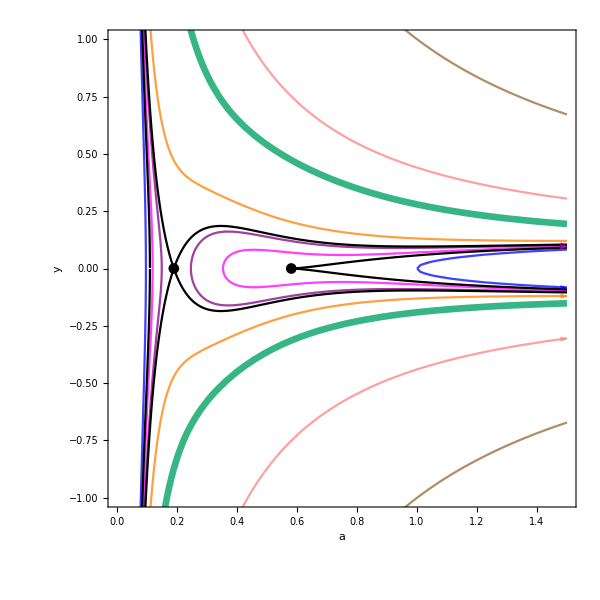

```mathematica
(*Show all components of plots*)
PhaseSpacec2ay=Show[trajc2ay,FFSc2ay,CFSc2ay,Einsteinc2ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc2ay=Plot[{Uay[a,0.1][[2]]},{a,0,1.5},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c2Energyay[1]=Plot[{Energyay[0.1,0][[2]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[2]=Plot[{Energyay[0.1,0][[2]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[3]=Plot[{Energyay[0.1,0.07][[2]]},{a,0,0.12},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[4]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.355,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[5]=Plot[{Energyay[0.1,0.09][[2]]},{a,0,0.145},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[6]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.245,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[7]=Plot[{Energyay[0.1,0.131][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energyay[8]=Plot[{Energyay[0.1,0.44][[2]]},{a,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energyay[9]=Plot[{Energyay[0.1,1][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energyay[10]=Plot[{0},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energyay[11]=Plot[{Energyay[0.1,0][[2]]},{a,0.09,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[12]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.12,0.355},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[13]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.145,0.245},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2ay=Table[c2Energyay[i],{i,1,13}];
```

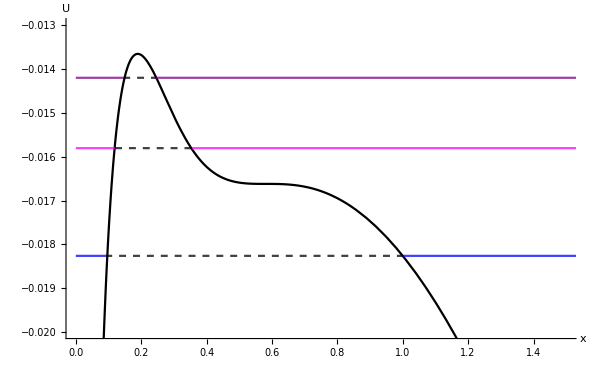

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2ay=Show[Uc2ay,Energyc2ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.5},{-0.02,-0.013}}]
```

### Final Plot

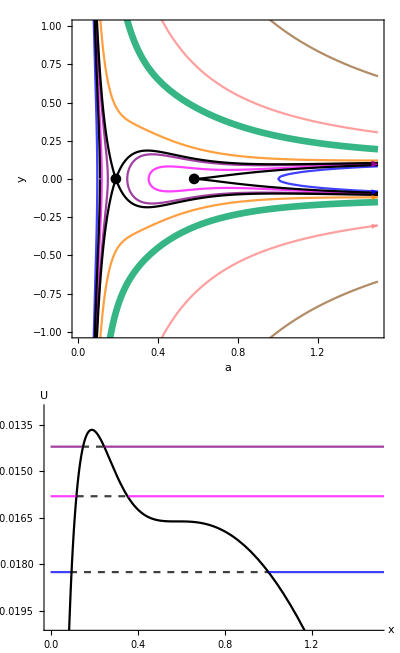

```mathematica
(*Plot the phase space and potential together*)
ayc2=GraphicsColumn[{PhaseSpacec2ay,Potentialc2ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc2.pdf",ayc2]*)
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc3ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[3]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[3]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c3trajay[1]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[2]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[1]],aThreeEinsteinPointsc3[[3]]},{y,-1.5,1.5},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[3]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[4]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[5]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,aThreeEinsteinPointsc3[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[6]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[7]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[8]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[9]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[10]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[11]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[12]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[13]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc3ay=Table[c3trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3ay=Plot[{FFSay[a,0.08][[3]],-FFSay[a,0.08][[3]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3ay=Plot[{CFSay[a,aThreeEinsteinPointsc3,0.08][[3]],-CFSay[a,aThreeEinsteinPointsc3,0.08][[3]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3ay=ListPlot[{{aThreeEinsteinPointsc3[[1]],0},{aThreeEinsteinPointsc3[[2]],0},{aThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc3ay=ContourPlot[Accna[[3]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

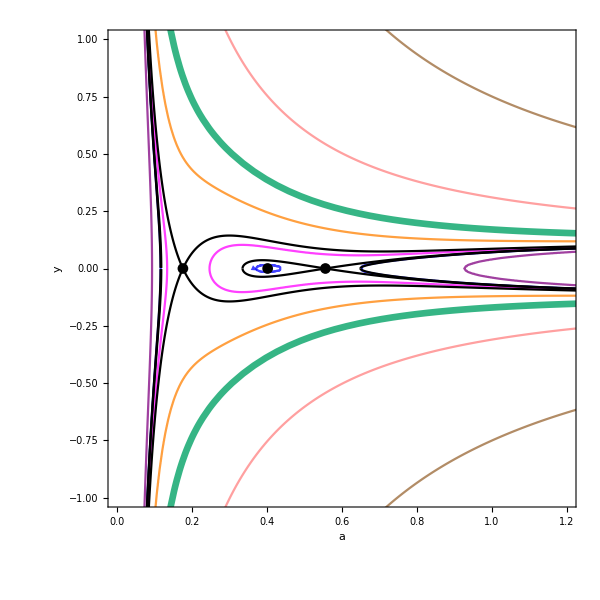

```mathematica
(*Show all components of plots*)
PhaseSpacec3ay=Show[trajc3ay,FFSc3ay,CFSc3ay,Einsteinc3ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc3ay=Plot[{Uay[a,0.08][[3]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c3Energyay[1]=Plot[{Energyay[0.08,0.071][[3]]},{a,0,0.115},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[2]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.37,0.43},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[3]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.64,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[4]=Plot[{Energyay[0.08,0.08][[3]]},{a,0,0.13},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[5]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.25,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[6]=Plot[{Energyay[0.08,0.04][[3]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[7]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.925,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[8]=Plot[{Energyay[0.08,0.121][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energyay[9]=Plot[{Energyay[0.08,0.31][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energyay[10]=Plot[{Energyay[0.08,0.75][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energyay[12]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.115,0.37},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[13]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.43,0.64},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[14]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.13,0.25},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[15]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.09,0.925},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3ay=Table[c3Energyay[i],{i,1,15}];
```

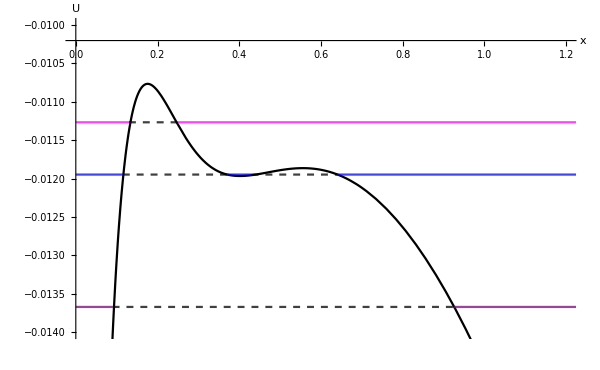

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3ay=Show[Uc3ay,Energyc3ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.014,-0.01}}]
```

### Final Plot

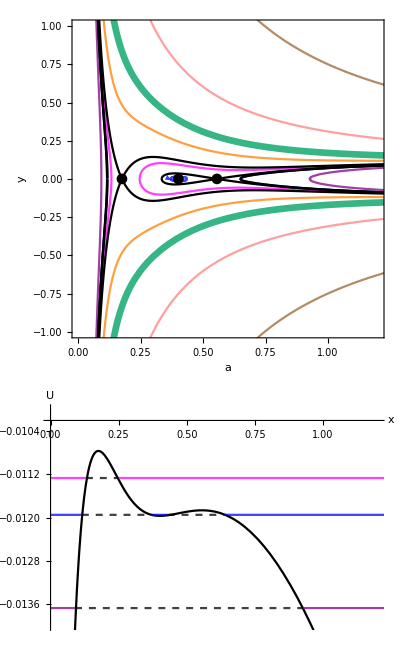

```mathematica
(*Plot the phase space and potential together*)
ayc3=GraphicsColumn[{PhaseSpacec3ay,Potentialc3ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc3.pdf",ayc3]*)
```

## Three Einstein Points: c4

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc4ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[4]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[4]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c4trajay[1]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[2]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[1]],aThreeEinsteinPointsc4[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,0,0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[3]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[4]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[5]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[6]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[7]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[8]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[9]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[10]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[11]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc4ay=Table[c4trajay[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4ay=Plot[{FFSay[a,0.08][[4]],-FFSay[a,0.08][[4]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4ay=Plot[{CFSay[a,aThreeEinsteinPointsc4,0.08][[4]],-CFSay[a,aThreeEinsteinPointsc4,0.08][[4]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4ay=ListPlot[{{aThreeEinsteinPointsc4[[1]],0},{aThreeEinsteinPointsc4[[2]],0},{aThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc4ay=ContourPlot[Accnya[[4]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

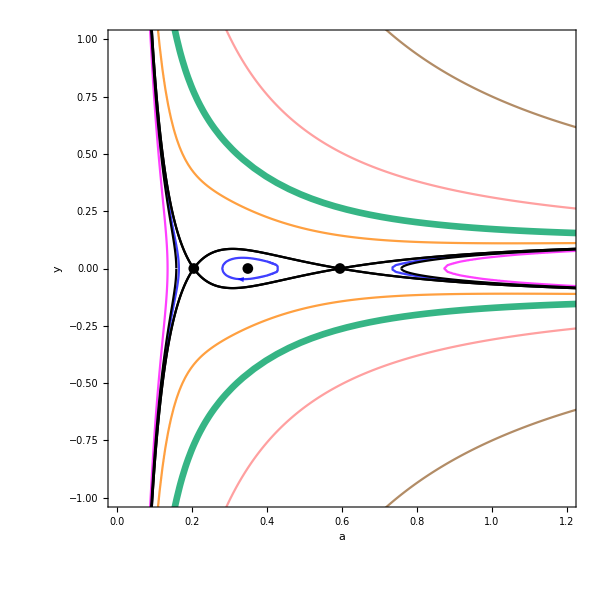

```mathematica
(*Show all components of plots*)
PhaseSpacec4ay=Show[trajc4ay,FFSc4ay,CFSc4ay,Einsteinc4ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc4ay=Plot[{Uay[a,0.08][[4]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c4Energyay[1]=Plot[{Energyay[0.08,0.065][[4]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[2]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.28,0.435},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[3]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.73,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[4]=Plot[{Energyay[0.08,0.05][[4]]},{a,0,0.135},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[5]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[6]=Plot[{Energyay[0.08,0.11][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energyay[7]=Plot[{Energyay[0.08,0.31][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energyay[8]=Plot[{Energyay[0.08,0.75][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energyay[9]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energyay[10]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.16,0.28},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[11]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.435,0.73},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[12]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.135,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4ay=Table[c4Energyay[i],{i,1,12}];
```

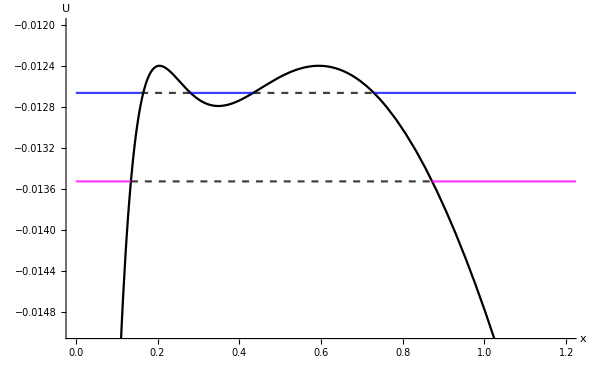

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4ay=Show[Uc4ay,Energyc4ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.015,-0.012}}]
```

### Final Plot

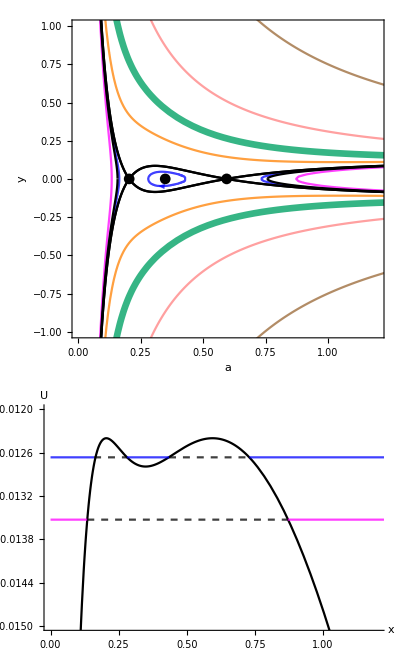

```mathematica
(*Plot the phase space and potential together*)
ayc4=GraphicsColumn[{PhaseSpacec4ay,Potentialc4ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc4.pdf",ayc4]*)
```

## Three Einstein Points: c5

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc5ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[5]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[5]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c5trajay[1]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[2]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[1]],aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[3]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[4]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[5]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[6]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[7]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[8]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[9]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[10]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[11]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[12]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[13]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc5ay=Table[c5trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5ay=Plot[{FFSay[a,0.08][[5]],-FFSay[a,0.08][[5]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5ay=Plot[{CFSay[a,aThreeEinsteinPointsc5,0.08][[5]],-CFSay[a,aThreeEinsteinPointsc5,0.08][[5]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5ay=ListPlot[{{aThreeEinsteinPointsc5[[1]],0},{aThreeEinsteinPointsc5[[2]],0},{aThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc5ay=ContourPlot[Accnay[[5]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

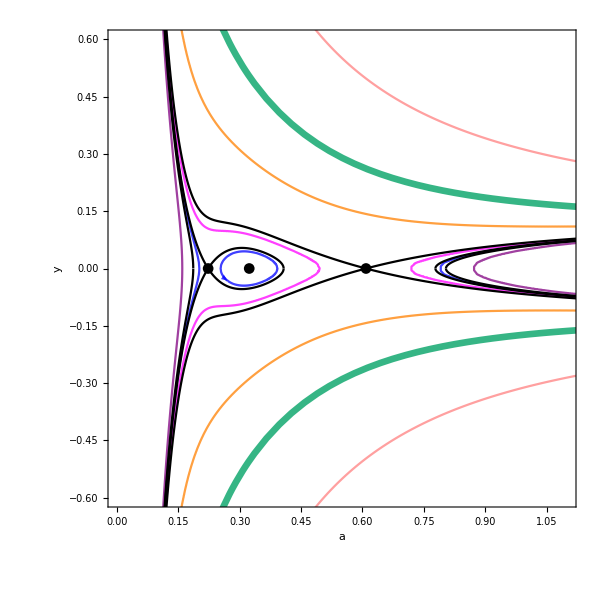

```mathematica
(*Show all components of plots*)
PhaseSpacec5ay=Show[trajc5ay,FFSc5ay,CFSc5ay,Einsteinc5ay,PlotRange->{{0,1.1},{-0.6,0.6}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc5ay=Plot[{Uay[a,0.08][[5]]},{a,0,1.1},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c5Energyay[1]=Plot[{Energyay[0.08,0.06][[5]]},{a,0,0.195},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[2]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.26,0.39},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[3]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.785,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[4]=Plot[{Energyay[0.08,0.065][[5]]},{a,0,0.495},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[5]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.715,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[6]=Plot[{Energyay[0.08,0.05][[5]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[7]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[8]=Plot[{Energyay[0.08,0.11][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energyay[9]=Plot[{Energyay[0.08,0.31][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energyay[10]=Plot[{Energyay[0.08,0.75][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energyay[12]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.195,0.26},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[13]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.39,0.785},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[14]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.495,0.715},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[15]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.16,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5ay=Table[c5Energyay[i],{i,1,15}];
```

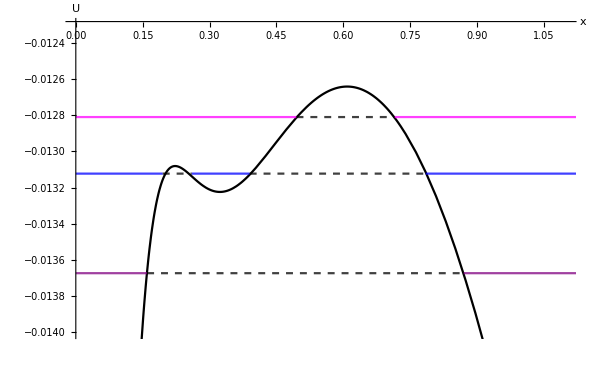

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5ay=Show[Uc5ay,Energyc5ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.1},{-0.014,-0.0123}}]
```

### Final Plot

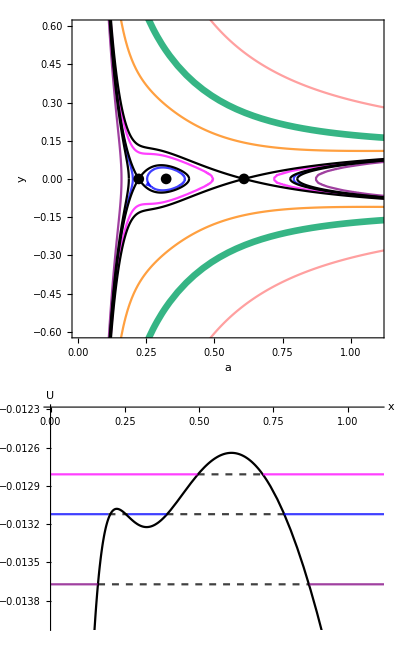

```mathematica
(*Plot the phase space and potential together*)
ayc5=GraphicsColumn[{PhaseSpacec5ay,Potentialc5ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc5.pdf",ayc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc6ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[6]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[6]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c6trajay[1]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,0,aTwoEinsteinPointsc6[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[2]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[3]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,0,aTwoEinsteinPointsc6[[2]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[4]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[5]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[6]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[7]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[8]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[9]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[10]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc6ay=Table[c6trajay[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6ay=Plot[{FFSay[a,0.9][[6]],-FFSay[a,0.9][[6]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6ay=Plot[{CFSay[a,aTwoEinsteinPointsc6,0.9][[6]],-CFSay[a,aTwoEinsteinPointsc6,0.9][[6]]},{a,0.1,10},PlotStyle->{Black},PlotRange->All,PlotPoints->100];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6ay=ListPlot[{{aTwoEinsteinPointsc6[[1]],0},{aTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnac6ay=ContourPlot[Accnay[[6]]==0,{a,0,10},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

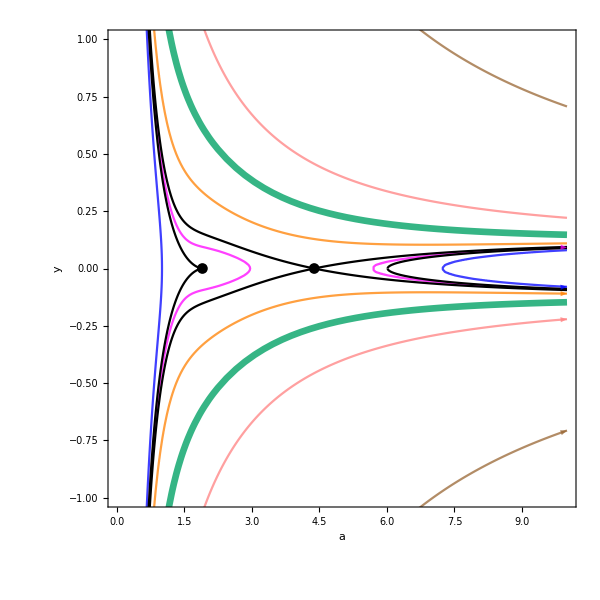

```mathematica
(*Show all components of plots*)
PhaseSpacec6ay=Show[trajc6ay,FFSc6ay,CFSc6ay,Einsteinc6ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc6ay=Plot[{Uay[a,0.9][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c6Energyay[1]=Plot[{Energyay[0.9,0][[6]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[2]=Plot[{Energyay[0.9,0][[6]]},{a,7.2,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[3]=Plot[{Energyay[0.9,0.44][[6]]},{a,0,2.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[4]=Plot[{Energyay[0.9,0.44][[6]]},{a,5.65,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[5]=Plot[{Energyay[0.9,0.75][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energyay[6]=Plot[{Energyay[0.9,2.06][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energyay[7]=Plot[{Energyay[0.9,7.02][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energyay[8]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energyay[9]=Plot[{Energyay[0.9,0][[6]]},{a,1,7.2},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energyay[10]=Plot[{Energyay[0.9,0.44][[6]]},{a,2.95,5.65},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6ay=Table[c6Energyay[i],{i,1,10}];
```

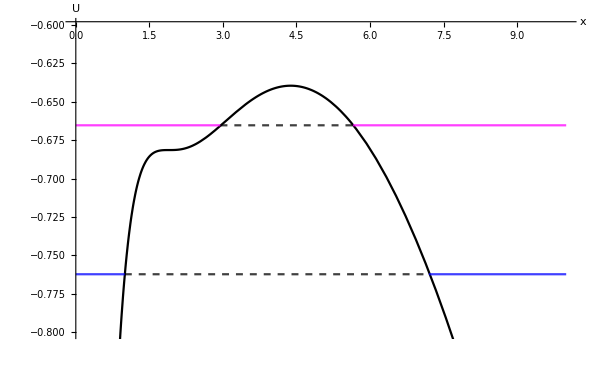

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6ay=Show[Uc6ay,Energyc6ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.8,-0.6}]
```

### Final Plot

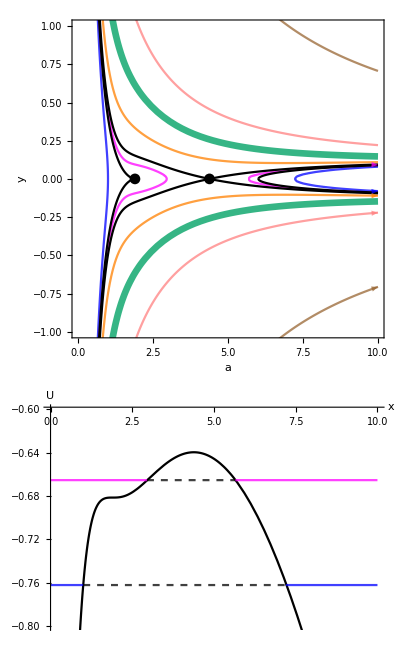

```mathematica
(*Plot the phase space and potential together*)
ayc6=GraphicsColumn[{PhaseSpacec6ay,Potentialc6ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc6.pdf",ayc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc7ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[7]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[7]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
c7trajay[1]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[2]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[3]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[4]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[5]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[6]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[7]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[8]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[9]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[10]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[11]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[12]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc7ay=Table[c7trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7ay=Plot[{FFSay[a,0.9][[7]],-FFSay[a,0.9][[7]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7ay=Plot[{CFSay[a,aOneEinsteinPointc7,0.9][[7]],-CFSay[a,aOneEinsteinPointc7,0.9][[7]]},{a,0,10},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7ay=ListPlot[{{aOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the Accna = 0 curve for this case*)
Accnc7ay=ContourPlot[Accnay[[7]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

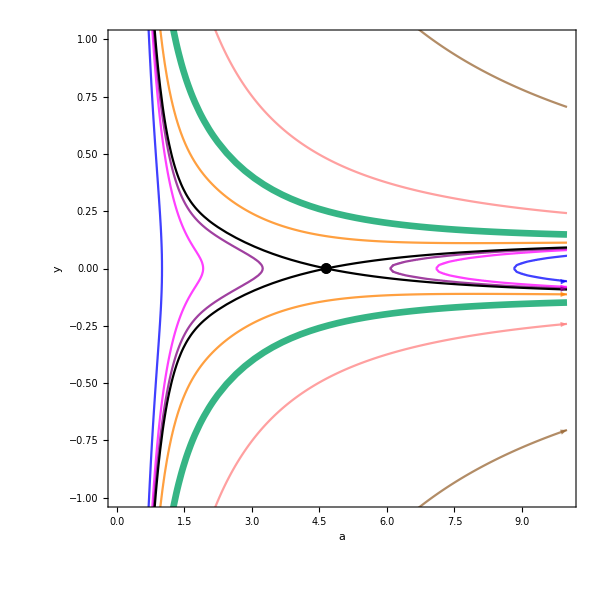

```mathematica
(*Show all components of plots*)
PhaseSpacec7ay=Show[trajc7ay,FFSc7ay,CFSc7ay,Einsteinc7ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc7ay=Plot[{Uay[a,0.9][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c7Energyay[1]=Plot[{Energyay[0.9,0][[7]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[2]=Plot[{Energyay[0.9,0][[7]]},{a,8.8,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[3]=Plot[{Energyay[0.9,0.58][[7]]},{a,0,1.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[4]=Plot[{Energyay[0.9,0.58][[7]]},{a,7.05,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[5]=Plot[{Energyay[0.9,0.68][[7]]},{a,0,3.3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[6]=Plot[{Energyay[0.9,0.68][[7]]},{a,6,10},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[7]=Plot[{Energyay[0.9,0.98][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energyay[8]=Plot[{Energyay[0.9,2.35][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energyay[9]=Plot[{Energyay[0.9,7.02][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energyay[10]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energyay[11]=Plot[{Energyay[0.9,0][[7]]},{a,1,8.8},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[12]=Plot[{Energyay[0.9,0.58][[7]]},{a,1.95,7.05},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[13]=Plot[{Energyay[0.9,0.68][[7]]},{a,3.3,6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7ay=Table[c7Energyay[i],{i,1,13}];
```

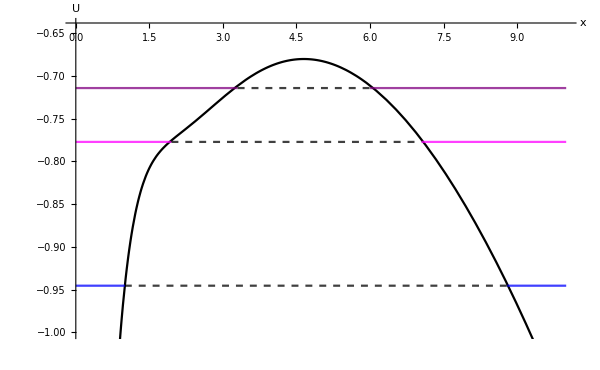

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7ay=Show[Uc7ay,Energyc7ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-1,-0.64}]
```

### Final Plot

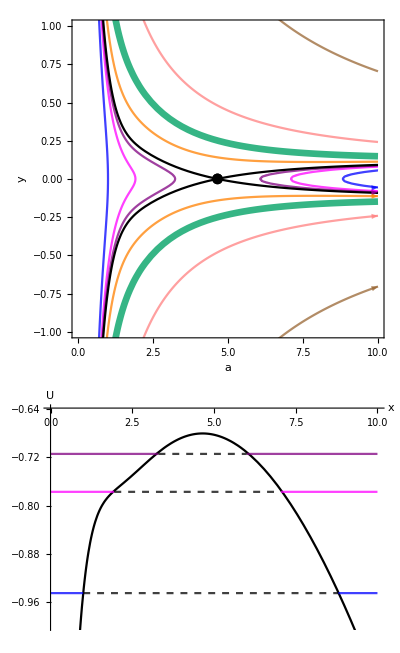

```mathematica
(*Plot the phase space and potential together*)
ayc7=GraphicsColumn[{PhaseSpacec7ay,Potentialc7ay},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc7.pdf",ayc7]*)
```

## Add Upper Limits to Matter and Radiation